## Clear Everything

```mathematica
ClearAll["Global`*"];
```

## Set Saved ΔMAX, KMAX, and ratioWidth

```mathematica
ΔMAX=16;
KMAX=65;
NMAX=Floor[ΔMAX/(3/2)]
ratioWidth=8/10;
```

10

## Load Odd Data

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[ΔMAX]<>" Data/";

t1=AbsoluteTime[];

(* Basis Files *)
For[n=3,n≤NMAX,n=n+2,
Get[dir<>"Basis"<>ToString[n]<>"_Dmax"<>ToString[ΔMAX]];];

(* Mass Files *)
For[n=3,n≤NMAX,n=n+2,
Get[dir<>"Bas"<>ToString[n]<>"Mass"];];

(* N -> N+2 Files *)
Get[dir<>"Bas1to3"];
For[n=3,n≤NMAX-2,n=n+2,
Get[dir<>"Int"<>ToString[n]<>"to"<>ToString[n+2]<>"_Dmax"<>ToString[ΔMAX]<>"_Kmax"<>ToString[KMAX]<>"_r8"];];

(* N -> N Files *)
For[n=3,n≤NMAX,n=n+2,
Get[dir<>"Int"<>ToString[n]<>"to"<>ToString[n]<>"_Dmax"<>ToString[ΔMAX]<>"_Kmax"<>ToString[KMAX]<>"_r8"];];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 4.42683

## Load Even Data

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[ΔMAX]<>" Data/";

t1=AbsoluteTime[];

(* Basis Files *)
For[n=2,n≤NMAX,n=n+2,
Get[dir<>"Basis"<>ToString[n]<>"_Dmax"<>ToString[ΔMAX]];];

(* Mass Files *)
For[n=2,n≤NMAX,n=n+2,
Get[dir<>"Bas"<>ToString[n]<>"Mass"];];

(* N -> N+2 Files *)
Get[dir<>"Bas1to3"];
For[n=2,n≤NMAX-2,n=n+2,
Get[dir<>"Int"<>ToString[n]<>"to"<>ToString[n+2]<>"_Dmax"<>ToString[ΔMAX]<>"_Kmax"<>ToString[KMAX]<>"_r8"];];

(* N -> N Files *)
For[n=2,n≤NMAX,n=n+2,
Get[dir<>"Int"<>ToString[n]<>"to"<>ToString[n]<>"_Dmax"<>ToString[ΔMAX]<>"_Kmax"<>ToString[KMAX]<>"_r8"];];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 9.86051

## Define Functions

```mathematica
(* Number of basis states *)
numStates[npart_,Δmax_]:=Which[Δmax<(3/2)*npart,0,npart==1,1,npart≠ 1,ToExpression["counts"<>ToString[npart]][[1;;Floor[Δmax-(3/2)npart+1]]]//Total];
```

```mathematica
(* Kinetic function *)
kineticFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax],μsq},
If[npart==1,0.,
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[IdentityMatrix[size],DiagonalMatrix[Table[(μsq[[k]]+μsq[[k+1]])/2,{k,kmax}]]]//N]];
```

```mathematica
(* Full kinetic matrix. sector = "odd" or "even" *)
kineticMatrix[Δmax_,kmax_,sector_]:=Module[{Nmax=Floor[Δmax/(3/2)],list,n},
Which[sector=="odd",
list=Table[kineticFunc[n,Δmax,kmax],{n,1,Nmax,2}],
sector=="even",
list=Table[kineticFunc[n,Δmax,kmax],{n,2,Nmax,2}]];

DiagonalMatrix[Hold/@list]//ReleaseHold//ArrayFlatten];
```

```mathematica
(* Mass function *)
massFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax]},
If[npart==1,1.,
KroneckerProduct[Chop[ToExpression["BasisMass"<>ToString[npart]][[1;;size,1;;size]],10^-35],IdentityMatrix[kmax]]]];
```

```mathematica
(* Full mass matrix. sector = "odd" or "even" *)
massMatrix[Δmax_,kmax_,sector_]:=Module[{Nmax=Floor[Δmax/(3/2)],list,n},
Which[sector=="odd",
list=Table[massFunc[n,Δmax,kmax],{n,1,Nmax,2}],
sector=="even",
list=Table[massFunc[n,Δmax,kmax],{n,2,Nmax,2}]];

DiagonalMatrix[Hold/@list]//ReleaseHold//ArrayFlatten];
```

```mathematica
(* Extract a (dmax,kmax) submatrix from a (DMAX,KMAX) n1-to-n2 matrix. 
   n1,n2 = particle number for row/col, and I'm assuming n1,n2 > 1.   *)
submatrix[matrix_,n1_,n2_,dmax_,kmax_]:=Module[{size1=numStates[n1,dmax],size2=numStates[n2,dmax],temp1,temp2,temp3,μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(KMAX-k),{k,KMAX}]/Sum[ratioWidth^(KMAX-k),{k,KMAX}],0]]//N;
temp1=matrix[[1;;size1*KMAX,1;;size2*KMAX]];
temp2=Partition[temp1,{KMAX,KMAX}];
temp3=Map[#[[1;;kmax,1;;kmax]]&,temp2,{2}]//ArrayFlatten;
temp3*√(1/μsq[[kmax+1]])
];
```

```mathematica
(* Interaction n->n function *)
intNNFunc[npart_,Δmax_,kmax_]:=Module[{matrix},
If[npart==1,0.,
matrix=ToExpression["Int"<>ToString[npart]<>"to"<>ToString[npart]];
submatrix[matrix,npart,npart,Δmax,kmax]
]
];
```

```mathematica
(* Interaction n->n+2 function *)
intNN2Func[npart_,Δmax_,kmax_]:=Module[{matrix,μsq},
If[npart==1,{int13Func[Δmax,kmax]},
matrix=ToExpression["Int"<>ToString[npart]<>"to"<>ToString[npart+2]];
submatrix[matrix,npart,npart+2,Δmax,kmax]
]]; 

int13Func[Δmax_,kmax_]:=Module[{size3=numStates[3,Δmax],μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[Chop[Basis1to3[[1;;size3]]],Table[√((μsq[[k+1]]-μsq[[k]])/(2π)),{k,kmax}]]//Flatten];
```

```mathematica
(* Full interaction matrix. sector = "odd" or "even" *)
intMatrix[Δmax_,kmax_,sector_]:=Module[{Nmax=Floor[Δmax/(3/2)],temp,matrix},
Which[sector=="odd",
temp=ConstantArray[0,{Ceiling[Nmax/2],Ceiling[Nmax/2]}];
For[i=1,i≤Ceiling[Nmax/2],i++,temp[[i,i]]=intNNFunc[2i-1,Δmax,kmax];];
For[i=1,i≤Ceiling[Nmax/2]-1,i++,
temp[[i,i+1]]=intNN2Func[2i-1,Δmax,kmax];
temp[[i+1,i]]=Transpose[temp[[i,i+1]]];];,
sector=="even",
temp=ConstantArray[0,{Floor[Nmax/2],Floor[Nmax/2]}];
For[i=1,i≤Floor[Nmax/2],i++,temp[[i,i]]=intNNFunc[2i,Δmax,kmax];];
For[i=1,i≤Floor[Nmax/2]-1,i++,
temp[[i,i+1]]=intNN2Func[2i,Δmax,kmax];
temp[[i+1,i]]=Transpose[temp[[i,i+1]]];];
];

temp//ArrayFlatten];
```

```mathematica
(* Nonlocal counterterm function *)
nonlocalFunc[npart_,Δmax_,kmax_,Λ_]:=Module[{m=1.,μsq,kineticN,massN,kineticN2,massN2,fullN,fullN2,valsN,vecsN,valsN2,vecsN2,int,MassShifts,MassShiftsNonPositive,V},

μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kineticN2=kineticFunc[npart+2,Δmax,kmax];
massN2=massFunc[npart+2,Δmax,kmax];
fullN2=Λ^2*kineticN2+m^2*massN2//N;
{valsN2,vecsN2}=eigensys[fullN2];
int=intNN2Func[npart,Δmax,kmax];

If[npart==1,-Λ^2*Sum[(int.vecsN2[[i]])^2/(1-valsN2[[i]]),{i,Length[valsN2]}][[1]],
kineticN=kineticFunc[npart,Δmax,kmax];
massN=massFunc[npart,Δmax,kmax];
fullN=Λ^2*kineticN+m^2*massN//N;
{valsN,vecsN}=eigensys[fullN];
MassShifts=Total[Λ^2*(vecsN.int.Transpose[vecsN2])^2/Outer[Subtract,valsN,valsN2],{2}];
MassShiftsNonPositive=MassShifts/.{x_?Positive->0.};
V=vecsN;
-Transpose[V].DiagonalMatrix[MassShiftsNonPositive].V
]
];
```

```mathematica
(* Full nonlocal counterterm matrix. sector = "odd" or "even" *)
nonlocalMatrix[Δmax_,kmax_,Λ_,sector_]:=Module[{Nmax=Floor[Δmax/(3/2)],list,n,pad,temp},
Which[sector=="odd",
list=Table[nonlocalFunc[n,Δmax,kmax,Λ],{n,1,Nmax-2,2}],
sector=="even",
list=Table[nonlocalFunc[n,Δmax,kmax,Λ],{n,2,Nmax-2,2}]];

pad=Which[(sector=="odd"&&OddQ[Nmax])||(sector=="even"&&EvenQ[Nmax]),numStates[Nmax,Δmax]*kmax,(sector=="odd"&&EvenQ[Nmax])||(sector=="even"&&OddQ[Nmax]),numStates[Nmax-1,Δmax]*kmax];

temp=DiagonalMatrix[Hold/@list]//ReleaseHold//ArrayFlatten;
ArrayPad[temp,{{0,pad},{0,pad}}]
];
```

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

```mathematica
(* Compute Eigenvalues*)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;
eigenvals[mat_]:=Eigenvalues[mat]//Sort;
```

```mathematica
(* Monomial inner product *)

𝒜[M_,k_,kp_]:=𝒜[M,k,kp]= 
Module[{n,Km,Kp,perms,multiplicity,parts,qvecs},
n=Length[k];
perms=Permutations[kp];
multiplicity=Times@@(Tally[kp][[All,2]]!);

multiplicity*
Sum[
Km=k[[All,1]]+kpp[[All,1]];
Kp=k[[All,2]]+kpp[[All,2]];
parts=IntegerPartitions[M,n];parts=PadRight[parts,{Length[parts],n}];
parts=Flatten[Permutations[#]&/@parts,1];
qvecs=Select[parts,Min[Kp/2-#]≥0&];
Sum[Times@@(Binomial[Kp,2q]Pochhammer[1/2,q]Pochhammer[1/2,Km]Pochhammer[Km+1/2,Kp-q]),{q,qvecs}]
,{kpp,perms}]//Simplify];

InnerFT[k_,kp_]:=Module[{n=Length[k],TotDeriv,TotPerp},
TotDeriv=Total[k,2]+Total[kp,2];
TotPerp=Total[k[[All,2]]]+Total[kp[[All,2]]];
If[OddQ[TotPerp],0,
π^2/((4π)^n 2^(n-4)Gamma[(TotPerp+n-1)/2])Sum[((-1)^(TotPerp/2-M)Gamma[TotPerp/2-M+1/2])/Gamma[TotDeriv-M+n/2] 𝒜[M,k,kp],{M,0,TotPerp/2}]//Simplify]
];
```

```mathematica
(* ϕ^n Overlaps *)

ϕnOverlaps[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax],dir,mons,basis,monOverlaps,basisOverlaps},
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[ΔMAX]<>" Data/";
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[ΔMAX]];
mons=ToExpression["mons"<>ToString[npart]][[1;;size]];
basis=ToExpression["basis"<>ToString[npart]][[1;;size,1;;size]];
monOverlaps=InnerFT[ConstantArray[{0,0},npart],#]&/@mons;
basisOverlaps=basis.monOverlaps;
KroneckerProduct[basisOverlaps,μOverlaps[npart,kmax,0]]//Flatten
];


(* μOverlaps is missing an overall factor of P^Vminus Λ^(Vperp+(n-1)/2). Need to put this in by hand when computing spectral densities. *)

μOverlaps[n_,Kmax_,Vperp_]:=Module[{μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(Kmax-k),{k,Kmax}]/Sum[ratioWidth^(Kmax-k),{k,Kmax}],0]]//N;
1/(√(2π))1/((n+1+2Vperp)/4)Table[(μsq[[k+1]]^((n+1+2Vperp)/4)-μsq[[k]]^((n+1+2Vperp)/4))/(√(μsq[[k+1]]-μsq[[k]])),{k,Kmax}]]
```

## Compute Spectrum and Make Fixed k_max Plots

```mathematica
Δmax=10;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0146699

```mathematica
f=.5;
```

```mathematica
(* Scan over couplings *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N; *)
(* glist={12.5,12.75,13.2,13.4,13.5,13.6}//N; *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,14,15,15.5,15.75,16.,16.1,16.2}//N; *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5, 12.75,13,13.5,13.7,13.9,14.,14.1,14.2,14.4,14.5}//N; *)
glist={0,2,4,6,8,10,12,14,16,17,18,18.25,18.5,18.75,19,19.1,19.18}//N;
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
vals=eigenvals[full];
{g,kmax,vals[[1;;nvals]]}//Flatten,{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.32973

```mathematica
newdata
```

{{0.,65,4.24936,4.53061},{2.,65,4.21192,4.48986},{4.,65,4.08487,4.35917},{6.,65,3.86866,4.13893},{8.,65,3.56264,3.82943},{10.,65,3.16496,3.431},{12.,65,2.67209,2.94425},{14.,65,2.07791,2.36995},{16.,65,1.37205,1.70781},{17.,65,0.971509,1.2809},{18.,65,0.532457,0.745348},{18.25,65,0.415237,0.602861},{18.5,65,0.294153,0.455306},{18.75,65,0.168104,0.300005},{19.,65,0.0335617,0.12913},{19.1,65,-0.0275021,0.050885},{19.18,65,-0.099953,-0.0223974}}

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD10IR05VaryF"];
```

```mathematica
EvenSpectrumD10F05={};
```

```mathematica
EvenSpectrumD10F05=Join[EvenSpectrumD10F05,newdata]//Sort
```

{{0.,65,4.24936,4.53061},{2.,65,4.21192,4.48986},{4.,65,4.08487,4.35917},{6.,65,3.86866,4.13893},{8.,65,3.56264,3.82943},{10.,65,3.16496,3.431},{12.,65,2.67209,2.94425},{14.,65,2.07791,2.36995},{16.,65,1.37205,1.70781},{17.,65,0.971509,1.2809},{18.,65,0.532457,0.745348},{18.25,65,0.415237,0.602861},{18.5,65,0.294153,0.455306},{18.75,65,0.168104,0.300005},{19.,65,0.0335617,0.12913},{19.1,65,-0.0275021,0.050885},{19.18,65,-0.099953,-0.0223974}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD10IR05VaryF";
DeleteFile[filename];
Save[filename,{OddSpectrumD10F05,EvenSpectrumD10F05,OddSpectrumD10F1,EvenSpectrumD10F1,OddSpectrumD10F2,EvenSpectrumD10F2}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD16IR05F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD16F1,EvenSpectrumD16F1,Extrap1pD16F1,Extrap2pD16F1,Extrap3pD16F1,OddSpectrumD16F1NOCT,EvenSpectrumD16F1NOCT,Extrap1pD16F1NOCT,Extrap3pD16F1NOCT}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD14F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD14F1,EvenSpectrumD14F1}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD12F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD12F1,EvenSpectrumD12F1}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="OddSpectrumD16VaryF";
DeleteFile[filename];
Save[filename,{OddSpectrumD16F1,OddSpectrumD16F075,OddSpectrumD16F11,OddSpectrumD16F12}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectrumD16VaryF";
DeleteFile[filename];
Save[filename,{EvenSpectrumD16F1,EvenSpectrumD16F11,EvenSpectrumD16F12}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16F1"];
Get["SpectrumD14F1"];
Get["SpectrumD12F1"];
```

```mathematica
data1p=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]]}]
data2p=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]]}]
data3p=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]]}]
```

{{0.,1.},{0.0795775,0.994593},{0.159155,0.978558},{0.238732,0.952112},{0.31831,0.915397},{0.397887,0.86849},{0.477465,0.8114},{0.557042,0.744058},{0.63662,0.666298},{0.716197,0.577808},{0.795775,0.478037},{0.875352,0.365954},{0.95493,0.239324},{0.994718,0.168844},{1.01461,0.131039},{1.03451,0.0907137},{1.05042,0.0555218},{1.06634,0.013914},{1.0743,-0.0490944},{1.08225,-0.789479}}

{{0.,4.16919},{0.0795775,4.14942},{0.159155,4.08555},{0.238732,3.9776},{0.31831,3.82538},{0.397887,3.62839},{0.477465,3.38586},{0.557042,3.09662},{0.63662,2.759},{0.716197,2.37066},{0.795775,1.92827},{0.875352,1.42674},{0.95493,0.856235},{0.994718,0.537781},{1.01461,0.366821},{1.03451,0.184204},{1.05042,0.0242649},{1.06634,-0.16249},{1.0743,-0.281378}}

{{0.,9.38238},{0.0795775,9.34319},{0.159155,9.20226},{0.238732,8.95985},{0.31831,8.61607},{0.397887,8.16866},{0.477465,7.61241},{0.557042,6.95448},{0.63662,6.19484},{0.716197,5.33341},{0.795775,4.37005},{0.875352,3.30442},{0.95493,2.13315},{0.994718,1.47848},{1.01461,1.13297},{1.03451,0.771333},{1.05042,0.465979},{1.06634,0.137604},{1.0743,-0.0145982},{1.08225,-0.759793}}

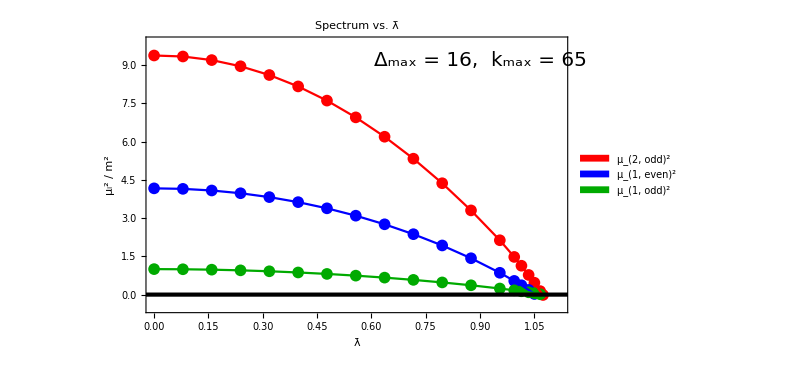

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.12},{-.5,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

```mathematica
Λ
```

1411.16

```mathematica
1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]
```

0.00546169

```mathematica
Select[OddSpectrumD16F1,#[[2]]==65&]
```

{{0.,65,1.,9.38238},{1.,65,0.994593,9.34319},{2.,65,0.978558,9.20226},{3.,65,0.952112,8.95985},{4.,65,0.915397,8.61607},{5.,65,0.86849,8.16866},{6.,65,0.8114,7.61241},{7.,65,0.744058,6.95448},{8.,65,0.666298,6.19484},{9.,65,0.577808,5.33341},{10.,65,0.478037,4.37005},{11.,65,0.365954,3.30442},{12.,65,0.239324,2.13315},{12.5,65,0.168844,1.47848},{12.75,65,0.131039,1.13297},{13.,65,0.0907137,0.771333},{13.2,65,0.0555218,0.465979},{13.4,65,0.013914,0.137604},{13.5,65,-0.0490944,-0.0145982},{13.6,65,-0.789479,-0.759793}}

```mathematica
Drop[Select[OddSpectrumD16F1,#[[2]]==65&],-1][[All,3]]
```

{1.,0.994593,0.978558,0.952112,0.915397,0.86849,0.8114,0.744058,0.666298,0.577808,0.478037,0.365954,0.239324,0.168844,0.131039,0.0907137,0.0555218,0.013914,-0.0490944}

```mathematica
Select[EvenSpectrumD16F1,#[[2]]==65&]
```

{{0.,65,4.16919,4.45044},{1.,65,4.14942,4.42963},{2.,65,4.08555,4.36464},{3.,65,3.9776,4.25557},{4.,65,3.82538,4.10251},{5.,65,3.62839,3.90551},{6.,65,3.38586,3.66449},{7.,65,3.09662,3.37343},{8.,65,2.759,3.00975},{9.,65,2.37066,2.59059},{10.,65,1.92827,2.11496},{11.,65,1.42674,1.57831},{12.,65,0.856235,0.971174},{12.5,65,0.537781,0.633641},{12.75,65,0.366821,0.452779},{13.,65,0.184204,0.260149},{13.2,65,0.0242649,0.0929317},{13.4,65,-0.16249,-0.0983016},{13.5,65,-0.281378,-0.218194}}

```mathematica
ratio2D16F1=Select[Thread[{(√Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])/((Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]],-1]/(4π))+10^-10),(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]])/(4*Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])}],#[[1]]∈Reals&]
ratio2D14F1=Select[Thread[{(√(Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD14F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04299},{6.21546,1.04377},{4.08726,1.04442},{3.00576,1.04473},{2.34219,1.04445},{1.88658,1.04322},{1.54851,1.04045},{1.2822,1.0352},{1.06135,1.02571},{0.868841,1.00843},{0.691084,0.974674},{0.512297,0.89443},{0.413088,0.796268},{0.35678,0.699831},{0.291141,0.507654},{0.22432,0.109258},{0.110619,-2.91956}}

{{1.×10^10,1.04599},{12.5323,1.04678},{6.21544,1.04764},{4.08722,1.0484},{3.0057,1.04886},{2.34212,1.04882},{1.88653,1.048},{1.5485,1.04595},{1.28227,1.04198},{1.06159,1.03478},{0.869401,1.02175},{0.692282,0.996591},{0.515011,0.938402},{0.417593,0.870182},{0.362955,0.806135},{0.300388,0.686665},{0.239065,0.469152},{0.149938,-0.429311},{0.0418979,-16.9753}}

{{1.×10^10,1.05192},{12.5323,1.05283},{6.2154,1.05381},{4.08714,1.05471},{3.00558,1.05537},{2.34195,1.05561},{1.88631,1.05525},{1.54826,1.05397},{1.28203,1.05131},{1.06142,1.0464},{0.869401,1.03751},{0.692714,1.02053},{0.516608,0.982071},{0.420633,0.938396},{0.367342,0.89872},{0.307185,0.827996},{0.249848,0.709646},{0.173115,0.337021},{0.111689,-0.650216}}

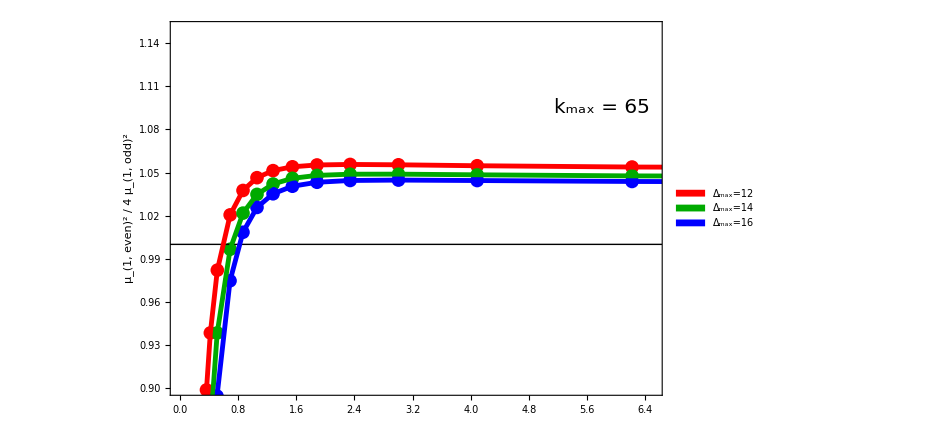

```mathematica
exper=ListPlot[{ratio2D12F1,ratio2D14F1,ratio2D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(1, even)^2  /  4 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.9,1.15}},Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,0.21}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D12F1,0],Drop[ratio2D14F1,0],Drop[ratio2D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

```mathematica
OddSpectrumD16F1NOCT
```

{{0.,65,1.,9.38238},{1.,65,0.994595,9.38764},{2.,65,0.97859,9.38009},{3.,65,0.952264,9.36008},{4.,65,0.915862,9.32785},{5.,65,0.869597,9.28357},{6.,65,0.813659,9.22734},{7.,65,0.748217,9.15921},{8.,65,0.673422,9.0792},{9.,65,0.589413,8.98731},{10.,65,0.496315,8.8835},{11.,65,0.394242,8.7677},{12.,65,0.283297,8.6398},{13.,65,0.163576,8.49968},{13.2,65,0.138587,8.47018},{13.4,65,0.113251,8.44017},{13.5,65,0.100453,8.42499}}

```mathematica
ratio2D16F1NOCT=Select[Thread[{(√(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04399},{6.21556,1.0478},{4.08759,1.05367},{3.00653,1.06164},{2.34368,1.07191},{1.88921,1.08483},{1.55284,1.10099},{1.28903,1.12142},{1.07196,1.14796},{0.885296,1.18412},{0.717296,1.23761},{0.557378,1.32932},{0.47636,1.40869},{0.434474,1.46613},{0.390955,1.54456},{0.354403,1.63223},{0.315592,1.75856},{0.295024,1.84565}}

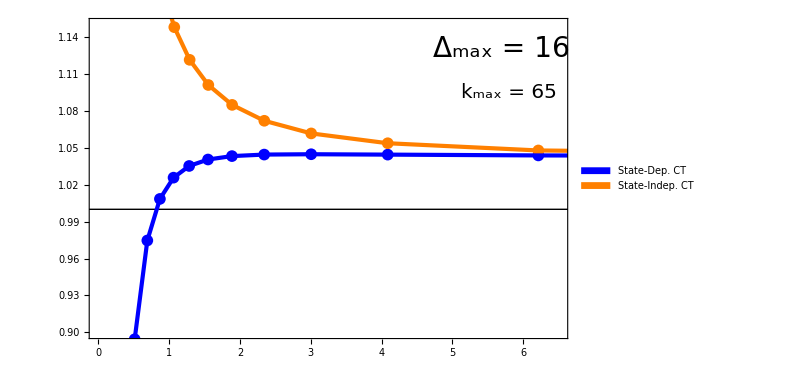

```mathematica
exper=ListPlot[{ratio2D16F1,ratio2D16F1NOCT},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Orange,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.15}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->28],{5.7,1.13}],Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"State-Dep. CT","State-Indep. CT"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.77,0.15}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D16F1,0],Drop[ratio2D16F1NOCT,0]},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
fig2=Show[exper,line,fit]
```

```mathematica
ratio3D16F1=Select[Thread[{(√Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])/((Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]],-1]/(4π))+10^-10),Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]],-1]/(9*Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])}],#[[1]]∈Reals&]
ratio3D14F1=Select[Thread[{(√(Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD14F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD14F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.04249},{12.5324,1.04378},{6.21546,1.04488},{4.08726,1.04561},{3.00576,1.04582},{2.34219,1.04506},{1.88658,1.04242},{1.54851,1.03852},{1.2822,1.03304},{1.06135,1.0256},{0.868841,1.01574},{0.691084,1.00329},{0.512297,0.990357},{0.413088,0.972941},{0.35678,0.960666},{0.291141,0.944771},{0.22432,0.932524},{0.110619,1.09885}}

{{1.×10^10,1.05347},{12.5323,1.05498},{6.21544,1.05629},{4.08722,1.05722},{3.0057,1.05763},{2.34212,1.05737},{1.88653,1.05626},{1.5485,1.05291},{1.28227,1.04733},{1.06159,1.03959},{0.869401,1.02899},{0.692282,1.01468},{0.515011,0.996923},{0.417593,0.990649},{0.362955,0.992934},{0.300388,0.992229},{0.239065,1.00003},{0.149938,1.10256},{0.0418979,4.43038}}

{{1.×10^10,1.0685},{12.5323,1.07027},{6.2154,1.07182},{4.08714,1.073},{3.00558,1.07365},{2.34195,1.07365},{1.88631,1.07284},{1.54826,1.07105},{1.28203,1.06803},{1.06142,1.06345},{0.869401,1.05685},{0.692714,1.04746},{0.516608,1.02598},{0.420633,1.01348},{0.367342,1.0088},{0.307185,1.00993},{0.249848,1.02518},{0.173115,1.08825},{0.111689,1.27519}}

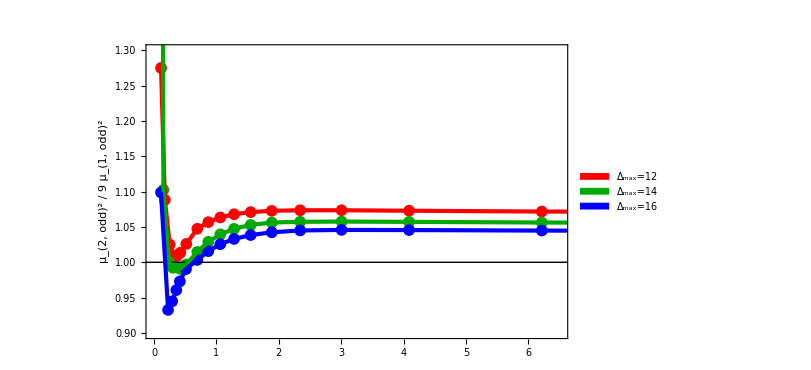

```mathematica
exper=ListPlot[{ratio3D12F1,Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2, odd)^2  /  9 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.35}]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,.75}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D12F1,0],Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

```mathematica
ratio3D16F1NOCT=Select[Thread[{(√(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.04249},{12.5324,1.04874},{6.21556,1.06503},{4.08759,1.09214},{3.00653,1.13164},{2.34368,1.18619},{1.88921,1.26006},{1.55284,1.36015},{1.28903,1.49802},{1.07196,1.69421},{0.885296,1.98877},{0.717296,2.47104},{0.557378,3.38859},{0.47636,4.24163},{0.434474,4.88065},{0.390955,5.77351},{0.354403,6.7909},{0.315592,8.28071},{0.295024,9.3189}}

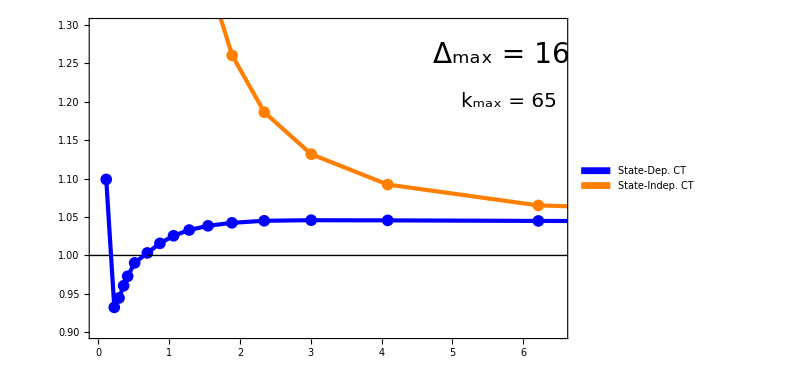

```mathematica
exper=ListPlot[{Drop[ratio3D16F1,0],ratio3D16F1NOCT},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Orange,PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->28],{5.7,1.26}],Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.2}]},PlotLegends->Placed[SwatchLegend[{"State-Dep. CT","State-Indep. CT","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.77,0.11}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D16F1,0],ratio3D16F1NOCT},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Blue}},InterpolationOrder->1,PlotRange->All];
fig4=Show[exper,line,fit]
```

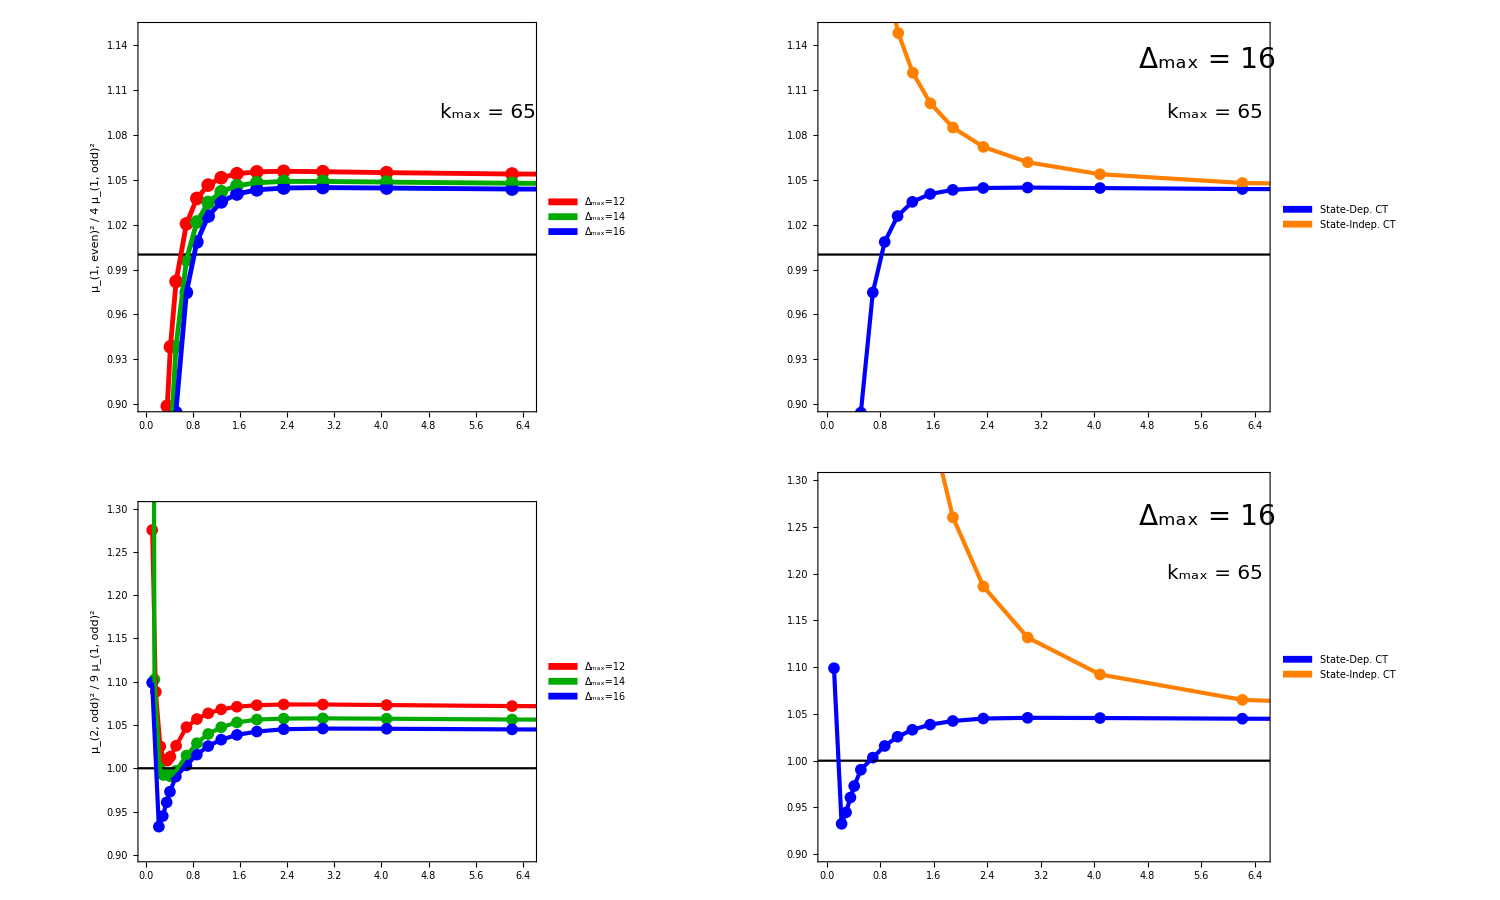
-Graphics-Spectrum: Eigenvalue Ratiosm_gap / (λ̄ m)

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2},{fig3,fig4}},ImageSize->1500,Spacings->{-30,0}],{Style["Spectrum: Eigenvalue Ratios",FontFamily->"Times",FontSize->45],Style["m_gap / (λ̄ m)",FontFamily->"Times",FontSize->40]},{Top,Bottom},Spacings->{0,0}]
```

Vary  ΛIR:

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD12IR05F1"];
Get["SpectrumD12IR025F1"];
Get["SpectrumD12IR01F1"];
```

```mathematica
ratio3D12IR05F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12IR025F1=Select[Thread[{(√(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12IR01F1=Select[Thread[{(√(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0685},{12.5323,1.07027},{6.2154,1.07182},{4.08714,1.073},{3.00558,1.07365},{2.34195,1.07365},{1.88631,1.07284},{1.54826,1.07105},{1.28203,1.06803},{1.06142,1.06345},{0.869401,1.05685},{0.692714,1.04746},{0.516608,1.02598},{0.420633,1.01348},{0.367342,1.0088},{0.307185,1.00993},{0.249848,1.02518},{0.173115,1.08825},{0.111689,1.27519}}

{{1.×10^10,1.05809},{12.5369,1.0589},{6.22465,1.05937},{4.1012,1.05928},{3.02469,1.05846},{2.36648,1.05667},{1.91676,1.05367},{1.58534,1.04914},{1.32679,1.04262},{1.11541,1.03344},{0.935131,1.02049},{0.774648,1.00179},{0.624376,0.973138},{0.549724,0.952111},{0.511708,0.938793},{0.472766,0.922736},{0.292344,0.785227},{0.243798,0.70715},{0.180382,0.528377},{0.12533,0.288242}}

{{1.×10^10,1.05517},{12.543,1.05543},{6.23678,1.05535},{4.11959,1.0547},{3.04958,1.05327},{2.39823,1.05086},{1.95589,1.04719},{1.63255,1.04197},{1.38303,1.03481},{1.18206,1.02514},{1.01419,1.01219},{0.869247,0.994705},{0.739895,0.97059},{0.679172,0.954938},{0.649486,0.945905},{0.620125,0.935895},{0.503791,0.881821},{0.381623,0.781895},{0.311865,0.683231},{0.271659,0.597143},{0.223827,0.440859},{0.200164,0.331358},{0.162599,0.172528}}

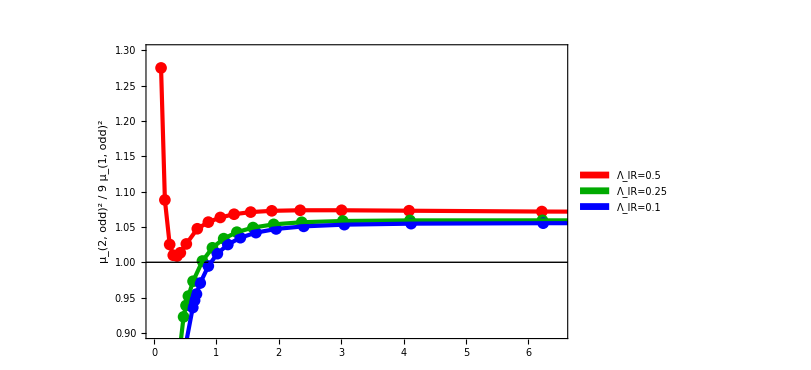

```mathematica
exper=ListPlot[{ratio3D12IR05F1,ratio3D12IR025F1,ratio3D12IR01F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2, odd)^2  /  9 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.35}]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.5","Λ_IR=0.25","Λ_IR=0.1"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,.75}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D12IR05F1,0],Drop[ratio3D12IR025F1,0],Drop[ratio3D12IR01F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

```mathematica
ratio2D12IR05F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12IR01F1=Select[Thread[{(√(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12IR01F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12IR025F1=Select[Thread[{(√(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12IR025F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.05192},{12.5323,1.05283},{6.2154,1.05381},{4.08714,1.05471},{3.00558,1.05537},{2.34195,1.05561},{1.88631,1.05525},{1.54826,1.05397},{1.28203,1.05131},{1.06142,1.0464},{0.869401,1.03751},{0.692714,1.02053},{0.516608,0.982071},{0.420633,0.938396},{0.367342,0.89872},{0.307185,0.827996},{0.249848,0.709646},{0.173115,0.337021},{0.111689,-0.650216}}

{{1.×10^10,1.02192},{12.543,1.02203},{6.23678,1.02187},{4.11959,1.02122},{3.04958,1.01979},{2.39823,1.01723},{1.95589,1.01304},{1.63255,1.00656},{1.38303,0.99695},{1.18206,0.983023},{1.01419,0.962974},{0.869247,0.933814},{0.739895,0.890138},{0.679172,0.859806},{0.649486,0.84162},{0.620125,0.820895},{0.503791,0.698938},{0.381623,0.432024},{0.311865,0.124078},{0.271659,-0.166324},{0.223827,-0.723135},{0.200164,-1.14339},{0.162599,-2.09917}}

{{1.×10^10,1.02848},{12.5369,1.02886},{6.22465,1.02904},{4.1012,1.02879},{3.02469,1.02788},{2.36648,1.02602},{1.91676,1.0228},{1.58534,1.01761},{1.32679,1.00947},{1.11541,0.996762},{0.935131,0.976661},{0.774648,0.94358},{0.624376,0.884277},{0.549724,0.834401},{0.511708,0.800109},{0.472766,0.756061},{0.389835,0.615043},{0.353438,0.520333},{0.31386,0.378788},{0.292344,0.277382},{0.269198,0.140954},{0.243798,-0.0539608},{0.180382,-0.926816},{0.12533,-2.80472}}

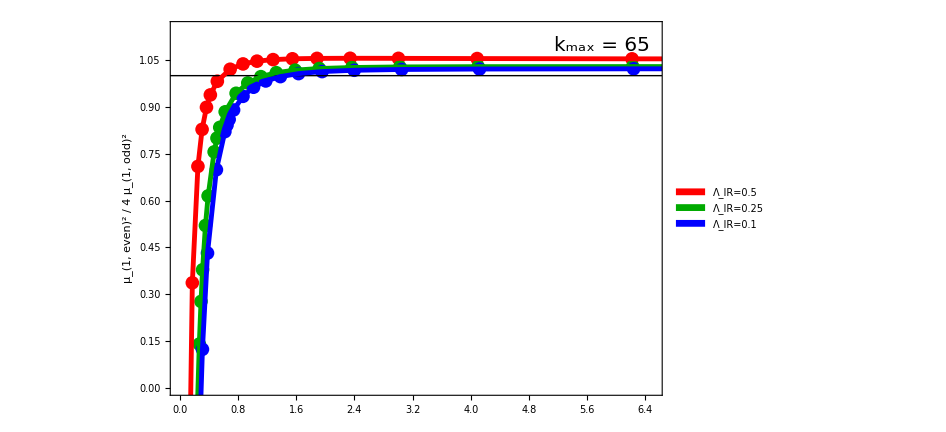

```mathematica
exper=ListPlot[{ratio2D12IR05F1,ratio2D12IR025F1,ratio2D12IR01F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(1, even)^2  /  4 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{0,1.15}},Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.5","Λ_IR=0.25","Λ_IR=0.1"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,0.21}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D12IR05F1,0],Drop[ratio2D12IR025F1,0],Drop[ratio2D12IR01F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

## Extrapolate k_max and Make Plots

```mathematica
ΛIR=0.5;
ratioWidth=8/10;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
```

```mathematica
spectrum=EvenSpectrumD16F1NOCT;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,12.5,12.75,13.,13.2,13.4,13.5}

```mathematica
iN=1;
Extrap1pD16F1NOCT=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,1.},{1.,0.994596},{2.,0.978601},{3.,0.95231},{4.,0.915982},{5.,0.869852},{6.,0.814134},{7.,0.749022},{8.,0.674697},{9.,0.591329},{10.,0.499076},{11.,0.398089},{12.,0.288513},{12.5,0.230549},{12.75,0.20078},{13.,0.170489},{13.2,0.145883},{13.4,0.120945},{13.5,0.108352}}

```mathematica
iN=2;
Extrap3pD16F1NOCT=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,9.38238},{1.,9.39351},{2.,9.40357},{3.,9.41294},{4.,9.42186},{5.,9.43052},{6.,9.43904},{7.,9.44753},{8.,9.45603},{9.,9.46461},{10.,9.47328},{11.,9.48209},{12.,9.49104},{12.5,9.49558},{12.75,9.49787},{13.,9.50017},{13.2,9.50202},{13.4,9.50388},{13.5,9.50481}}

```mathematica
spectrum=EvenSpectrumD16F1;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,12.5,12.75,13.,13.2,13.4,13.5}

```mathematica
iN=1;
Extrap2pD16F1=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,4.16919},{1.,4.14942},{2.,4.08555},{3.,3.9776},{4.,3.82537},{5.,3.62837},{6.,3.38581},{7.,3.09651},{8.,2.75879},{9.,2.37029},{10.,1.92768},{11.,1.42582},{12.,0.854869},{12.5,0.536133},{12.75,0.365014},{13.,0.182222},{13.2,0.022133},{13.4,-0.164746},{13.5,-0.283617}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD16IR05F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD16F1,EvenSpectrumD16F1,Extrap1pD16F1,Extrap2pD16F1,Extrap3pD16F1,OddSpectrumD16F1NOCT,EvenSpectrumD16F1NOCT,Extrap1pD16F1NOCT,Extrap2pD16F1NOCT,Extrap3pD16F1NOCT}];
```

```mathematica
data1p=Thread[{Extrap1pD16F1[[All,1]]/(4π),Extrap1pD16F1[[All,2]]}];
data2p=Thread[{Extrap2pD16F1[[All,1]]/(4π),Extrap2pD16F1[[All,2]]}];
data3p=Thread[{Extrap3pD16F1[[All,1]]/(4π),Extrap3pD16F1[[All,2]]}];
```

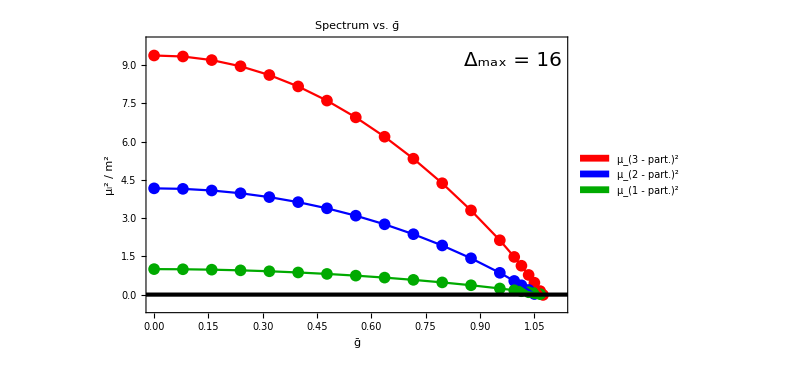

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["ḡ",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.12},{-.5,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{.99,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(3 - part.)^2","μ_(2 - part.)^2","μ_(1 - part.)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}],PlotLabel->Style["Spectrum vs. ḡ",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

```mathematica
ratio2D16F1=Select[Thread[{(√Drop[Extrap1pD16F1[[All,2]],-1])/((Drop[Extrap1pD16F1[[All,1]],-1]/(4π))+10^-10),Extrap2pD16F1[[All,2]]/(4*Drop[Extrap1pD16F1[[All,2]],-1])}],#[[1]]∈Reals&]
ratio2D16F1NOCT=Select[Thread[{(√Extrap1pD16F1NOCT[[All,2]])/((Extrap1pD16F1NOCT[[All,1]]/(4π))+10^-10),Extrap2pD16F1NOCT[[All,2]]/(4*Extrap1pD16F1NOCT[[All,2]])}],#[[1]]∈Reals&]
ratio3D16F1=Select[Thread[{(√Extrap1pD16F1[[All,2]])/((Extrap1pD16F1[[All,1]]/(4π))+10^-10),Extrap3pD16F1[[All,2]]/(9*Extrap1pD16F1[[All,2]])}],#[[1]]∈Reals&]
ratio3D16F1NOCT=Select[Thread[{(√Extrap1pD16F1NOCT[[All,2]])/((Extrap1pD16F1NOCT[[All,1]]/(4π))+10^-10),Extrap3pD16F1NOCT[[All,2]]/(9*Extrap1pD16F1NOCT[[All,2]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04299},{6.21548,1.04376},{4.08732,1.04439},{3.00586,1.04466},{2.34235,1.04431},{1.88682,1.04294},{1.54885,1.03997},{1.28265,1.03438},{1.06197,1.02436},{0.869681,1.00618},{0.692247,0.970774},{0.514016,0.887039},{0.415317,0.785332},{0.359417,0.686202},{0.294439,0.491001},{0.228655,0.0959161},{0.119147,-2.55154}}

{{1.×10^10,1.0423},{12.5324,1.04399},{6.2156,1.0478},{4.08769,1.05365},{3.00672,1.06157},{2.34403,1.0717},{1.88976,1.08434},{1.55367,1.10001},{1.29025,1.11959},{1.0737,1.14463},{0.887755,1.17809},{0.720787,1.22637},{0.562486,1.30635},{0.482704,1.37327},{0.441631,1.42057},{0.399131,1.48381},{0.363612,1.55282},{0.326136,1.64939},{0.306404,1.71413}}

{{1.×10^10,1.04249},{12.5324,1.04377},{6.21548,1.04487},{4.08732,1.04558},{3.00586,1.04575},{2.34235,1.04492},{1.88682,1.04216},{1.54885,1.03808},{1.28265,1.03231},{1.06197,1.02441},{0.869681,1.01378},{0.692247,0.999919},{0.514016,0.983743},{0.415317,0.962527},{0.359417,0.946621},{0.294439,0.923721},{0.228655,0.897498},{0.119147,0.94729}}

{{1.×10^10,1.04249},{12.5324,1.04939},{6.2156,1.06769},{4.08769,1.09826},{3.00672,1.1429},{2.34403,1.20461},{1.88976,1.28822},{1.55367,1.40146},{1.29025,1.55725},{1.0737,1.77841},{0.887755,2.10907},{0.720787,2.64656},{0.562486,3.65515},{0.482704,4.57632},{0.441631,5.2561},{0.399131,6.19144},{0.363612,7.23718},{0.326136,8.73113},{0.306404,9.74684}}

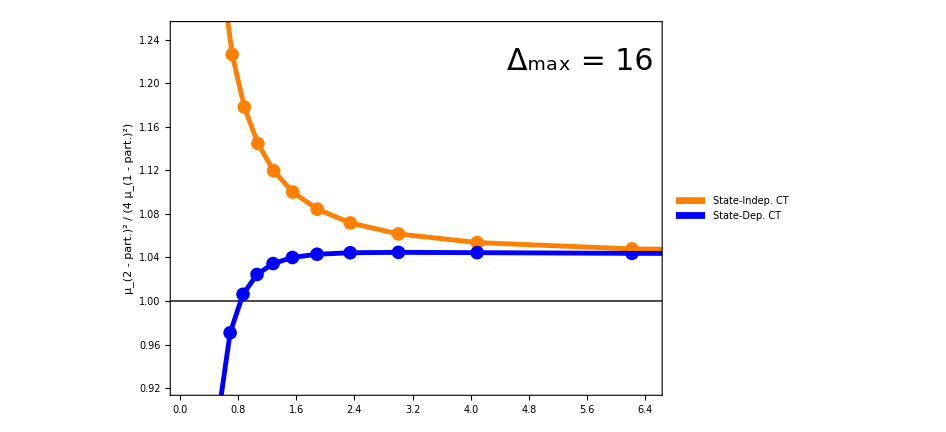

```mathematica
exper=ListPlot[{ratio2D16F1NOCT,ratio2D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Orange,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["μ_(2 - part.)^2  /  (4 μ_(1 - part.)^2)",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.92,1.25}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->30],{5.5,1.22}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"State-Indep. CT","State-Dep. CT"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.65}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio2D16F1NOCT,ratio2D16F1},PlotStyle->{{Orange,Thickness[.005]},{Blue,Thickness[.005]},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

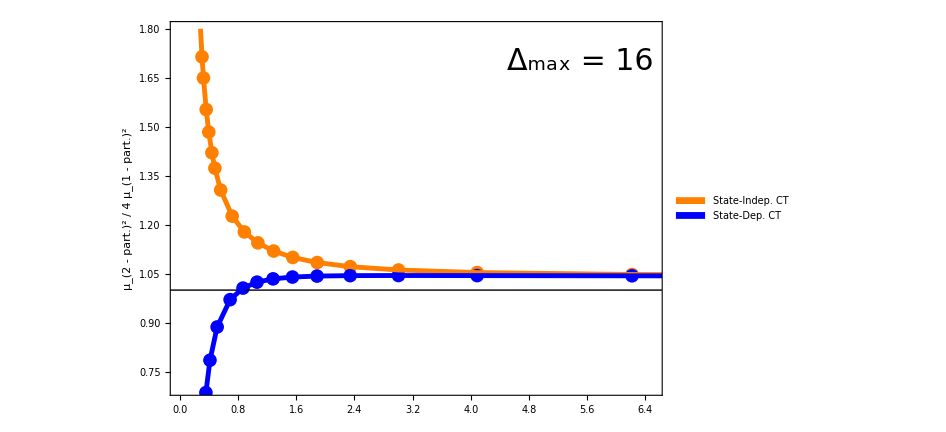

```mathematica
exper=ListPlot[{ratio2D16F1NOCT,ratio2D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Orange,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["μ_(2 - part.)^2  /  4 μ_(1 - part.)^2",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.8}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->30],{5.5,1.7}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"State-Indep. CT","State-Dep. CT"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.65}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Join[ratio2D16F1NOCT,{{0.285,1.8}}],ratio2D16F1},PlotStyle->{{Orange,Thickness[.005]},{Blue,Thickness[.005]},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
fig1ReZoom=Show[exper,line,fit]
```

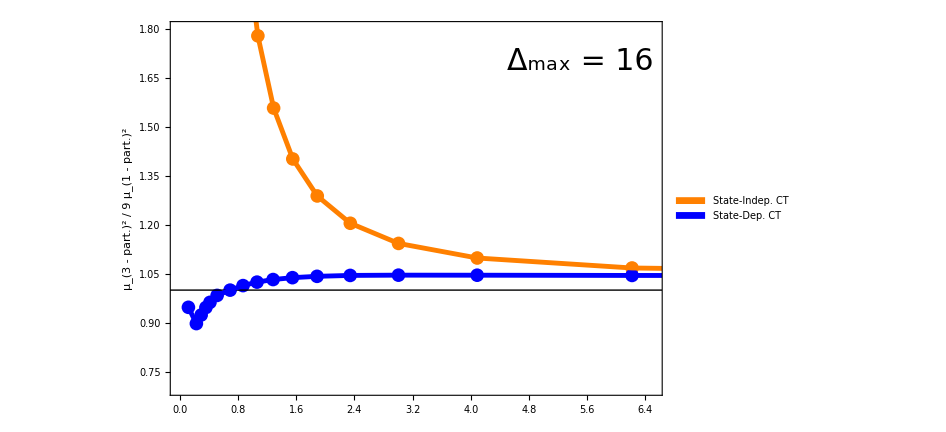

```mathematica
exper=ListPlot[{ratio3D16F1NOCT,ratio3D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Orange,PointSize[0.014]},{Blue,PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(3 - part.)^2  /  9 μ_(1 - part.)^2",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.8}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->30],{5.5,1.7}]},PlotLegends->Placed[SwatchLegend[{"State-Indep. CT","State-Dep. CT"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.65}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio3D16F1NOCT,ratio3D16F1},PlotStyle->{{Orange,Thickness[.005]},{Blue,Thickness[.005]},{Blue}},InterpolationOrder->1,PlotRange->All];
fig2=Show[exper,line,fit]
```

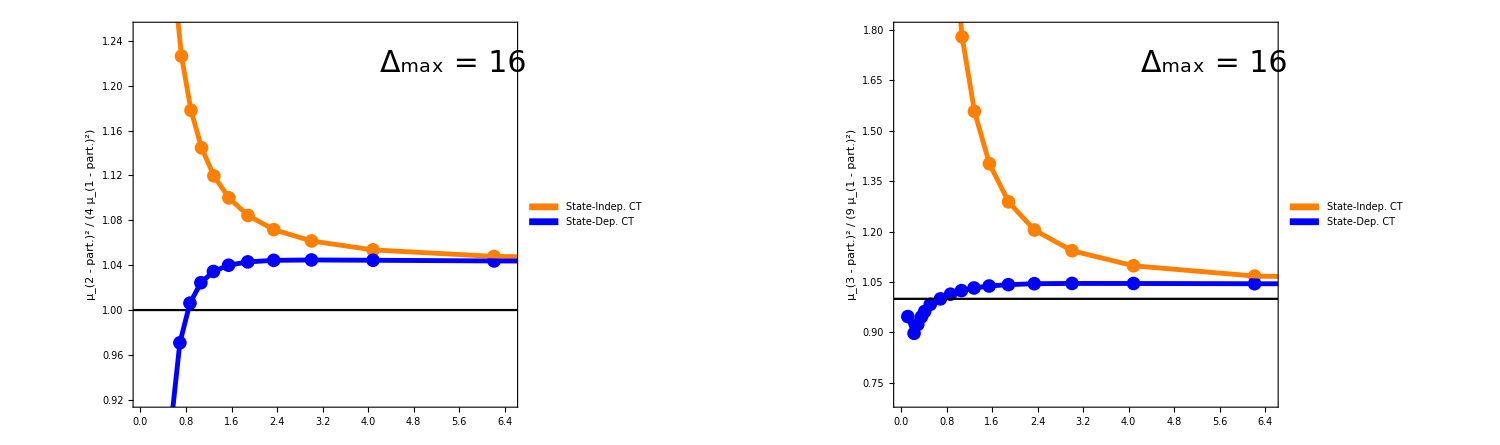
-Graphics-Spectrum: Eigenvalue Ratiosm_gap / (ḡ m)

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2}},ImageSize->1500,Spacings->{20,0}],{Style["Spectrum: Eigenvalue Ratios",FontFamily->"Times",FontSize->45],Style["m_gap / (ḡ m)",FontFamily->"Times",FontSize->35]},{Top,Bottom},RotateLabel->True]
```

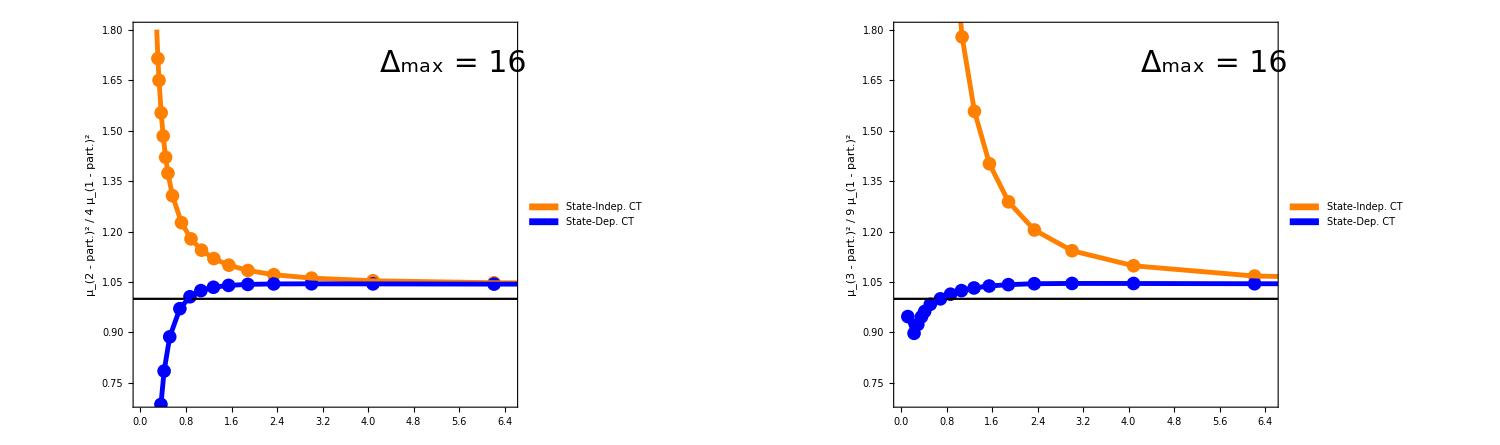
-Graphics-Spectrum: Eigenvalue Ratiosm_gap / (g/(4  π))

```mathematica
grid=Labeled[GraphicsGrid[{{fig1ReZoom,fig2}},ImageSize->1500,Spacings->{20,0}],{Style["Spectrum: Eigenvalue Ratios",FontFamily->"Times",FontSize->45],Style["m_gap / (g/(4  π))",FontFamily->"Times",FontSize->35]},{Top,Bottom},RotateLabel->True]
```

### Visual Checks:

```mathematica
test1p65=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]]}];
test1p64=Thread[{(Select[OddSpectrumD16F1,#[[2]]==64&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==64&][[All,3]]}];
test1p63=Thread[{(Select[OddSpectrumD16F1,#[[2]]==63&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==63&][[All,3]]}];
test1p62=Thread[{(Select[OddSpectrumD16F1,#[[2]]==62&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==62&][[All,3]]}];
test1p61=Thread[{(Select[OddSpectrumD16F1,#[[2]]==61&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==61&][[All,3]]}];
test1p60=Thread[{(Select[OddSpectrumD16F1,#[[2]]==60&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==60&][[All,3]]}];
extrap1p=Thread[{Extrap1pD16F1[[All,1]]/(4π),Extrap1pD16F1[[All,2]]}];


test2p65=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]]}];
test2p64=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==64&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==64&][[All,3]]}];
test2p63=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==63&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==63&][[All,3]]}];
test2p62=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==62&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==62&][[All,3]]}];
test2p61=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==61&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==61&][[All,3]]}];
test2p60=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==60&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==60&][[All,3]]}];
extrap2p=Thread[{Extrap2pD16F1[[All,1]]/(4π),Extrap2pD16F1[[All,2]]}];


test3p65=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]]}];
test3p64=Thread[{(Select[OddSpectrumD16F1,#[[2]]==64&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==64&][[All,4]]}];
test3p63=Thread[{(Select[OddSpectrumD16F1,#[[2]]==63&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==63&][[All,4]]}];
test3p62=Thread[{(Select[OddSpectrumD16F1,#[[2]]==62&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==62&][[All,4]]}];
test3p61=Thread[{(Select[OddSpectrumD16F1,#[[2]]==61&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==61&][[All,4]]}];
test3p60=Thread[{(Select[OddSpectrumD16F1,#[[2]]==60&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==60&][[All,4]]}];
extrap3p=Thread[{Extrap3pD16F1[[All,1]]/(4π),Extrap3pD16F1[[All,2]]}];
```

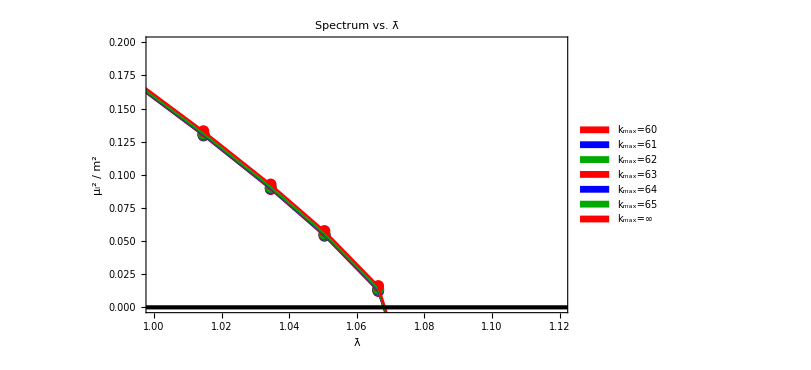

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{test1p60,test1p61,test1p62,test1p63,test1p64,test1p65,extrap1p},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{1.,1.12},{0.,.2}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"k_max=60","k_max=61","k_max=62","k_max=63","k_max=64","k_max=65","k_max=∞"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.2,0.45}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{test1p60,test1p61,test1p62,test1p63,test1p64,test1p65,extrap1p},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

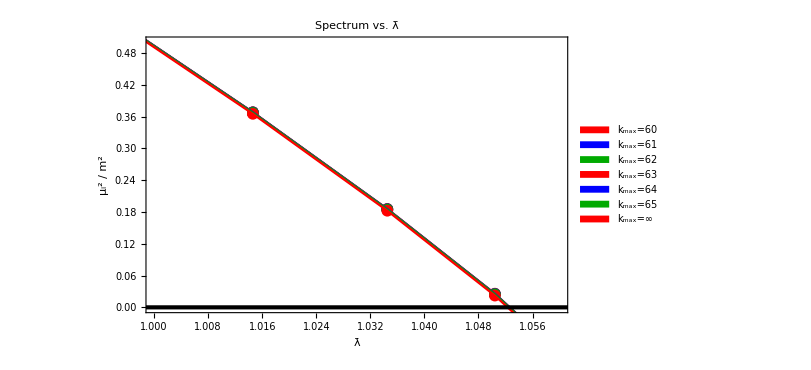

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{test2p60,test2p61,test2p62,test2p63,test2p64,test2p65,extrap2p},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{1.0,1.06},{0.,.5}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"k_max=60","k_max=61","k_max=62","k_max=63","k_max=64","k_max=65","k_max=∞"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.2,0.45}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{test2p60,test2p61,test2p62,test2p63,test2p64,test2p65,extrap2p},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

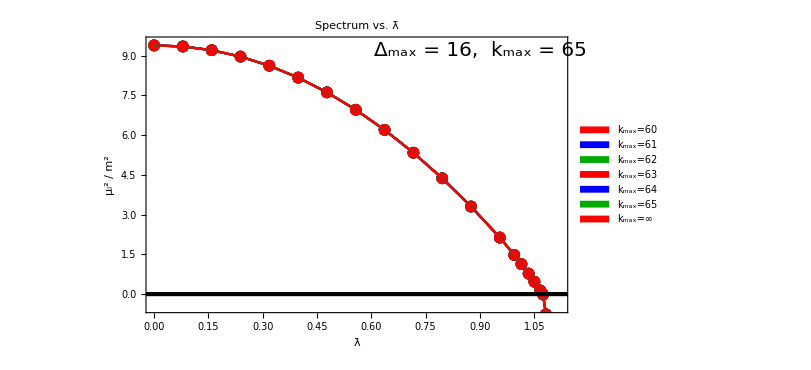

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{test3p60,test3p61,test3p62,test3p63,test3p64,test3p65,extrap3p},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.12},{-.5,9.5}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"k_max=60","k_max=61","k_max=62","k_max=63","k_max=64","k_max=65","k_max=∞"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.2,0.45}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{test3p60,test3p61,test3p62,test3p63,test3p64,test3p65,extrap3p},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

```mathematica
test1p65NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]}];
test1p64NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==64&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==64&][[All,3]]}];
test1p63NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==63&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==63&][[All,3]]}];
test1p62NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==62&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==62&][[All,3]]}];
test1p61NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==61&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==61&][[All,3]]}];
test1p60NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==60&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==60&][[All,3]]}];
extrap1pNOCT=Thread[{Extrap1pD16F1NOCT[[All,1]]/(4π),Extrap1pD16F1NOCT[[All,2]]}];


test2p65NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]}];
test2p64NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==64&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==64&][[All,3]]}];
test2p63NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==63&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==63&][[All,3]]}];
test2p62NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==62&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==62&][[All,3]]}];
test2p61NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==61&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==61&][[All,3]]}];
test2p60NOCT=Thread[{(Select[EvenSpectrumD16F1NOCT,#[[2]]==60&][[All,1]])/(4π),Select[EvenSpectrumD16F1NOCT,#[[2]]==60&][[All,3]]}];
extrap2pNOCT=Thread[{Extrap2pD16F1NOCT[[All,1]]/(4π),Extrap2pD16F1NOCT[[All,2]]}];


test3p65NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,4]]}];
test3p64NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==64&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==64&][[All,4]]}];
test3p63NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==63&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==63&][[All,4]]}];
test3p62NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==62&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==62&][[All,4]]}];
test3p61NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==61&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==61&][[All,4]]}];
test3p60NOCT=Thread[{(Select[OddSpectrumD16F1NOCT,#[[2]]==60&][[All,1]])/(4π),Select[OddSpectrumD16F1NOCT,#[[2]]==60&][[All,4]]}];
extrap3pNOCT=Thread[{Extrap3pD16F1NOCT[[All,1]]/(4π),Extrap3pD16F1NOCT[[All,2]]}];
```

```mathematica
test2p65NOCT
```

{{0.,4.16919},{0.0795775,4.1534},{0.159155,4.10147},{0.238732,4.01348},{0.31831,3.88928},{0.397887,3.72853},{0.477465,3.53071},{0.557042,3.2951},{0.63662,3.02077},{0.716197,2.7065},{0.795775,2.3508},{0.875352,1.95167},{0.95493,1.50637},{0.994718,1.26517},{1.01461,1.13962},{1.03451,1.01061},{1.05042,0.904823},{1.06634,0.796632},{1.0743,0.741604}}

```mathematica
extrap2pNOCT
```

{{0.,4.16919},{0.0795775,4.15341},{0.159155,4.10153},{0.238732,4.01361},{0.31831,3.8895},{0.397887,3.72887},{0.477465,3.53119},{0.557042,3.29573},{0.63662,3.02153},{0.716197,2.70741},{0.795775,2.35183},{0.875352,1.95281},{0.95493,1.50759},{0.994718,1.26642},{1.01461,1.14089},{1.03451,1.0119},{1.05042,0.906118},{1.06634,0.797941},{1.0743,0.742919}}

```mathematica
test3p65NOCT
extrap3pNOCT
```

{{0.,9.38238},{0.0795775,9.38764},{0.159155,9.38009},{0.238732,9.36008},{0.31831,9.32785},{0.397887,9.28357},{0.477465,9.22734},{0.557042,9.15921},{0.63662,9.0792},{0.716197,8.98731},{0.795775,8.8835},{0.875352,8.7677},{0.95493,8.6398},{0.994718,8.57128},{1.01461,8.53587},{1.03451,8.49968},{1.05042,8.47018},{1.06634,8.44017},{1.0743,8.42499}}

{{0.,9.38238},{0.0795775,9.39351},{0.159155,9.40357},{0.238732,9.41294},{0.31831,9.42186},{0.397887,9.43052},{0.477465,9.43904},{0.557042,9.44753},{0.63662,9.45603},{0.716197,9.46461},{0.795775,9.47328},{0.875352,9.48209},{0.95493,9.49104},{0.994718,9.49558},{1.01461,9.49787},{1.03451,9.50017},{1.05042,9.50202},{1.06634,9.50388},{1.0743,9.50481}}

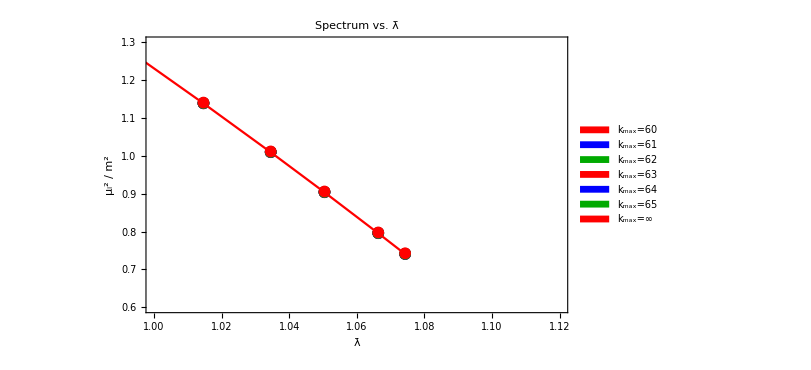

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{test2p60NOCT,test2p61NOCT,test2p62NOCT,test2p63NOCT,test2p64NOCT,test2p65NOCT,extrap2pNOCT},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{1.,1.12},{.6,1.3}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"k_max=60","k_max=61","k_max=62","k_max=63","k_max=64","k_max=65","k_max=∞"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.2,0.45}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{test2p60NOCT},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

```mathematica
test3p65NOCT
```

{{0.,9.38238},{0.0795775,9.38764},{0.159155,9.38009},{0.238732,9.36008},{0.31831,9.32785},{0.397887,9.28357},{0.477465,9.22734},{0.557042,9.15921},{0.63662,9.0792},{0.716197,8.98731},{0.795775,8.8835},{0.875352,8.7677},{0.95493,8.6398},{0.994718,8.57128},{1.01461,8.53587},{1.03451,8.49968},{1.05042,8.47018},{1.06634,8.44017},{1.0743,8.42499}}

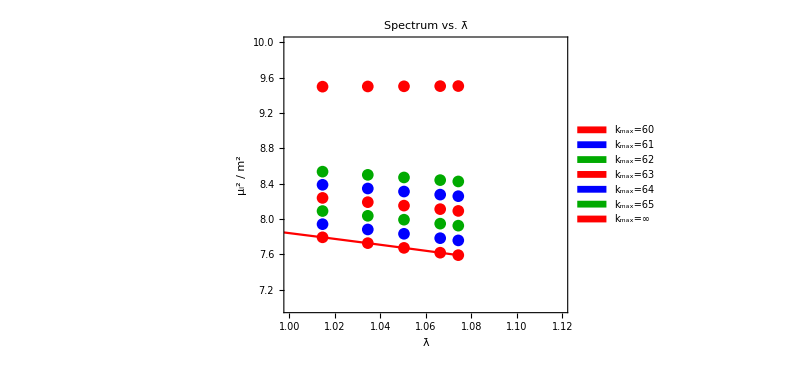

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{test3p60NOCT,test3p61NOCT,test3p62NOCT,test3p63NOCT,test3p64NOCT,test3p65NOCT,extrap3pNOCT},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{1.,1.12},{7.,10.}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"k_max=60","k_max=61","k_max=62","k_max=63","k_max=64","k_max=65","k_max=∞"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.2,0.45}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{test3p60NOCT},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

```mathematica
Thread[{(√Drop[extrap1p[[All,2]],-1])/(Drop[extrap1p[[All,1]],-1]+10^-10),extrap2p[[All,2]]/(4*Drop[extrap1p[[All,2]],-1])}]
```

{{1.×10^10,1.0423},{12.5324,1.04299},{6.21548,1.04376},{4.08732,1.04439},{3.00586,1.04466},{2.34235,1.04431},{1.88682,1.04294},{1.54885,1.03997},{1.28265,1.03438},{1.06197,1.02436},{0.869681,1.00618},{0.692247,0.970774},{0.514016,0.887039},{0.415317,0.785332},{0.359417,0.686202},{0.294439,0.491001},{0.228655,0.0959161},{0.119147,-2.55154},{0.+0.205928 ⅈ,1.44874}}

```mathematica
Thread[{(√extrap1pNOCT[[All,2]])/(extrap1pNOCT[[All,1]]+10^-10),extrap2pNOCT[[All,2]]/(4*extrap1pNOCT[[All,2]])}]
```

{{1.×10^10,1.0423},{12.5324,1.04399},{6.2156,1.0478},{4.08769,1.05365},{3.00672,1.06157},{2.34403,1.0717},{1.88976,1.08434},{1.55367,1.10001},{1.29025,1.11959},{1.0737,1.14463},{0.887755,1.17809},{0.720787,1.22637},{0.562486,1.30635},{0.482704,1.37327},{0.441631,1.42057},{0.399131,1.48381},{0.363612,1.55282},{0.326136,1.64939},{0.306404,1.71413}}

```mathematica
Thread[{(√test1p65NOCT[[All,2]])/(test1p65NOCT[[All,1]]+10^-10),test2p65NOCT[[All,2]]/(4*test1p65NOCT[[All,2]])}]
```

{{1.×10^10,1.0423},{12.5324,1.04399},{6.21556,1.0478},{4.08759,1.05367},{3.00653,1.06164},{2.34368,1.07191},{1.88921,1.08483},{1.55284,1.10099},{1.28903,1.12142},{1.07196,1.14796},{0.885296,1.18412},{0.717296,1.23761},{0.557378,1.32932},{0.47636,1.40869},{0.434474,1.46613},{0.390955,1.54456},{0.354403,1.63223},{0.315592,1.75856},{0.295024,1.84565}}

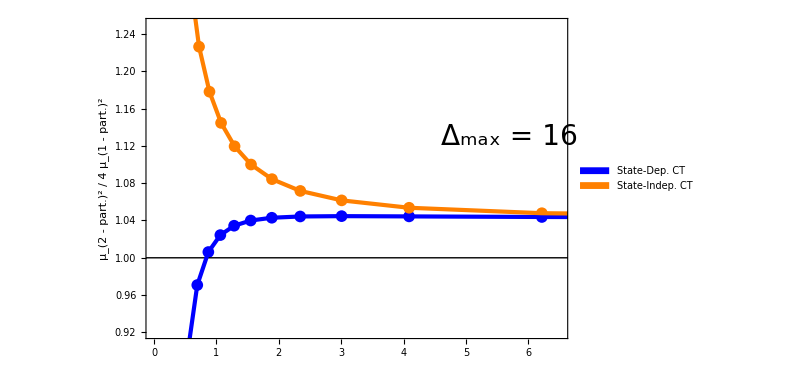

```mathematica
extrap1p
extrap1pNOCT
extrap2p
extrap2pNOCT
```

{{0.,1.},{0.0795775,0.994594},{0.159155,0.978566},{0.238732,0.952138},{0.31831,0.915458},{0.397887,0.868608},{0.477465,0.811602},{0.557042,0.744378},{0.63662,0.666773},{0.716197,0.578483},{0.795775,0.478962},{0.875352,0.367187},{0.95493,0.240933},{0.994718,0.170671},{1.01461,0.132983},{1.03451,0.0927806},{1.05042,0.0576884},{1.06634,0.0161419},{1.0743,-0.0489418},{1.08225,-0.789479}}

{{0.,1.},{0.0795775,0.994596},{0.159155,0.978601},{0.238732,0.95231},{0.31831,0.915982},{0.397887,0.869852},{0.477465,0.814134},{0.557042,0.749022},{0.63662,0.674697},{0.716197,0.591329},{0.795775,0.499076},{0.875352,0.398089},{0.95493,0.288513},{0.994718,0.230549},{1.01461,0.20078},{1.03451,0.170489},{1.05042,0.145883},{1.06634,0.120945},{1.0743,0.108352}}

{{0.,4.16919},{0.0795775,4.14942},{0.159155,4.08555},{0.238732,3.9776},{0.31831,3.82537},{0.397887,3.62837},{0.477465,3.38581},{0.557042,3.09651},{0.63662,2.75879},{0.716197,2.37029},{0.795775,1.92768},{0.875352,1.42582},{0.95493,0.854869},{0.994718,0.536133},{1.01461,0.365014},{1.03451,0.182222},{1.05042,0.022133},{1.06634,-0.164746},{1.0743,-0.283617}}

{{0.,4.16919},{0.0795775,4.15341},{0.159155,4.10153},{0.238732,4.01361},{0.31831,3.8895},{0.397887,3.72887},{0.477465,3.53119},{0.557042,3.29573},{0.63662,3.02153},{0.716197,2.70741},{0.795775,2.35183},{0.875352,1.95281},{0.95493,1.50759},{0.994718,1.26642},{1.01461,1.14089},{1.03451,1.0119},{1.05042,0.906118},{1.06634,0.797941},{1.0743,0.742919}}

```mathematica
0.36501357862355155/(4*0.13298332921489062)
```

0.686202

{{0.00123794,7.85726},{0.00110725,8.00012},{0.000990353,8.14295},{0.000885798,8.28576},{0.000792282,8.42853},{0.000708638,8.57128}}

{12.5,9.49558}

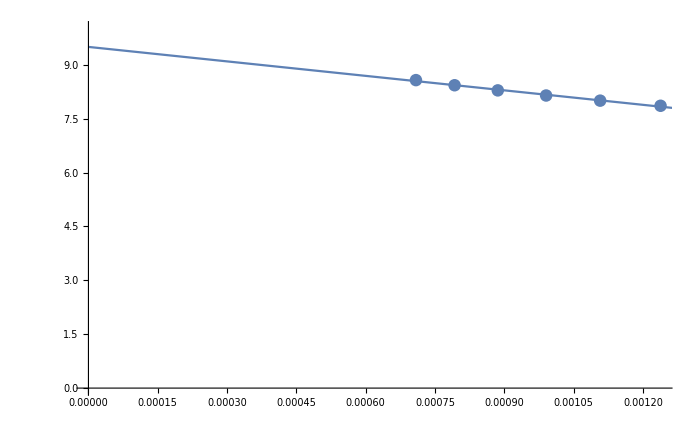

```mathematica
(* Visual Check *)
spectrum=OddSpectrumD16F1NOCT;
iN=2;
iG=14;
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}]
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim}

fit=FindFit[temp2,a*x+b,{a,b},x];
fitplot=Plot[a*x+b/.fit,{x,0,1}];
plot=ListPlot[temp2,ImageSize->700,AxesOrigin->{0,0},PlotRange->{All,{0,10}}];
Show[plot,fitplot]
```

## Scratch

### Spectrum

```mathematica
SetDirectory[NotebookDirectory[]];
Get["OddSpectrumD16F1"];
```

```mathematica
data1p=Thread[{Extrap1pD16[[All,1]]/(4π),Extrap1pD16[[All,2]]}];
data3p=Thread[{Extrap3pD16[[All,1]]/(4π),Extrap3pD16[[All,2]]}];
```

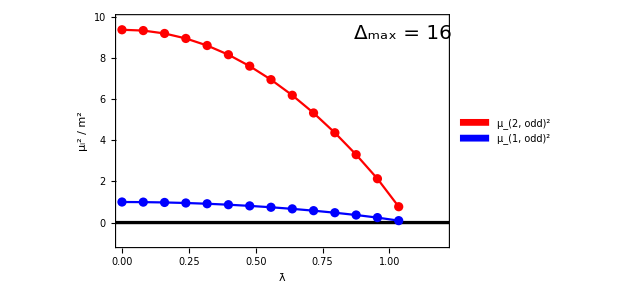

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{data3p,data1p},Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,1.2},{-1,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]];
fit=ListLinePlot[{data3p,data1p},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

### Ratio

```mathematica
Extrap1pD16
```

{{0.,1.},{1.,0.994594},{2.,0.978566},{3.,0.952138},{4.,0.915458},{5.,0.868608},{6.,0.811602},{7.,0.744378},{8.,0.666773},{9.,0.578483},{10.,0.478962},{11.,0.367187},{12.,0.240933},{13.,0.0927806}}

```mathematica
ratio3D16=Thread[{(√Extrap1pD16[[All,2]])/((Extrap1pD16[[All,1]]/(4π))+10^-10),Extrap3pD16[[All,2]]/(9*Extrap1pD16[[All,2]])}]
```

{{1.×10^10,1.04249},{12.5324,1.04377},{6.21548,1.04487},{4.08732,1.04558},{3.00586,1.04575},{2.34235,1.04492},{1.88682,1.04216},{1.54885,1.03808},{1.28265,1.03231},{1.06197,1.02441},{0.869681,1.01378},{0.692247,0.999919},{0.514016,0.983743},{0.294439,0.923721}}

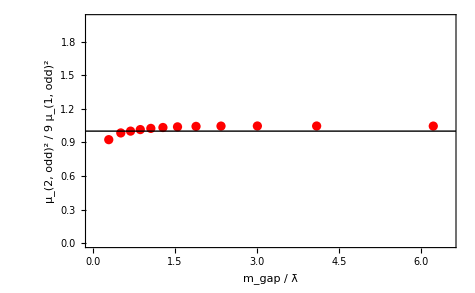

```mathematica
exper=ListPlot[{ratio3D16},Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["m_gap / λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_(2, odd)^2 / 9 μ_(1, odd)^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,6.5},{0,2}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*)];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
Show[exper,line]
```

### Ratio w/o NLCT

```mathematica
ratio3D16F1=Thread[{(√Extrap1pD16[[All,2]])/((Extrap1pD16[[All,1]]/(4π))+10^-10),Extrap3pD16[[All,2]]/(9*Extrap1pD16[[All,2]])}]
```

{{1.×10^10,1.04249},{12.5324,1.04377},{6.21548,1.04487},{4.08732,1.04558},{3.00586,1.04575},{2.34235,1.04492},{1.88682,1.04216},{1.54885,1.03808},{1.28265,1.03231},{1.06197,1.02441},{0.869681,1.01378},{0.692247,0.999919},{0.514016,0.983743},{0.294439,0.923721}}

```mathematica
ratio3D16F1NOCT=Thread[{(√OddSpectrumD16F1NOCT[[All,3]])/((OddSpectrumD16F1NOCT[[All,1]]/(4π))+10^-10),OddSpectrumD16F1NOCT[[All,4]]/(9*OddSpectrumD16F1NOCT[[All,3]])}]
```

{{1.×10^10,1.04249},{12.5324,1.04874},{6.21556,1.06503},{4.08759,1.09214},{3.00653,1.13164},{2.34368,1.18619},{1.88921,1.26006},{1.55284,1.36015},{1.28903,1.49802},{1.07196,1.69421},{0.885296,1.98877},{0.717296,2.47104},{0.557378,3.38859},{0.390955,5.77351}}

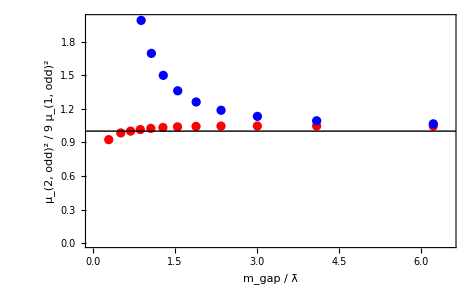

```mathematica
exper=ListPlot[{ratio3D16,ratio3D16F1NOCT},Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["m_gap / λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_(2, odd)^2 / 9 μ_(1, odd)^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,6.5},{0,2}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*)];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
Show[exper,line]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["OddSpectrumD16VaryF"];
```

```mathematica
ratio3D16F075=Select[Thread[{(√OddSpectrumD16F075[[All,3]])/((OddSpectrumD16F075[[All,1]]/(4π))+10^-10),OddSpectrumD16F075[[All,4]]/(9*OddSpectrumD16F075[[All,3]])}],#[[1]]∈Reals&]
ratio3D16F1=Select[Thread[{(√(Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D16F11=Select[Thread[{(√OddSpectrumD16F11[[All,3]])/((OddSpectrumD16F11[[All,1]]/(4π))+10^-10),OddSpectrumD16F11[[All,4]]/(9*OddSpectrumD16F11[[All,3]])}],#[[1]]∈Reals&]
ratio3D16F12=Select[Thread[{(√OddSpectrumD16F12[[All,3]])/((OddSpectrumD16F12[[All,1]]/(4π))+10^-10),OddSpectrumD16F12[[All,4]]/(9*OddSpectrumD16F12[[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.04249},{12.541,1.04375},{6.23281,1.04478},{4.11365,1.04536},{3.04163,1.0453},{2.38819,1.04426},{1.94363,1.04112},{1.61787,1.03652},{1.36567,1.03011},{1.1616,1.0214},{0.99006,1.00967},{0.840542,0.993881},{0.705138,0.972273},{0.576604,0.941688}}

{{1.×10^10,1.04249},{12.5324,1.04378},{6.21546,1.04488},{4.08726,1.04561},{3.00576,1.04582},{2.34219,1.04506},{1.88658,1.04242},{1.54851,1.03852},{1.2822,1.03304},{1.06135,1.0256},{0.868841,1.01574},{0.691084,1.00329},{0.512297,0.990357},{0.291141,0.944771}}

{{1.×10^10,1.04249},{12.5289,1.04378},{6.20851,1.04492},{4.07666,1.04572},{2.99129,1.04604},{2.32353,1.04541},{1.86327,1.04301},{1.51986,1.03946},{1.24718,1.03456},{1.01833,1.0281},{0.81493,1.02028},{0.620193,1.01368},{0.405887,1.01084}}

{{2.97675,1.04626},{2.30472,1.04577},{1.83964,1.04362},{1.49063,1.04051},{1.2111,1.03633},{0.973299,1.03132},{0.75686,1.02711},{0.538862,1.03496},{0.246685,1.14351}}

```mathematica
ratio2D16F1=Select[Thread[{(√(Drop[Select[OddSpectrumD16F1,#[[2]]==65&],-1][[All,3]]))/(((Drop[Select[OddSpectrumD16F1,#[[2]]==65&],-1][[All,1]])/(4π))+10^-10),EvenSpectrumD16F1[[All,3]]/(4*Drop[Select[OddSpectrumD16F1,#[[2]]==65&],-1][[All,3]])}],#[[1]]∈Reals&]
ratio2D16F11=Select[Thread[{(√(Drop[OddSpectrumD16F11,4][[All,3]]))/(((Drop[OddSpectrumD16F11,4][[All,1]])/(4π))+10^-10),EvenSpectrumD16F11[[All,3]]/(4*Drop[OddSpectrumD16F11,4][[All,3]])}],#[[1]]∈Reals&]
ratio2D16F12=Select[Thread[{(√OddSpectrumD16F12[[All,3]])/((OddSpectrumD16F12[[All,1]]/(4π))+10^-10),EvenSpectrumD16F12[[All,3]]/(4*OddSpectrumD16F12[[All,3]])}],#[[1]]∈Reals&]
ratio2D16F13=Select[Thread[{(√OddSpectrumD16F13[[All,3]])/((OddSpectrumD16F13[[All,1]]/(4π))+10^-10),EvenSpectrumD16F13[[All,3]]/(4*OddSpectrumD16F13[[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04299},{6.21546,1.04377},{4.08726,1.04442},{3.00576,1.04473},{2.34219,1.04445},{1.88658,1.04322},{1.54851,1.04045},{1.2822,1.0352},{1.06135,1.02571},{0.868841,1.00843},{0.691084,0.974674},{0.512297,0.89443},{0.413088,0.796268},{0.35678,0.699831},{0.291141,0.507654},{0.22432,0.109258},{0.110619,-2.91956}}

{{2.99129,1.04509},{2.32353,1.04508},{1.86327,1.04421},{1.51986,1.04193},{1.24718,1.03724},{1.01833,1.0282},{0.81493,1.0104},{0.620193,0.970711},{0.405887,0.838196}}

{{2.97675,1.04546},{2.30472,1.04572},{1.83964,1.04525},{1.49063,1.04353},{1.2111,1.03955},{0.973299,1.03123},{0.75686,1.01314},{0.538862,0.964459},{0.246685,0.570683}}

{{0.440467,0.952143}}

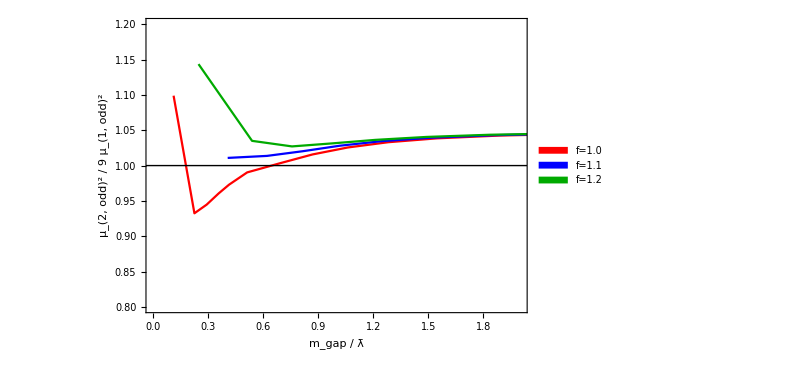

```mathematica
exper=ListPlot[{ratio3D16F1,ratio3D16F11,ratio3D16F12},Frame->True,FrameStyle->Thickness[0.002],Joined->True,PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["m_gap / λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_(2, odd)^2 / 9 μ_(1, odd)^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,2},{.8,1.2}},Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{5.5,1.08}]},PlotLegends->Placed[SwatchLegend[{"f=1.0","f=1.1","f=1.2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.25}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
oddratio=Show[exper,line]
```

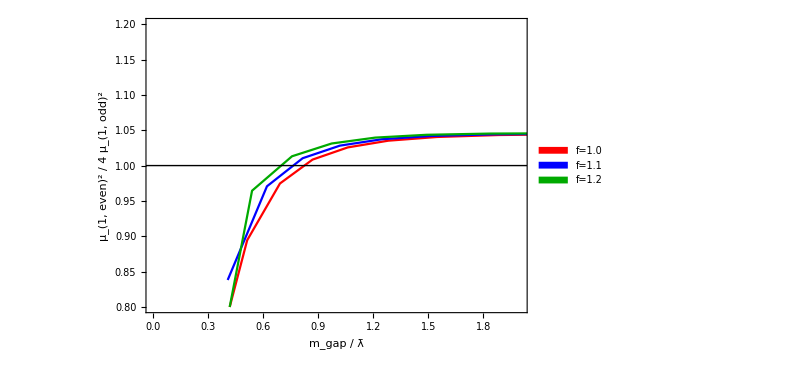

```mathematica
exper=ListPlot[{ratio2D16F1,ratio2D16F11,ratio2D16F12},Frame->True,FrameStyle->Thickness[0.002],Joined->True,PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["m_gap / λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_(1, even)^2 / 4 μ_(1, odd)^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,2},{.8,1.2}},Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{5.5,1.08}]},PlotLegends->Placed[SwatchLegend[{"f=1.0","f=1.1","f=1.2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.25}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
evenratio=Show[exper,line]
```

```mathematica
{{evenratio,oddratio}}
```

{{-Graphics-,-Graphics-}}

## Even Spectral Densities @ μ_(1,even)=1.25

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD14IR05F1"];
Get["SpectrumD12IR05F1"];
```

```mathematica
couplingMapD16=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD14=Interpolation[Select[Thread[{Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD14F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD12=Interpolation[Select[Thread[{Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD12F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{16,couplingMapD16[1.25^2]},{14,couplingMapD14[1.25^2]},{12,couplingMapD12[1.25^2]}}
{{16,couplingMapD16[1.25^2]/(4π)},{14,couplingMapD14[1.25^2]/(4π)},{12,couplingMapD12[1.25^2]/(4π)}}
```

{{16,10.7418},{14,10.8093},{12,10.8795}}

{{16,0.854807},{14,0.860179},{12,0.865762}}

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 14.1865

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=10.741815826692092;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 22.9913

```mathematica
ϕ2SpecD16=ϕ2IntegratedSpec;
ϕ4SpecD16=ϕ4IntegratedSpec;
ϕ6SpecD16=ϕ6IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesIR05F1Gap125";
DeleteFile[filename];
Save[filename,{ϕ2SpecD12,ϕ4SpecD12,ϕ6SpecD12,ϕ2SpecD14,ϕ4SpecD14,ϕ6SpecD14,ϕ2SpecD16,ϕ4SpecD16,ϕ6SpecD16}];
```

DeleteFile::fdnfnd: Directory or file EvenSpectralDensitiesIR05F1Gap125 not found.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap125"];
```

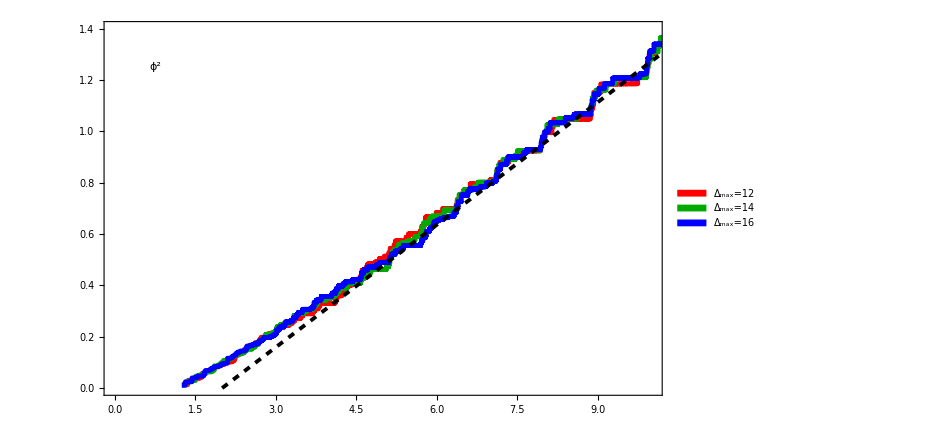

```mathematica
temp=ListLinePlot[{ϕ2SpecD12,ϕ2SpecD14,ϕ2SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-2)^(n-1)
FreePlot=Plot[FreeProfile[2,μsq],{μsq,2,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot1=Show[temp,FreePlot]
```

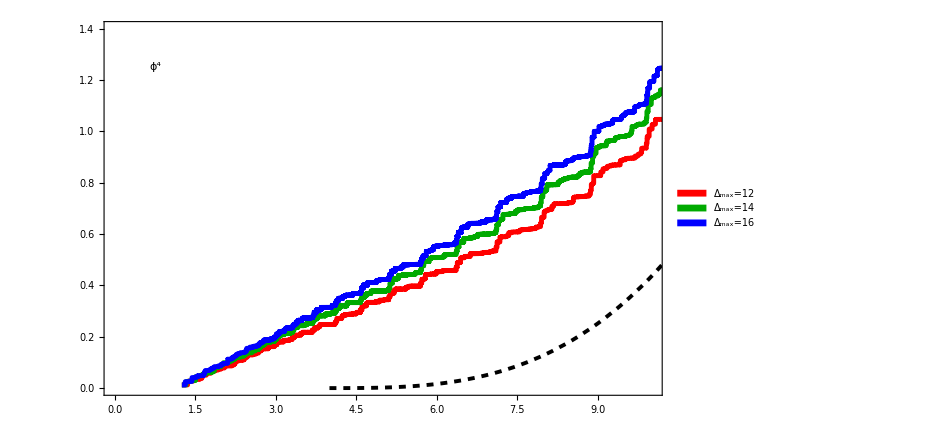

```mathematica
temp=ListLinePlot[{ϕ4SpecD12,ϕ4SpecD14,ϕ4SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2=Show[temp,FreePlot]
```

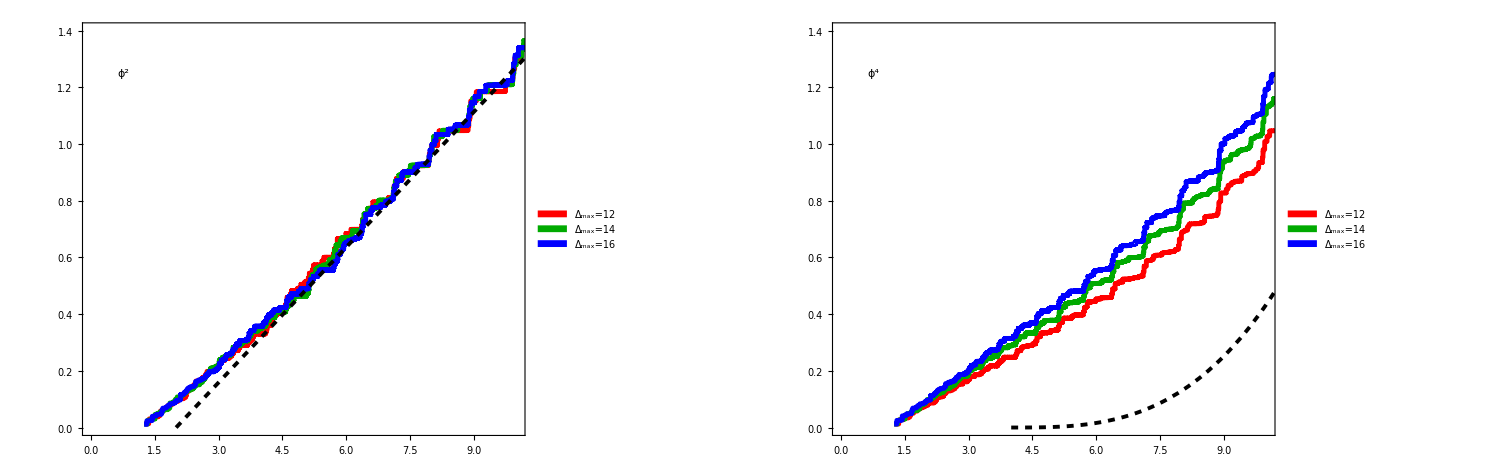
-Graphics-Spectral Densities at Strong Couplingϕ^n Integrated Spectral Densityμ / m

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2}},ImageSize->1500,Spacings->{0,0}],{Style["Spectral Densities at Strong Coupling",FontFamily->"Times",FontSize->45],Style["ϕ^n Integrated Spectral Density",FontFamily->"Times",FontSize->35],Style["μ / m",FontFamily->"Times",FontSize->35]},{Top,Left,Bottom},RotateLabel->True]
```

```mathematica
temp=ListLinePlot[{ϕ6SpecD12,ϕ6SpecD14,ϕ6SpecD16},Frame->True,FrameStyle->{Black,Thickness[0.002]},FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.5}},LabelStyle->Black];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-ϕ6SpecD12[[1,1]])^(n-1)
FreePlot=Plot[FreeProfile[6,μsq],{μsq,ϕ6SpecD12[[1,1]],100},PlotStyle->{Black}];
Show[temp,FreePlot];
```

```mathematica
√(.25)
```

0.5

## Even Spectral Densities @ μ_(1,even)=1.25, Vary Λ_IR

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD16IR075F1"];
Get["SpectrumD12IR025F1"];
```

```mathematica
couplingMapIR05=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapIR075=Interpolation[Select[Thread[{Select[EvenSpectrumD16IR075F1,#[[2]]==63&][[All,3]],Select[EvenSpectrumD16IR075F1,#[[2]]==63&][[All,1]]}],#[[1]]>0&]];
couplingMapIR025=Interpolation[Select[Thread[{Select[EvenSpectrumD12IR025F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD12IR025F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{.5,couplingMapIR05[1.25^2]},{.75,couplingMapIR075[1.25^2]},{.25,couplingMapIR025[1.25^2]}}
{{.5,couplingMapIR05[1.25^2]/(4π)},{.75,couplingMapIR075[1.25^2]/(4π)},{.25,couplingMapIR025[1.25^2]/(4π)}}
```

{{0.5,10.7418},{0.75,11.1252},{0.25,10.6141}}

{{0.5,0.854807},{0.75,0.885317},{0.25,0.844641}}

```mathematica
Δmax=8;
kmax=65;
sector="even";

m=1.;
ΛIR=0.75;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.00263265

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
(* ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax]; *)

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

6

```mathematica
t1=AbsoluteTime[];

g=11.12522361220429;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
(* ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}]; *)


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.00318248

```mathematica
ϕ2SpecD8IR075=ϕ2IntegratedSpec;
ϕ4SpecD8IR075=ϕ4IntegratedSpec;
(* ϕ6SpecD16IR025=ϕ6IntegratedSpec; *)
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesIR025F1Gap125";
DeleteFile[filename];
Save[filename,{ϕ2SpecD16IR025,ϕ4SpecD16IR025,ϕ6SpecD16IR025}];
```

DeleteFile::fdnfnd: Directory or file EvenSpectralDensitiesIR025F1Gap125 not found.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap125"];
Get["EvenSpectralDensitiesIR075F1Gap125"];
Get["EvenSpectralDensitiesIR025F1Gap125"];
```

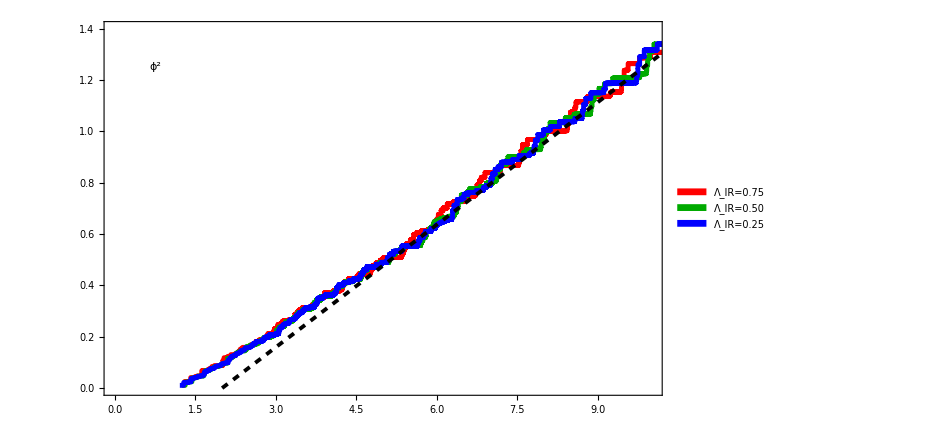

```mathematica
temp=ListLinePlot[{ϕ2SpecD16IR075,ϕ2SpecD16,ϕ2SpecD16IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-2)^(n-1)
FreePlot=Plot[FreeProfile[2,μsq],{μsq,2,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot1=Show[temp,FreePlot]
```

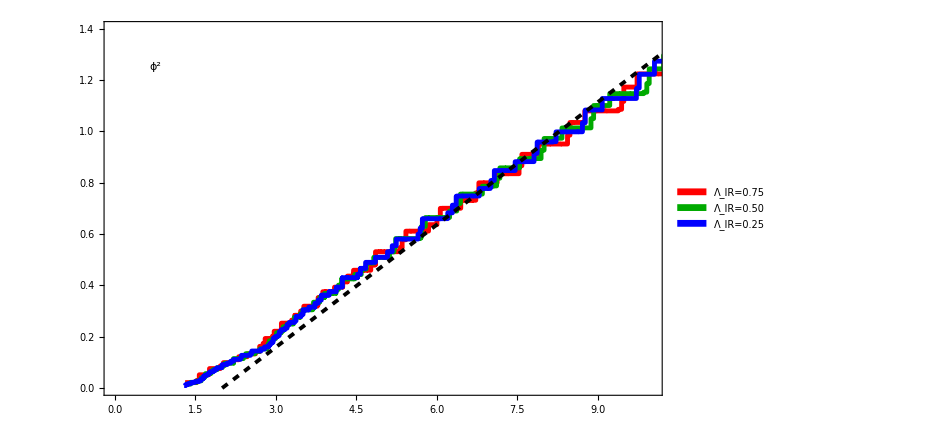

```mathematica
temp=ListLinePlot[{ϕ2SpecD8IR075,ϕ2SpecD8IR05,ϕ2SpecD8IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-2)^(n-1)
FreePlot=Plot[FreeProfile[2,μsq],{μsq,2,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot1=Show[temp,FreePlot]
```

```mathematica
ϕ4SpecD16IR075Rescaled=Thread[{ϕ4SpecD16IR075[[All,1]],ϕ4SpecD16IR075[[All,2]]*.77}];
ϕ4SpecD16IR025Rescaled=Thread[{ϕ4SpecD16IR025[[All,1]],ϕ4SpecD16IR025[[All,2]]*1.4}];
```

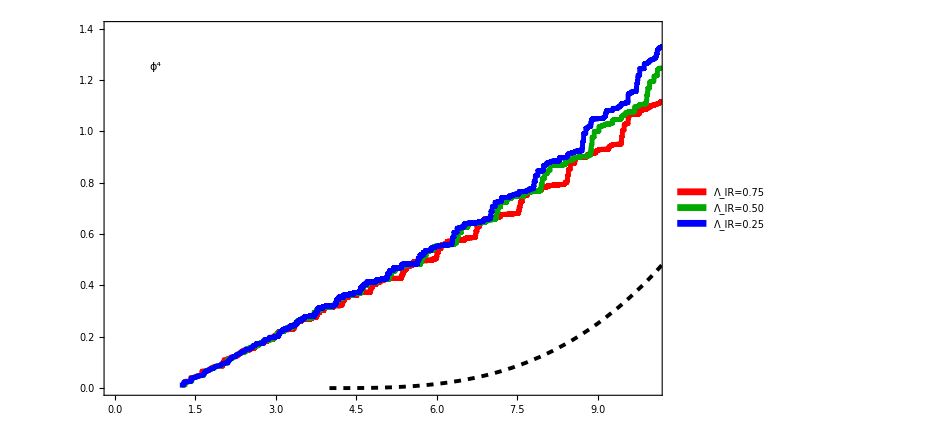

```mathematica
temp=ListLinePlot[{ϕ4SpecD16IR075Rescaled,ϕ4SpecD16,ϕ4SpecD16IR025Rescaled},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2D16=Show[temp,FreePlot]
```

```mathematica
ϕ4SpecD8IR075Rescaled=Thread[{ϕ4SpecD8IR075[[All,1]],ϕ4SpecD8IR075[[All,2]]*.77}];
ϕ4SpecD8IR025Rescaled=Thread[{ϕ4SpecD8IR025[[All,1]],ϕ4SpecD8IR025[[All,2]]*1.4}];
```

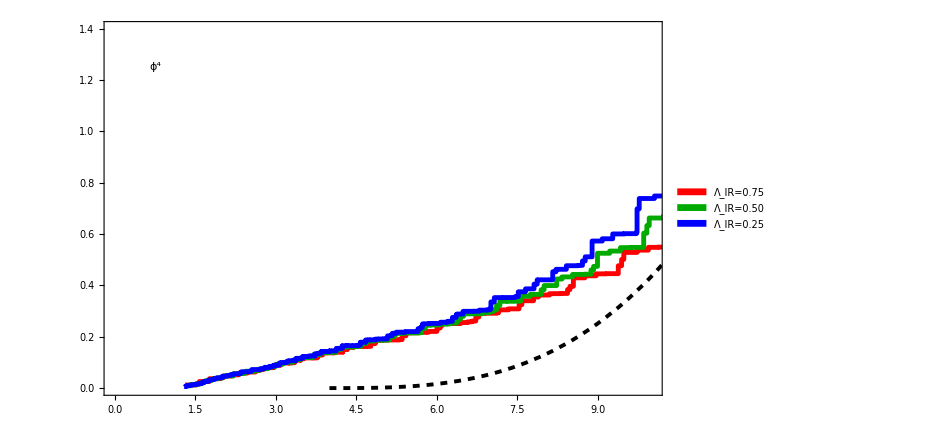

```mathematica
temp=ListLinePlot[{ϕ4SpecD8IR075Rescaled,ϕ4SpecD8IR05,ϕ4SpecD8IR025Rescaled},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2D8=Show[temp,FreePlot]
```

```mathematica
ϕ4SpecD8IR05Rescaled=Thread[{ϕ4SpecD8IR05[[All,1]],ϕ4SpecD8IR05[[All,2]]*2.25}];
```

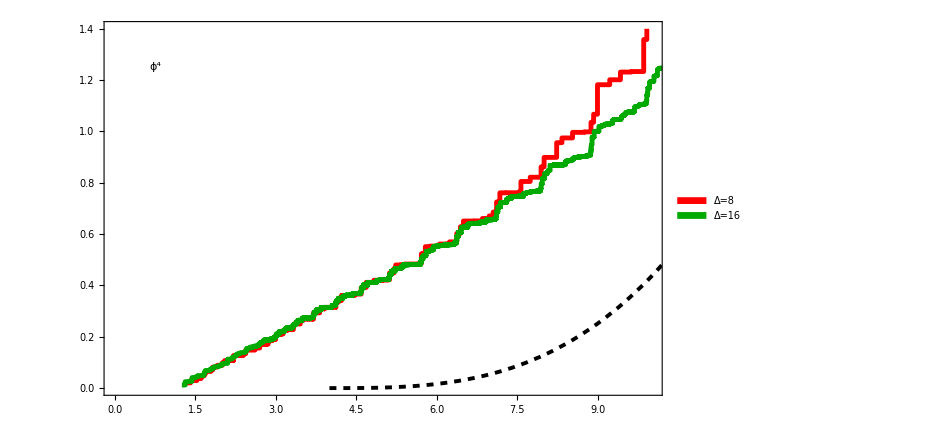

```mathematica
temp=ListLinePlot[{ϕ4SpecD8IR05Rescaled,ϕ4SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ=8","Δ=16","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2D8=Show[temp,FreePlot]
```

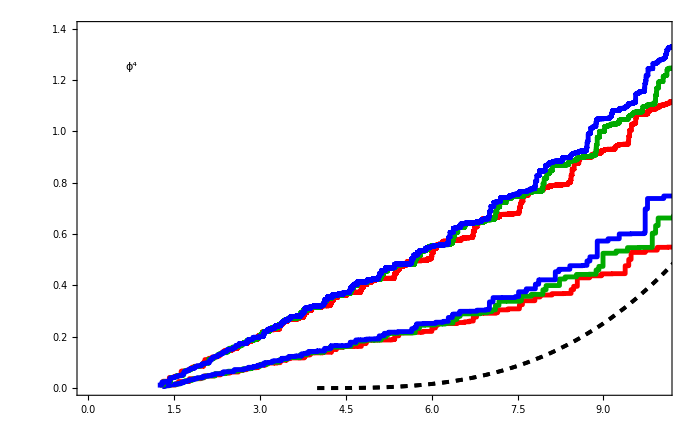

```mathematica
Show[plot2D8,plot2D16]
```

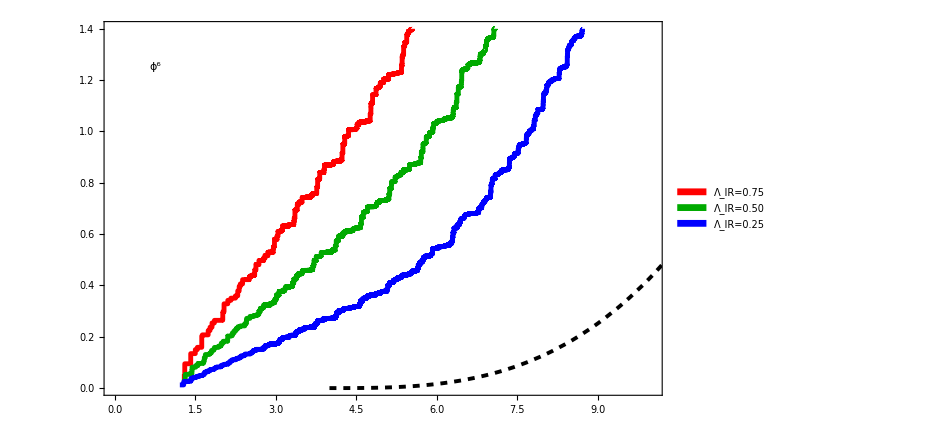

```mathematica
temp=ListLinePlot[{ϕ6SpecD16IR075,ϕ6SpecD16,ϕ6SpecD16IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^6",FontFamily->"Times"],{.75,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2=Show[temp,FreePlot]
```

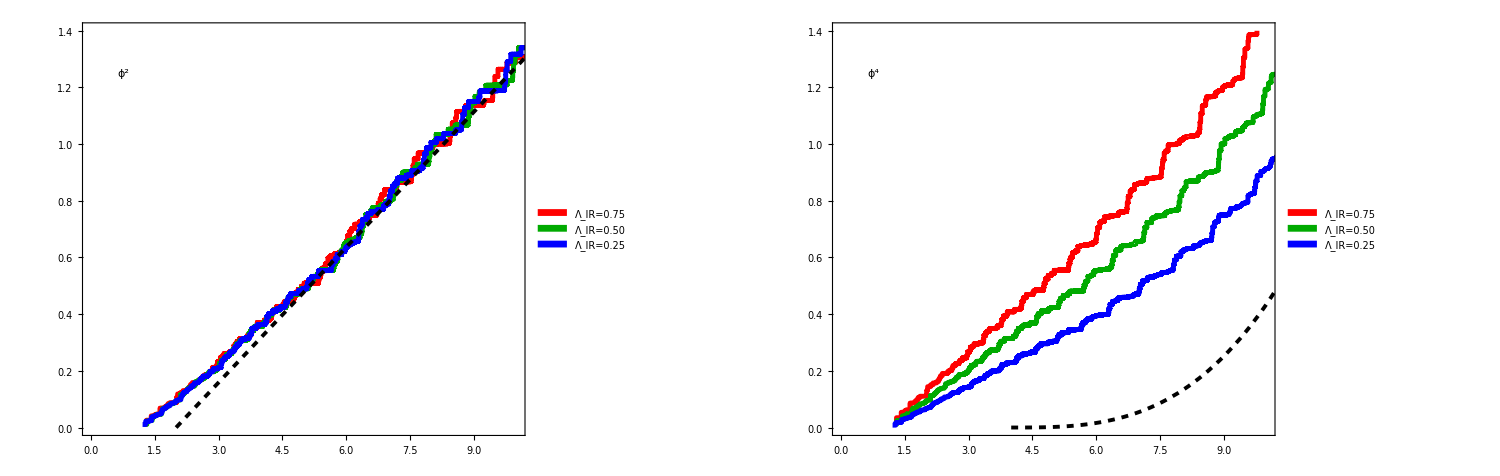
-Graphics-Spectral Densities at Strong Coupling: Varying Parametersϕ^n Integrated Spectral Densityμ / m

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2}},ImageSize->1500,Spacings->{0,0}],{Style["Spectral Densities at Strong Coupling: Varying Parameters",FontFamily->"Times",FontSize->45],Style["ϕ^n Integrated Spectral Density",FontFamily->"Times",FontSize->35],Style["μ / m",FontFamily->"Times",FontSize->35]},{Top,Left,Bottom},RotateLabel->True]
```

## Even Spectral Densities @ μ_(1,even)=0.5

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16F1"];
Get["SpectrumD14F1"];
Get["SpectrumD12F1"];
```

```mathematica
couplingMapD16F1=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD14F1=Interpolation[Select[Thread[{Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD14F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD12F1=Interpolation[Select[Thread[{Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD12F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{16,couplingMapD16F1[.25]},{14,couplingMapD14F1[.25]},{12,couplingMapD12F1[.25]}}
```

{{16,12.9123},{14,13.0214},{12,13.123}}

```mathematica
12.912309172486772/(4π)
```

1.02753

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 13.0265

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=12.912309172486772;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 23.0212

```mathematica
ϕ2SpecD16=ϕ2IntegratedSpec;
ϕ4SpecD16=ϕ4IntegratedSpec;
ϕ6SpecD16=ϕ6IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesF1GapSquared025";
DeleteFile[filename];
Save[filename,{ϕ2SpecD12,ϕ4SpecD12,ϕ6SpecD12,ϕ2SpecD14,ϕ4SpecD14,ϕ6SpecD14,ϕ2SpecD16,ϕ4SpecD16,ϕ6SpecD16}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap05"];
```

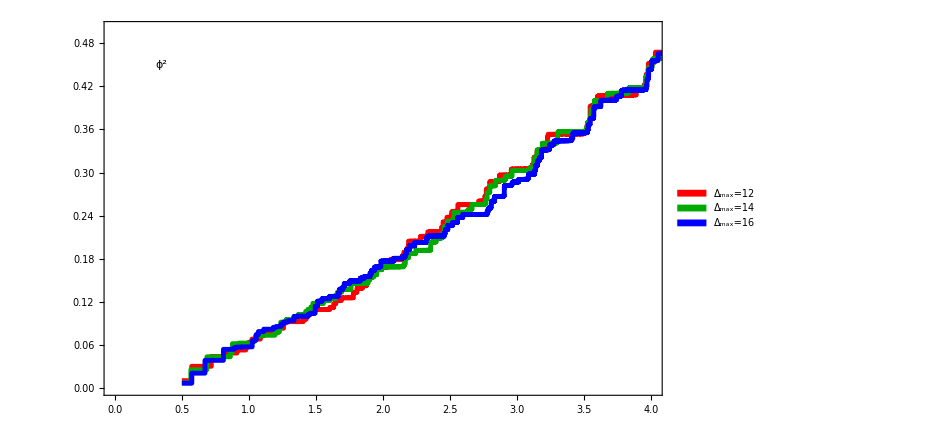

```mathematica
temp=ListLinePlot[{ϕ2SpecD12,ϕ2SpecD14,ϕ2SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

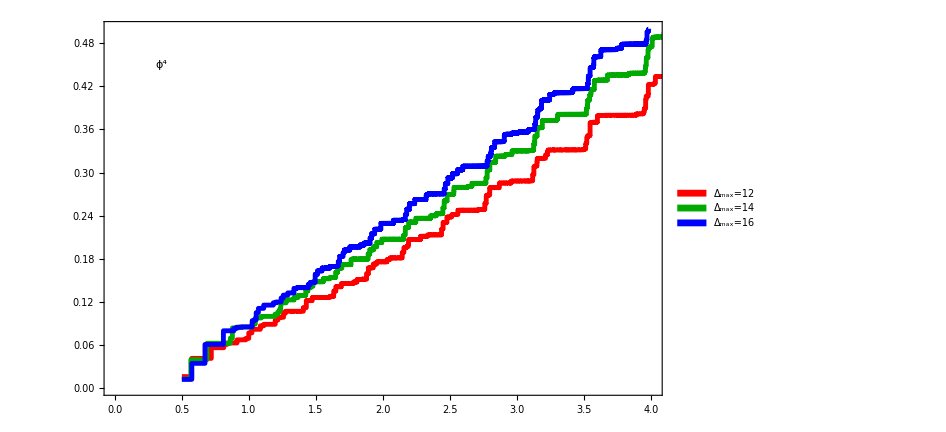

```mathematica
temp=ListLinePlot[{ϕ4SpecD12,ϕ4SpecD14,ϕ4SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

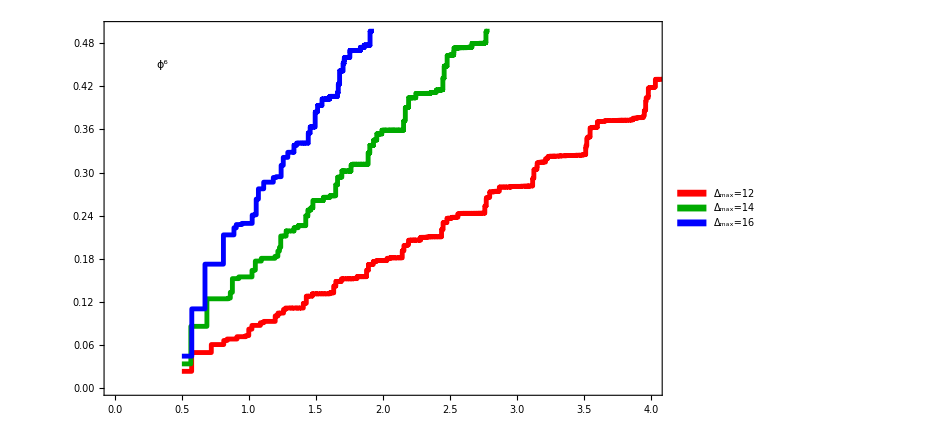

```mathematica
temp=ListLinePlot[{ϕ6SpecD12,ϕ6SpecD14,ϕ6SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^6",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

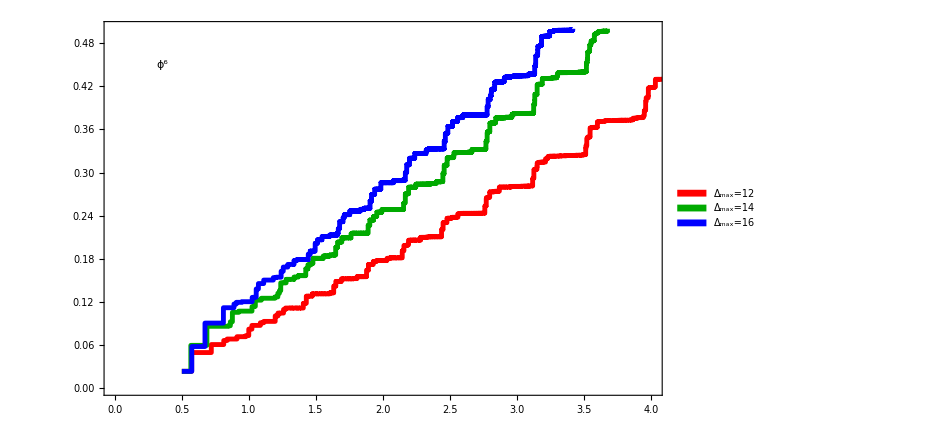

```mathematica
ϕ6SpecD12Rescale=Thread[{ϕ6SpecD12[[All,1]],ϕ6SpecD12[[All,2]]}];
ϕ6SpecD14Rescale=Thread[{ϕ6SpecD14[[All,1]],ϕ6SpecD14[[All,2]]*ϕ6SpecD12[[1,2]]/ϕ6SpecD14[[1,2]]}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*ϕ6SpecD12[[1,2]]/ϕ6SpecD16[[1,2]]}];

temp=ListLinePlot[{ϕ6SpecD12Rescale,ϕ6SpecD14Rescale,ϕ6SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^6",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

```mathematica
ϕ2SpecD16[[1,2]]/ϕ4SpecD16[[1,2]]
ϕ2SpecD16[[1,2]]/ϕ6SpecD16[[1,2]]
```

0.554643

0.151706

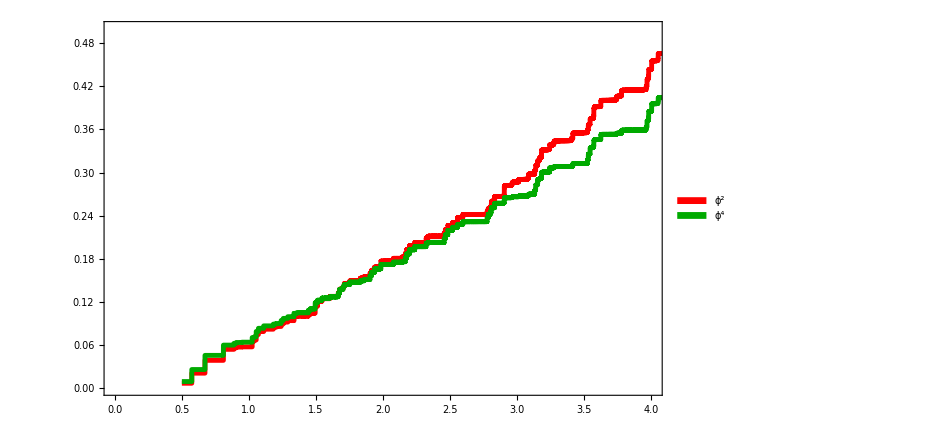

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*.75}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*.16}];

temp=ListLinePlot[{ϕ2SpecD16Rescale,ϕ4SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

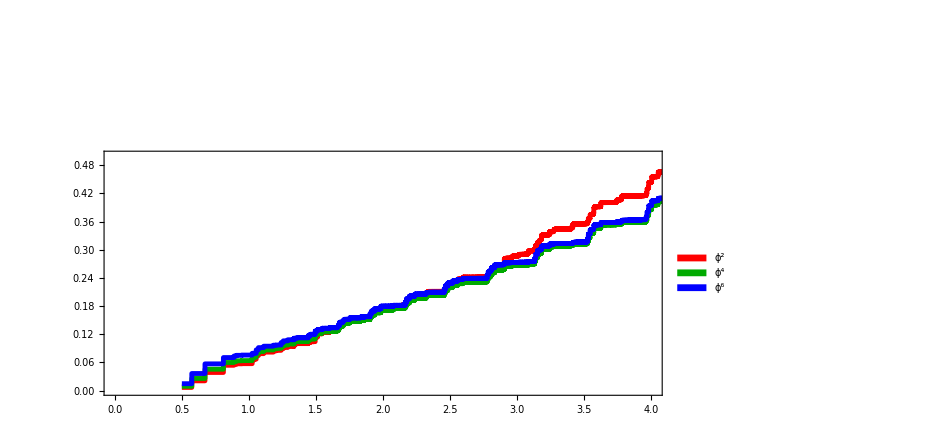

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*.75}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*.33}];

temp=ListLinePlot[{ϕ2SpecD16Rescale,ϕ4SpecD16Rescale,ϕ6SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

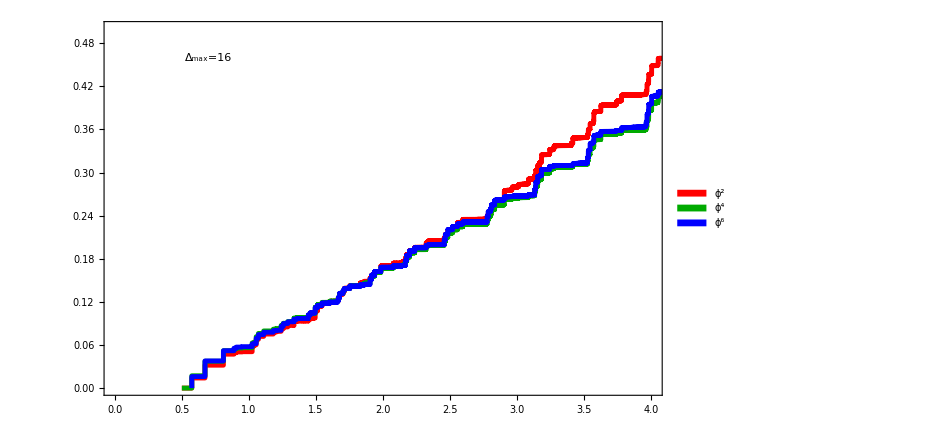

```mathematica
ϕ2SpecD16ShiftRescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]-ϕ2SpecD16[[1,2]]}];
ϕ4SpecD16ShiftRescale=Thread[{ϕ4SpecD16[[All,1]],(ϕ4SpecD16[[All,2]]-ϕ4SpecD16[[1,2]])*.77}];
ϕ6SpecD16ShiftRescale=Thread[{ϕ6SpecD16[[All,1]],(ϕ6SpecD16[[All,2]]-ϕ6SpecD16[[1,2]]-.02)*.35}];

EvenUniversal=ListLinePlot[{ϕ2SpecD16ShiftRescale,ϕ4SpecD16ShiftRescale,ϕ6SpecD16ShiftRescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.7,.46},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.1,.65}]]
```

```mathematica
ϕ2SpecD16[[1,2]]
ϕ4SpecD16[[1,2]]
```

0.00674529

0.0121615

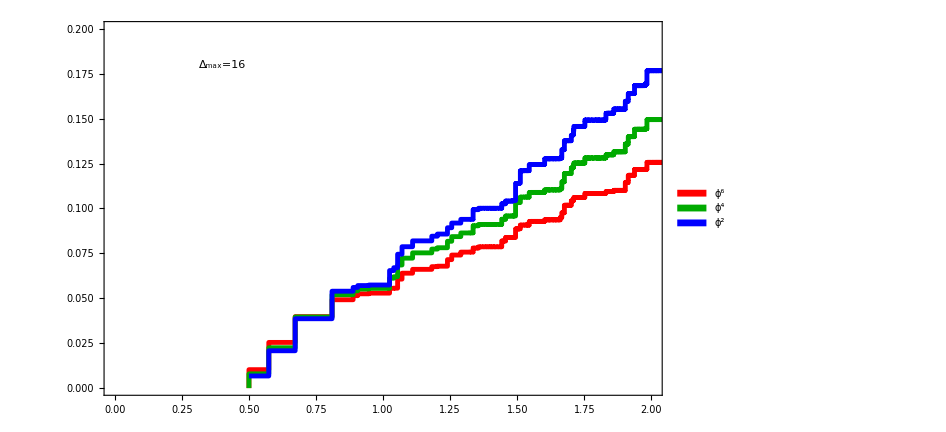

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Prepend[Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ4SpecD16[[i,2]],{i,5}]}],{ϕ4SpecD16[[1,1]],0}];
ϕ6SpecD16Rescale=Prepend[Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ6SpecD16[[i,2]],{i,5}]}],{ϕ6SpecD16[[1,1]],0}];

EvenUniversal=ListLinePlot[{ϕ6SpecD16Rescale,ϕ4SpecD16Rescale,ϕ2SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,2.},{0,.2}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.4,.18},{0,0},FormatType->TraditionalForm,BaseStyle->40]},PlotLegends->Placed[SwatchLegend[{"ϕ^6","ϕ^4","ϕ^2"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.1,.25}]]
```

## Odd Spectral Densities @ μ_(1,odd)=0.5/2

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16F1"];
Get["SpectrumD14F1"];
Get["SpectrumD12F1"];
```

```mathematica
couplingMapD16F1=Interpolation[Select[Thread[{Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD14F1=Interpolation[Select[Thread[{Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]],Select[OddSpectrumD14F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD12F1=Interpolation[Select[Thread[{Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]],Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{16,couplingMapD16F1[.25/4]},{14,couplingMapD14F1[.25/4]},{12,couplingMapD12F1[.25/4]}}
```

{{16,13.1622},{14,13.2032},{12,13.2384}}

```mathematica
13.162215227125788/(4π)
13.203242050899131/(4π)
13.238363922441238/(4π)
```

1.04742

1.05068

1.05348

```mathematica
Δmax=16;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 5.59494

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
(* ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax]; *)

ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
```

241

```mathematica
t1=AbsoluteTime[];

g=13.162215227125788;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕIntegratedSpec=Thread[{√vals,Accumulate[(vecs.ϕOverlaps)^2]}];
ϕ3IntegratedSpec=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ3Overlaps)^2]}];
ϕ5IntegratedSpec=Thread[{√vals,Λ^4*Accumulate[(vecs.ϕ5Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 11.7717

```mathematica
ϕSpecD16=ϕIntegratedSpec;
ϕ3SpecD16=ϕ3IntegratedSpec;
ϕ5SpecD16=ϕ5IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="OddSpectralDensitiesF1GapSquared025";
DeleteFile[filename];
Save[filename,{ϕSpecD12,ϕ3SpecD12,ϕ5SpecD12,ϕSpecD14,ϕ3SpecD14,ϕ5SpecD14,ϕSpecD16,ϕ3SpecD16,ϕ5SpecD16}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["OddSpectralDensitiesIR05F1Gap025"];
```

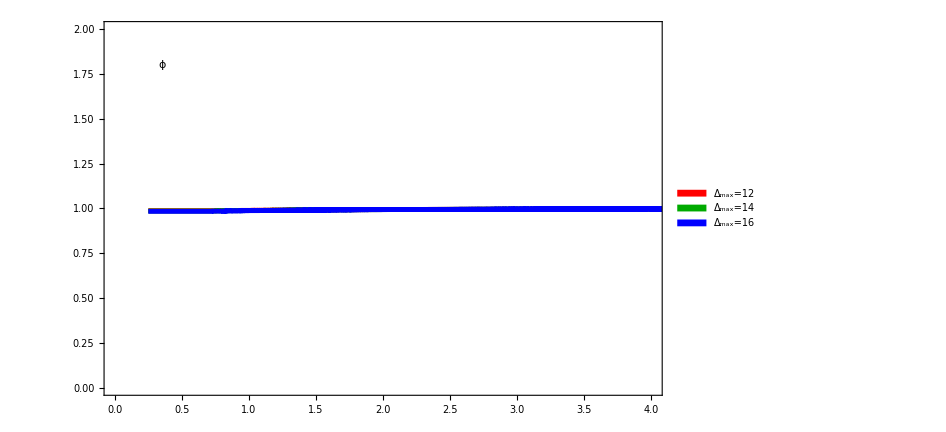

```mathematica
temp=ListLinePlot[{ϕSpecD12,ϕSpecD14,ϕSpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,2}},LabelStyle->Black,Epilog->{Inset[Style["ϕ",FontFamily->"Times"],{.35,1.8},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.7}]]
```

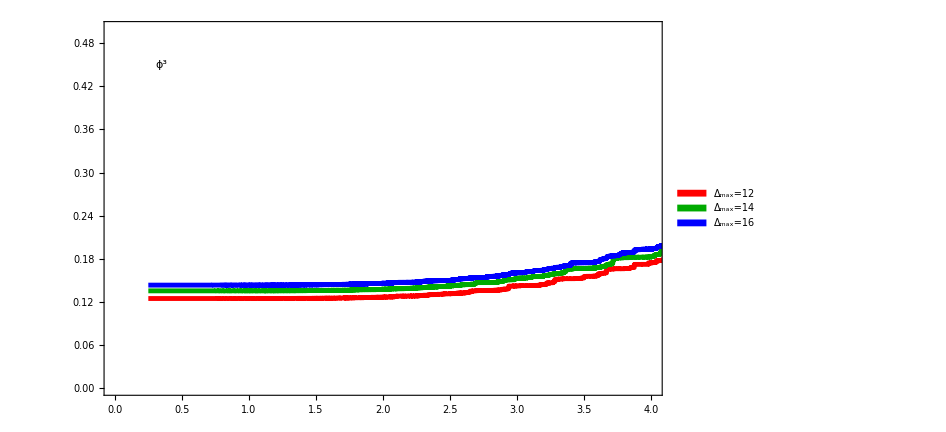

```mathematica
temp=ListLinePlot[{ϕ3SpecD12,ϕ3SpecD14,ϕ3SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^3",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

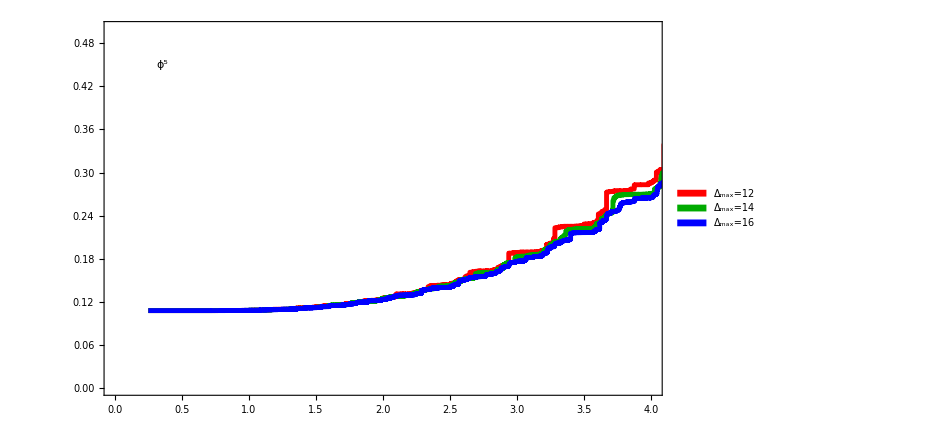

```mathematica
ϕ5SpecD12Rescale=Thread[{ϕ5SpecD12[[All,1]],ϕ5SpecD12[[All,2]]}];
ϕ5SpecD14Rescale=Thread[{ϕ5SpecD14[[All,1]],ϕ5SpecD14[[All,2]]*ϕ5SpecD12[[1,2]]/ϕ5SpecD14[[1,2]]}];
ϕ5SpecD16Rescale=Thread[{ϕ5SpecD16[[All,1]],ϕ5SpecD16[[All,2]]*ϕ5SpecD12[[1,2]]/ϕ5SpecD16[[1,2]]}];

temp=ListLinePlot[{ϕ5SpecD12Rescale,ϕ5SpecD14Rescale,ϕ5SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^5",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

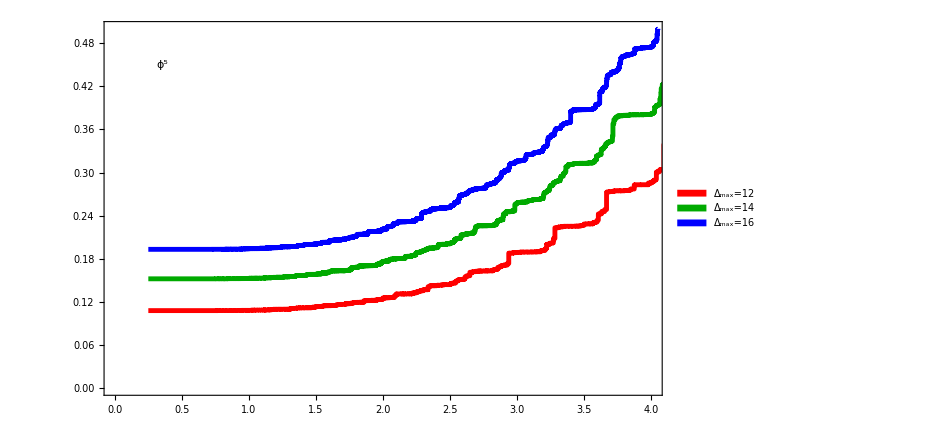

```mathematica
temp=ListLinePlot[{ϕ5SpecD12,ϕ5SpecD14,ϕ5SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^5",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

```mathematica
ϕSpecD16[[1,2]]/ϕ3SpecD16[[1,2]]
ϕSpecD16[[1,2]]/ϕ5SpecD16[[1,2]]
```

6.86571

5.09524

```mathematica
Prepend
```

Prepend

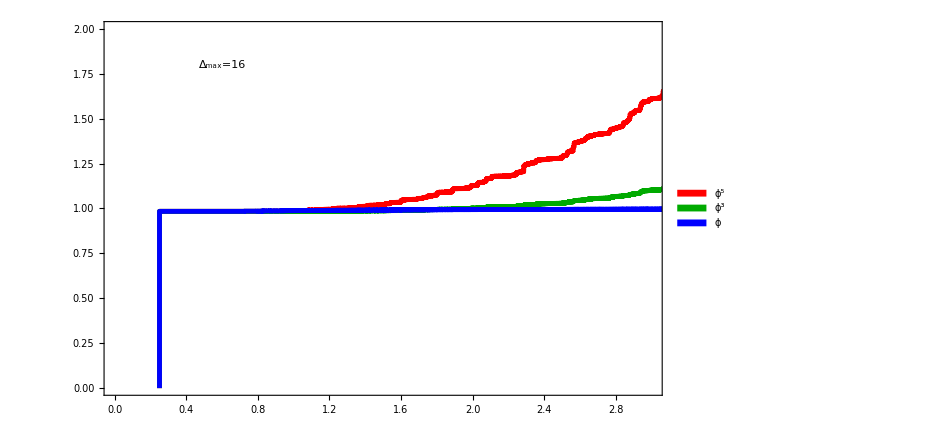

```mathematica
ϕSpecD16Rescale=Prepend[Thread[{ϕSpecD16[[All,1]],ϕSpecD16[[All,2]]}],{ϕSpecD16[[1,1]],0}];
ϕ3SpecD16Rescale=Prepend[Thread[{ϕ3SpecD16[[All,1]],ϕ3SpecD16[[All,2]]*6.865713341282863}],{ϕ3SpecD16[[1,1]],0}];
ϕ5SpecD16Rescale=Prepend[Thread[{ϕ5SpecD16[[All,1]],ϕ5SpecD16[[All,2]]*5.095238669203232}],{ϕ5SpecD16[[1,1]],0}];

OddUniversal=ListLinePlot[{ϕ5SpecD16Rescale,ϕ3SpecD16Rescale,ϕSpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,3.},{0,2.}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.6,1.8},{0,0},FormatType->TraditionalForm,BaseStyle->40]},PlotLegends->Placed[SwatchLegend[{"ϕ^5","ϕ^3","ϕ"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{.85,.25}]]
```

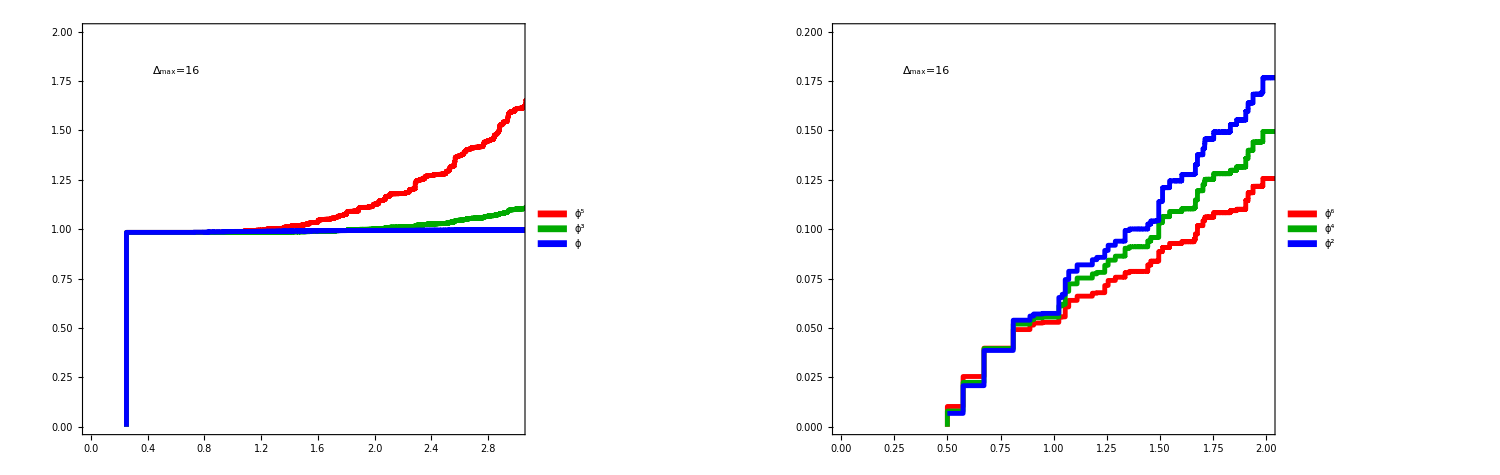
-Graphics-Universality Near Critical Couplingϕ^n Integrated Spectral Densityμ / m

```mathematica
grid=Labeled[GraphicsGrid[{{OddUniversal,EvenUniversal}},ImageSize->1500,Spacings->{0,0}],{Style["Universality Near Critical Coupling",FontFamily->"Times",FontSize->45],Style["ϕ^n Integrated Spectral Density",FontFamily->"Times",FontSize->35],Style["μ / m",FontFamily->"Times",FontSize->35]},{Top,Left,Bottom},RotateLabel->True]
```

```mathematica
temp=ListLinePlot[{ϕ6SpecD12,ϕ6SpecD14,ϕ6SpecD16},Frame->True,FrameStyle->{Black,Thickness[0.002]},FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.5}},LabelStyle->Black];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-ϕ6SpecD12[[1,1]])^(n-1)
FreePlot=Plot[FreeProfile[6,μsq],{μsq,ϕ6SpecD12[[1,1]],100},PlotStyle->{Black}];
Show[temp,FreePlot];
```

## Even Spectral Densities @ μ_(1,even)=1.0

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD14IR05F1"];
Get["SpectrumD12IR05F1"];
```

```mathematica
couplingMapD16=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD14=Interpolation[Select[Thread[{Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD14F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD12=Interpolation[Select[Thread[{Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD12F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{16,couplingMapD16[1.^2]},{14,couplingMapD14[1.^2]},{12,couplingMapD12[1.^2]}}
{{16,couplingMapD16[1.^2]/(4π)},{14,couplingMapD14[1.^2]/(4π)},{12,couplingMapD12[1.^2]/(4π)}}
```

{{16,11.7602},{14,11.8427},{12,11.9235}}

{{16,0.935849},{14,0.942412},{12,0.948844}}

```mathematica
(1/2)/0.9358490194567528
```

0.534274

```mathematica
couplingMapD16[(.25)^2]
```

13.154

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 14.6948

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=11.760225617578184;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 23.4799

```mathematica
ϕ2SpecD16=ϕ2IntegratedSpec;
ϕ4SpecD16=ϕ4IntegratedSpec;
ϕ6SpecD16=ϕ6IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesIR05F1Gap04";
DeleteFile[filename];
Save[filename,{ϕ2SpecD16,ϕ4SpecD16,ϕ6SpecD16}];
```

DeleteFile::fdnfnd: Directory or file EvenSpectralDensitiesIR05F1Gap04 not found.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap05"];
```

```mathematica
temp=ListLinePlot[{ϕ2SpecD12,ϕ2SpecD14,ϕ2SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
temp=ListLinePlot[{ϕ4SpecD12,ϕ4SpecD14,ϕ4SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
temp=ListLinePlot[{ϕ6SpecD12,ϕ6SpecD14,ϕ6SpecD16},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^6",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
ϕ6SpecD12Rescale=Thread[{ϕ6SpecD12[[All,1]],ϕ6SpecD12[[All,2]]}];
ϕ6SpecD14Rescale=Thread[{ϕ6SpecD14[[All,1]],ϕ6SpecD14[[All,2]]*ϕ6SpecD12[[1,2]]/ϕ6SpecD14[[1,2]]}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*ϕ6SpecD12[[1,2]]/ϕ6SpecD16[[1,2]]}];

temp=ListLinePlot[{ϕ6SpecD12Rescale,ϕ6SpecD14Rescale,ϕ6SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^6",FontFamily->"Times"],{.35,.45},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
ϕ2SpecD16[[1,2]]/ϕ4SpecD16[[1,2]]
ϕ2SpecD16[[1,2]]/ϕ6SpecD16[[1,2]]
```

0.554643

0.151706

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*.75}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*.16}];

temp=ListLinePlot[{ϕ2SpecD16Rescale,ϕ4SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*.75}];
ϕ6SpecD16Rescale=Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*.33}];

temp=ListLinePlot[{ϕ2SpecD16Rescale,ϕ4SpecD16Rescale,ϕ6SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]]
```

-Graphics-

```mathematica
ϕ2SpecD16ShiftRescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]-ϕ2SpecD16[[1,2]]}];
ϕ4SpecD16ShiftRescale=Thread[{ϕ4SpecD16[[All,1]],(ϕ4SpecD16[[All,2]]-ϕ4SpecD16[[1,2]])*.77}];
ϕ6SpecD16ShiftRescale=Thread[{ϕ6SpecD16[[All,1]],(ϕ6SpecD16[[All,2]]-ϕ6SpecD16[[1,2]]-.02)*.35}];

EvenUniversal=ListLinePlot[{ϕ2SpecD16ShiftRescale,ϕ4SpecD16ShiftRescale,ϕ6SpecD16ShiftRescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,4},{0,.5}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.7,.46},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.1,.65}]]
```

-Graphics-

```mathematica
ϕ2SpecD16[[1,2]]
ϕ4SpecD16[[1,2]]
```

0.00674529

0.0121615

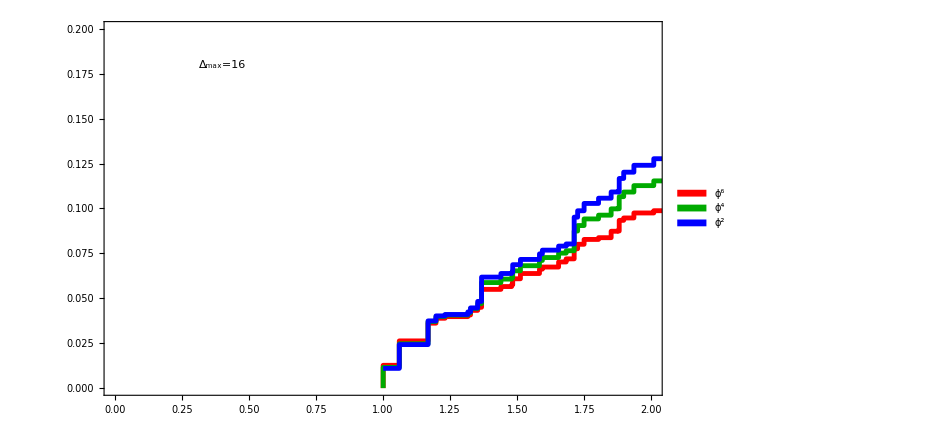

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Prepend[Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ4SpecD16[[i,2]],{i,5}]}],{ϕ4SpecD16[[1,1]],0}];
ϕ6SpecD16Rescale=Prepend[Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ6SpecD16[[i,2]],{i,5}]}],{ϕ6SpecD16[[1,1]],0}];

EvenUniversal=ListLinePlot[{ϕ6SpecD16Rescale,ϕ4SpecD16Rescale,ϕ2SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,2.},{0,.2}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.4,.18},{0,0},FormatType->TraditionalForm,BaseStyle->40]},PlotLegends->Placed[SwatchLegend[{"ϕ^6","ϕ^4","ϕ^2"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.1,.25}]]
```

## Even Spectral Densities @ μ_(1,even)=? (Λ_IR=0.25)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD14IR05F1"];
Get["SpectrumD12IR05F1"];
```

```mathematica
couplingMapD16F1=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD14F1=Interpolation[Select[Thread[{Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD14F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
couplingMapD12F1=Interpolation[Select[Thread[{Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD12F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
{{16,couplingMapD16F1[.25]},{14,couplingMapD14F1[.25]},{12,couplingMapD12F1[.25]}}
```

{{16,12.9123},{14,13.0214},{12,13.123}}

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.25;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 14.5253

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=13.4;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 22.9885

```mathematica
ϕ2SpecD16=ϕ2IntegratedSpec;
ϕ4SpecD16=ϕ4IntegratedSpec;
ϕ6SpecD16=ϕ6IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesF1GapSquared025";
DeleteFile[filename];
Save[filename,{ϕ2SpecD12,ϕ4SpecD12,ϕ6SpecD12,ϕ2SpecD14,ϕ4SpecD14,ϕ6SpecD14,ϕ2SpecD16,ϕ4SpecD16,ϕ6SpecD16}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap05"];
```

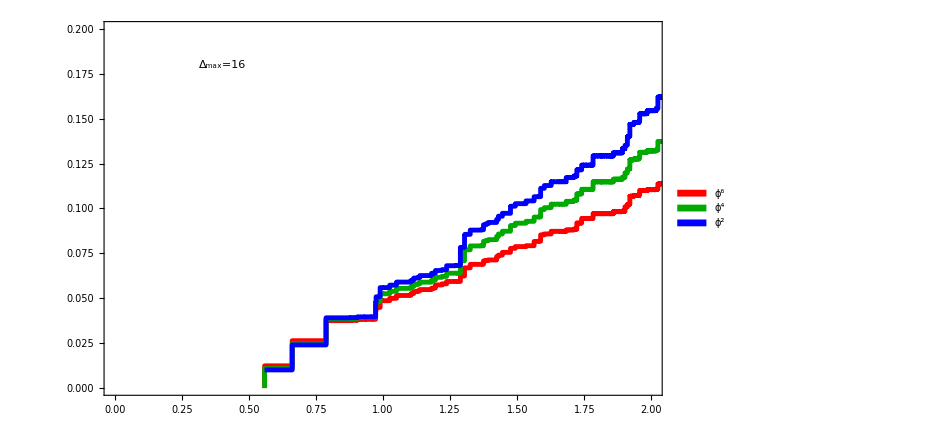

```mathematica
ϕ2SpecD16Rescale=Thread[{ϕ2SpecD16[[All,1]],ϕ2SpecD16[[All,2]]}];
ϕ4SpecD16Rescale=Prepend[Thread[{ϕ4SpecD16[[All,1]],ϕ4SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ4SpecD16[[i,2]],{i,5}]}],{ϕ4SpecD16[[1,1]],0}];
ϕ6SpecD16Rescale=Prepend[Thread[{ϕ6SpecD16[[All,1]],ϕ6SpecD16[[All,2]]*Sum[ϕ2SpecD16[[i,2]],{i,5}]/Sum[ϕ6SpecD16[[i,2]],{i,5}]}],{ϕ6SpecD16[[1,1]],0}];

EvenUniversal=ListLinePlot[{ϕ6SpecD16Rescale,ϕ4SpecD16Rescale,ϕ2SpecD16Rescale},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,2.},{0,.2}},LabelStyle->Black,Epilog->{Inset[Style["Δ_max=16",FontFamily->"Times"],{.4,.18},{0,0},FormatType->TraditionalForm,BaseStyle->40]},PlotLegends->Placed[SwatchLegend[{"ϕ^6","ϕ^4","ϕ^2"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.1,.25}]]
```

## Stress Tensor

### Odd Sector

```mathematica
Δmax=16;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 5.97662

```mathematica
f=1.;
```

```mathematica
(* Scan over couplings *)
glist={13.4}//N;
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N; *)
(* glist={12.5,12.75}//N; *)
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
{g,vals[[1]],vecs[[1]]},{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 13.4366

```mathematica
Expϕ2=Table[2newdata[[iG,3]].mass.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
Expϕ4=Table[glist[[iG]]*Λ*newdata[[iG,3]].int.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
iGc=1;
glist[[iGc]]
```

13.4

```mathematica
δD16=Solve[(1-(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+x)*glist[[iGc]]^2)Expϕ2[[iGc]]+Expϕ4[[iGc]]==0,x][[1,1,2]]
```

-0.00238672

```mathematica
rD14=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+δD14
```

0.00346078

```mathematica
-0.0023867186526020396/(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))])
```

-0.436993

```mathematica
rD16=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+δD16
```

0.00307497

```mathematica
1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]
```

### Even Sector

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16F1"];
```

```mathematica
couplingMapD16F1=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
couplingMapD16F1[2.]
```

9.84647

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 15.2196

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=.75(4π);
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ2ϕ4IntegratedSpec=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 24.0711

```mathematica
.5*(4π)
```

6.28319

```mathematica
6.5/(4π)//N
```

0.517254

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="StressTensorD16F1LambdaBar075";
DeleteFile[filename];
Save[filename,{ϕ2IntegratedSpec,ϕ4IntegratedSpec,ϕ2ϕ4IntegratedSpec}];
```

DeleteFile::fdnfnd: Directory or file StressTensorD16F1LambdaBar075 not found.

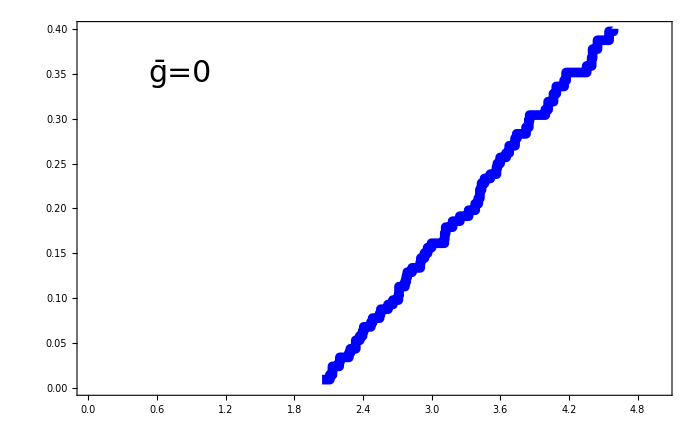

```mathematica
Get["StressTensorD16F1LambdaBar0"];
r=0.003074967338821186;
g=0.;

Tλbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot1=ListLinePlot[{Tλbar0},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],*)Epilog->{Inset[Style["ḡ=0",FontFamily->"Times",FontSize->30],{.8,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

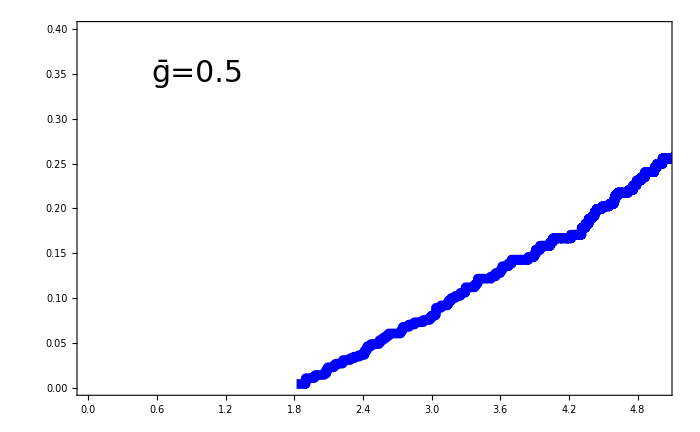

```mathematica
Get["StressTensorD16F1LambdaBar05"];
r=0.003074967338821186;
g=.5(4π);

Tλbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot2=ListLinePlot[{Tλbar05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],*)Epilog->{Inset[Style["ḡ=0.5",FontFamily->"Times",FontSize->30],{.95,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

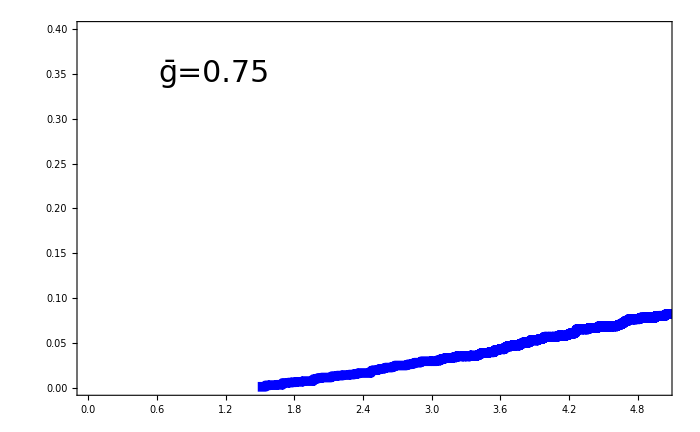

```mathematica
Get["StressTensorD16F1LambdaBar075"];
r=0.003074967338821186;
g=.75(4π);

Tλbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot3=ListLinePlot[{Tλbar075},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.22,.6}],*)Epilog->{Inset[Style["ḡ=0.75",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

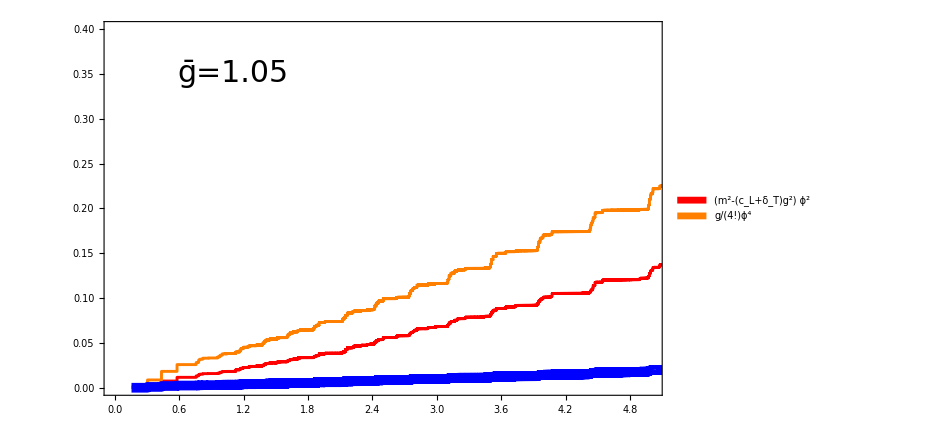

```mathematica
Get["StressTensorD16F1LambdaBar105"];
r=0.003074967338821186;
g=13.2;

Tλbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot4=ListLinePlot[{O2λbar105,O4λbar105,Tλbar105},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.003]},{Orange,Thickness[.003]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],{0.33,.55}],Epilog->{Inset[Style["ḡ=1.05",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

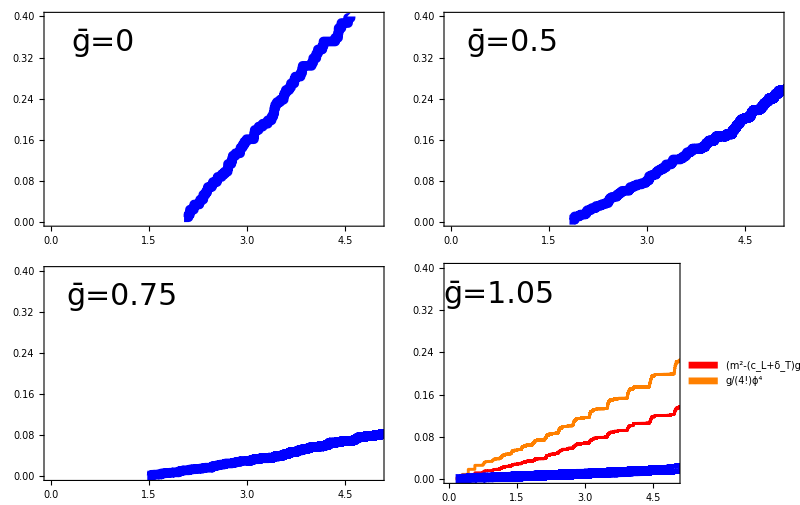
-Graphics-(T^μ)_μ Spectral Density vs. ḡIntegrated Spectral Densityμ / m

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->800,Spacings->{0,0}],{Style["(T^μ)_μ Spectral Density vs. ḡ",FontFamily->"Times",FontSize->25],Style["Integrated Spectral Density",FontFamily->"Times",FontSize->25],Style["μ / m",FontFamily->"Times",FontSize->25]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->{FontFamily->"Times",20}]
```

```mathematica
(* Scan over couplings *)
(* glist={0,1}//N; *)
glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N;
```

```mathematica
(* Scan over couplings *)
(* glist={0,1}//N; *)
glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N;
(* glist={12.5,12.75}//N; *)
nvals=2;
EvenSpectrumList=ConstantArray[{},Length[glist]];
ϕ2IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ4IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ6IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ2ϕ4IntegratedSpecList=ConstantArray[{},Length[glist]];
LowestEvenEvecList=ConstantArray[{},Length[glist]];

t1=AbsoluteTime[];

Monitor[
For[iG=1,iG≤Length[glist],iG++,
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
EvenSpectrumList[[iG]]=vals[[1;;nvals]];
LowestEvenEvecList[[iG]]=vecs[[1]];
ϕ2IntegratedSpecList[[iG]]=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpecList[[iG]]=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpecList[[iG]]=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];
ϕ2ϕ4IntegratedSpecList[[iG]]=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];
]
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 4.04667

```mathematica
rD12
```

0.00285186

```mathematica
r=rD12;
TIntegratedSpecList=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecList[[iG,All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecList[[iG,All,2]]+(g/(4!))^2*ϕ4IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];

test1=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];

test2=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(g/(4!))^2*ϕ4IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];
```

```mathematica
plots=Table[ListLinePlot[{TIntegratedSpecList[[iG]],test1[[iG]],test2[[iG]]},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{-1,1.5}},LabelStyle->Black,Epilog->{Inset[Style["",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"T","ϕ^2","ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]],{iG,Length[glist]}];
```

```mathematica
Clear[iG];
Manipulate[
plots[[iG]]
,{iG,1,Length[glist],1}]
```

Part::partd: Part specification plots⟦16⟧ is longer than depth of object.

```mathematica
glist[[13]]
```

12.

```mathematica
1/(12/4/π)//N
```

1.0472

```mathematica
glist[[12]]
```

11.

## Stress Tensor: Vary Λ_IR

### Odd Sector

```mathematica
Δmax=16;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.25;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 5.36965

```mathematica
f=1.;
```

```mathematica
(* Subscript[Λ, IR]=0.5 & 0.75: *)
(* glist={13.4}//N;  *)
(* Subscript[Λ, IR]=0.25 *)
glist={13.37}//N;

nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
{g,vals[[1]],vecs[[1]]},{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 11.96

```mathematica
Expϕ2IR025=Table[2newdata[[iG,3]].mass.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
Expϕ4IR025=Table[glist[[iG]]*Λ*newdata[[iG,3]].int.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
iGc=1;
glist[[iGc]]
```

13.37

```mathematica
δTIR025=Solve[(1-(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+x)*glist[[iGc]]^2)Expϕ2IR025[[iGc]]+Expϕ4IR025[[iGc]]==0,x][[1,1,2]]
```

-0.0015578

```mathematica
rIR025=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+δTIR025
```

0.00390388

```mathematica
SetDirectory[NotebookDirectory[]];
Get["StressTensorD16F1LambdaBar105VaryIR"];
```

```mathematica
δTIR025
δTIR05
δTIR075
```

-0.0015578

-0.00238672

-0.0029745

```mathematica
rIR025
rIR05
rIR075
```

0.00390388

0.00307497

0.00248719

### Even Sector

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.25;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 15.4128

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=1.05(4π);
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ2ϕ4IntegratedSpec=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 24.1262

```mathematica
ϕ2IntegratedSpecIR025=ϕ2IntegratedSpec;
ϕ4IntegratedSpecIR025=ϕ4IntegratedSpec;
ϕ2ϕ4IntegratedSpecIR025=ϕ2ϕ4IntegratedSpec;
```

```mathematica
r=rIR025;
g=1.05(4π);

TIR025=Thread[{ϕ2IntegratedSpecIR025[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR025[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecIR025[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecIR025[[All,2]]}];

O2IR025=Thread[{ϕ2IntegratedSpecIR025[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR025[[All,2]]}];

O4IR025=Thread[{ϕ2IntegratedSpecIR025[[All,1]],(g/(4!))^2*ϕ4IntegratedSpecIR025[[All,2]]}];
```

```mathematica
r=rIR05;
g=1.05(4π);

TIR05=Thread[{ϕ2IntegratedSpecIR05[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR05[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecIR05[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecIR05[[All,2]]}];

O2IR05=Thread[{ϕ2IntegratedSpecIR05[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR05[[All,2]]}];

O4IR05=Thread[{ϕ2IntegratedSpecIR05[[All,1]],(g/(4!))^2*ϕ4IntegratedSpecIR05[[All,2]]}];
```

```mathematica
r=rIR075;
g=1.05(4π);

TIR075=Thread[{ϕ2IntegratedSpecIR075[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR075[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecIR075[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecIR075[[All,2]]}];

O2IR075=Thread[{ϕ2IntegratedSpecIR075[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecIR075[[All,2]]}];

O4IR075=Thread[{ϕ2IntegratedSpecIR075[[All,1]],(g/(4!))^2*ϕ4IntegratedSpecIR075[[All,2]]}];
```

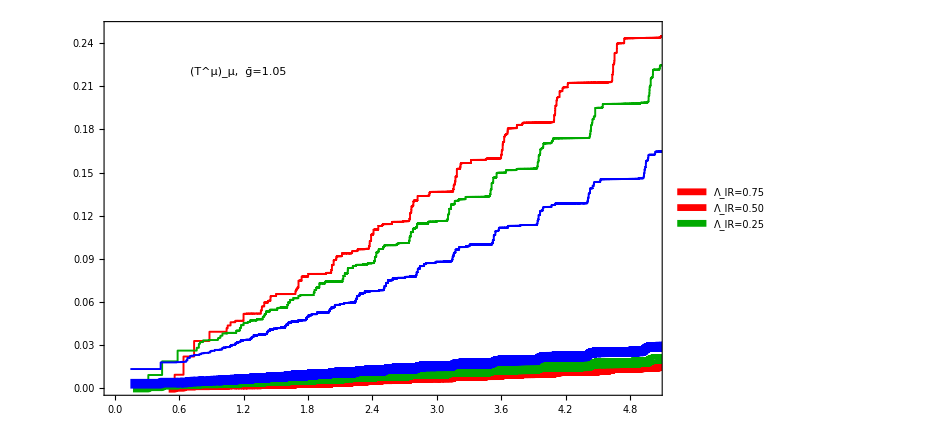

```mathematica
plot4=ListLinePlot[{O4IR075,TIR075,O4IR05,TIR05,O4IR025,TIR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.002]},{Red,Thickness[.01]},{Darker[Green],Thickness[.002]},{Darker[Green],Thickness[.01]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.25}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],Epilog->{Inset[Style["(T^μ)_μ,  ḡ=1.05",FontFamily->"Times"],{1.15,.22},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="StressTensorD16F1LambdaBar105VaryIR";
DeleteFile[filename];
Save[filename,{δTIR05,rIR05,ϕ2IntegratedSpecIR05,ϕ4IntegratedSpecIR05,ϕ2ϕ4IntegratedSpecIR05,TIR05,O2IR05,O4IR05,δTIR075,rIR075,ϕ2IntegratedSpecIR075,ϕ4IntegratedSpecIR075,ϕ2ϕ4IntegratedSpecIR075,TIR075,O2IR075,O4IR075,δTIR025,rIR025,ϕ2IntegratedSpecIR025,ϕ4IntegratedSpecIR025,ϕ2ϕ4IntegratedSpecIR025,TIR025,O2IR025,O4IR025}];
```

```mathematica
rIR05
rIR075
```

0.00251944

0.00224646

## Equation of Motion?

```mathematica
Δmax=16;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 6.60368

```mathematica
x=1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]
```

0.00546169

```mathematica
y=nonlocalCT[[1,1]]
```

0.00488258

```mathematica
y/x
```

0.89397

```mathematica
x-y
```

0.000579101

```mathematica
x-2*y
```

-0.00430348

```mathematica
1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]-2*nonlocalCT[[1,1]]
```

-0.00370782

```mathematica
nonlocalCT[[1,1]]
```

0.00461688

```mathematica
1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]-2*nonlocalCT[[1,1]]
```

-0.00334489

```mathematica
1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]-2*nonlocalCT[[1,1]]
```

-0.0031617

```mathematica
(1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]-nonlocalCT[[1,1]])*2
```

0.00254399

```mathematica
ΛMAX
```

1411.16

### Odd Sector

```mathematica
Δmax=10;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.75;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0239291

```mathematica
f=1.;
```

```mathematica
(* Scan over couplings *)
glist={13.4}//N;
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N; *)
(* glist={12.5,12.75}//N; *)
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
{g,vals[[1]],vecs[[1]]},{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0256607

```mathematica
Expϕ2=Table[2newdata[[iG,3]].mass.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
Expϕ4=Table[glist[[iG]]*Λ*newdata[[iG,3]].int.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
iGc=1;
glist[[iGc]]
```

13.4

```mathematica
δD8IR05=Solve[(1-(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+x)*glist[[iGc]]^2)Expϕ2[[iGc]]+Expϕ4[[iGc]]==0,x][[1,1,2]]
```

-0.00294224

```mathematica
δD8IR075=Solve[(1-(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+x)*glist[[iGc]]^2)Expϕ2[[iGc]]+Expϕ4[[iGc]]==0,x][[1,1,2]]
```

-0.00321523

```mathematica
rIR05=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+-0.0029422420341309865
```

0.00251944

```mathematica
rIR075=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+-0.003215230418131422
```

0.00224646

```mathematica
1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]
```

### Even Sector

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16F1"];
```

```mathematica
couplingMapD16F1=Interpolation[Select[Thread[{Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]],Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]>0&]];
```

```mathematica
couplingMapD16F1[2.]
```

9.84647

```mathematica
Δmax=10;
kmax=65;
sector="even";

m=1.;
ΛIR=0.75;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0206719

```mathematica
f=1.;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

17

```mathematica
t1=AbsoluteTime[];

g=1.05(4π);
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ2ϕ4IntegratedSpec=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0264113

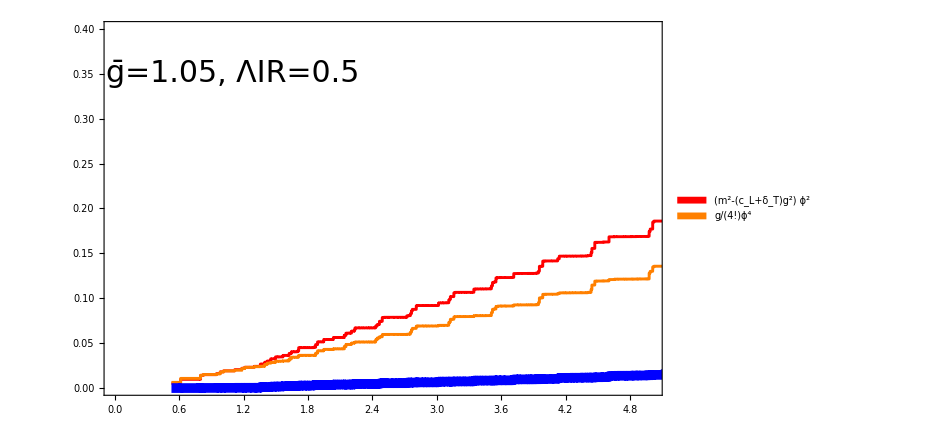

```mathematica
r=rIR05;
g=1.05(4π);

Tλbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot4=ListLinePlot[{O2λbar105,O4λbar105,Tλbar105},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.003]},{Orange,Thickness[.003]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],{0.33,.55}],Epilog->{Inset[Style["ḡ=1.05, ΛIR=0.5",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

```mathematica
rIR05
rIR075
```

0.00251944

0.00224646

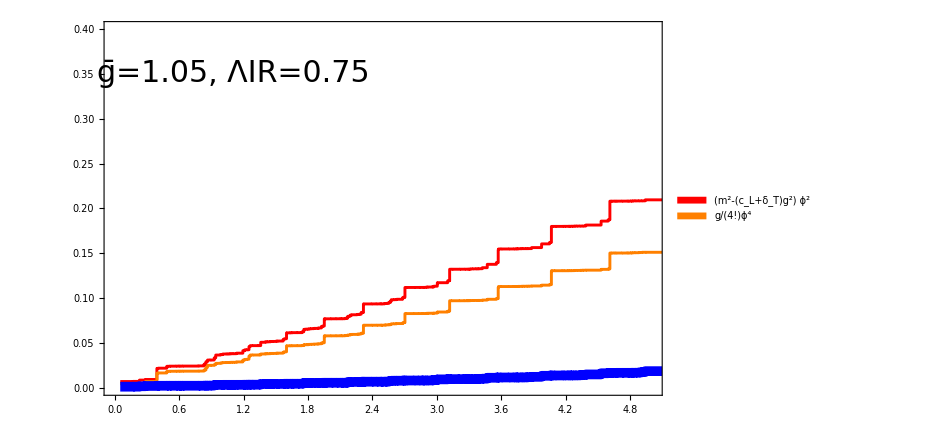

```mathematica
r=rIR075;
g=1.05(4π);

Tλbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot4=ListLinePlot[{O2λbar105,O4λbar105,Tλbar105},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.003]},{Orange,Thickness[.003]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],{0.33,.55}],Epilog->{Inset[Style["ḡ=1.05, ΛIR=0.75",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

```mathematica
.5*(4π)
```

6.28319

```mathematica
6.5/(4π)//N
```

0.517254

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="StressTensorD16F1LambdaBar075";
DeleteFile[filename];
Save[filename,{ϕ2IntegratedSpec,ϕ4IntegratedSpec,ϕ2ϕ4IntegratedSpec}];
```

DeleteFile::fdnfnd: Directory or file StressTensorD16F1LambdaBar075 not found.

```mathematica
Get["StressTensorD16F1LambdaBar0"];
r=0.003074967338821186;
g=0.;

Tλbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar0=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot1=ListLinePlot[{Tλbar0},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],*)Epilog->{Inset[Style["ḡ=0",FontFamily->"Times",FontSize->30],{.8,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

-Graphics-

```mathematica
Get["StressTensorD16F1LambdaBar05"];
r=0.003074967338821186;
g=.5(4π);

Tλbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar05=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot2=ListLinePlot[{Tλbar05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],*)Epilog->{Inset[Style["ḡ=0.5",FontFamily->"Times",FontSize->30],{.95,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

-Graphics-

```mathematica
Get["StressTensorD16F1LambdaBar075"];
r=0.003074967338821186;
g=.75(4π);

Tλbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar075=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot3=ListLinePlot[{Tλbar075},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,(*PlotLegends->Placed[SwatchLegend[{"(T^μ)_μ"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.22,.6}],*)Epilog->{Inset[Style["ḡ=0.75",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

-Graphics-

```mathematica
Get["StressTensorD16F1LambdaBar105"];
r=0.003074967338821186;
g=13.2;

Tλbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpec[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

O2λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(1-r*g^2)^2 ϕ2IntegratedSpec[[All,2]]}];

O4λbar105=Thread[{ϕ2IntegratedSpec[[All,1]],(g/(4!))^2*ϕ4IntegratedSpec[[All,2]]}];

plot4=ListLinePlot[{O2λbar105,O4λbar105,Tλbar105},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Red,Thickness[.003]},{Orange,Thickness[.003]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.4}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],{0.33,.55}],Epilog->{Inset[Style["ḡ=1.05",FontFamily->"Times",FontSize->30],{1.1,.35},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

-Graphics-

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->800,Spacings->{0,0}],{Style["(T^μ)_μ Spectral Density vs. ḡ",FontFamily->"Times",FontSize->25],Style["Integrated Spectral Density",FontFamily->"Times",FontSize->25],Style["μ / m",FontFamily->"Times",FontSize->25]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->{FontFamily->"Times",20}]
```

-Graphics-(T^μ)_μ Spectral Density vs. ḡIntegrated Spectral Densityμ / m

```mathematica
(* Scan over couplings *)
(* glist={0,1}//N; *)
glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N;
```

```mathematica
(* Scan over couplings *)
(* glist={0,1}//N; *)
glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N;
(* glist={12.5,12.75}//N; *)
nvals=2;
EvenSpectrumList=ConstantArray[{},Length[glist]];
ϕ2IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ4IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ6IntegratedSpecList=ConstantArray[{},Length[glist]];
ϕ2ϕ4IntegratedSpecList=ConstantArray[{},Length[glist]];
LowestEvenEvecList=ConstantArray[{},Length[glist]];

t1=AbsoluteTime[];

Monitor[
For[iG=1,iG≤Length[glist],iG++,
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
EvenSpectrumList[[iG]]=vals[[1;;nvals]];
LowestEvenEvecList[[iG]]=vecs[[1]];
ϕ2IntegratedSpecList[[iG]]=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpecList[[iG]]=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpecList[[iG]]=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];
ϕ2ϕ4IntegratedSpecList[[iG]]=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];
]
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 4.04667

```mathematica
rD12
```

0.00285186

```mathematica
r=rD12;
TIntegratedSpecList=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecList[[iG,All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecList[[iG,All,2]]+(g/(4!))^2*ϕ4IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];

test1=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(1-r*g^2)^2 ϕ2IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];

test2=Table[
g=glist[[iG]];
Thread[{ϕ2IntegratedSpecList[[iG,All,1]],(g/(4!))^2*ϕ4IntegratedSpecList[[iG,All,2]]}]
,{iG,1,Length[glist]}];
```

```mathematica
plots=Table[ListLinePlot[{TIntegratedSpecList[[iG]],test1[[iG]],test2[[iG]]},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{-1,1.5}},LabelStyle->Black,Epilog->{Inset[Style["",FontFamily->"Times"],{.75,1.35},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"T","ϕ^2","ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]],{iG,Length[glist]}];
```

```mathematica
Clear[iG];
Manipulate[
plots[[iG]]
,{iG,1,Length[glist],1}]
```

Part::partd: Part specification plots⟦16⟧ is longer than depth of object.

```mathematica
glist[[13]]
```

12.

```mathematica
1/(12/4/π)//N
```

1.0472

```mathematica
glist[[12]]
```

11.

## Eigenvalue Ratios: vary c_L

### Generate data

```mathematica
Δmax=10;
kmax=64;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.0146546

```mathematica
f=0.5;
```

```mathematica
(* Scan over couplings *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N; *)
glist={0,2,4,6,8,10,12,14,16,17,18,18.25,18.5,18.75,19,19.1,19.18}//N;
(* glist={0,1,2,3,4,5,6,7,8,8.5,8.75,9,9.2,9.4,9.5}//N; *)
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
vals=eigenvals[full];
{g,kmax,vals[[1;;nvals]]}//Flatten,{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.317686

```mathematica
newdata
```

{{0.,64,4.24936,4.53061},{2.,64,4.21192,4.48986},{4.,64,4.08487,4.35917},{6.,64,3.86866,4.13893},{8.,64,3.56264,3.82943},{10.,64,3.16497,3.431},{12.,64,2.6721,2.94424},{14.,64,2.07794,2.36994},{16.,64,1.37212,1.70778},{17.,64,0.971599,1.28092},{18.,64,0.532577,0.745385},{18.25,64,0.415364,0.602902},{18.5,64,0.29429,0.455352},{18.75,64,0.16825,0.300058},{19.,64,0.0337174,0.129189},{19.1,64,-0.0273425,0.0509432},{19.18,64,-0.0998205,-0.0223389}}

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD10IR05VaryF"];
```

```mathematica
EvenSpectrumD10F05
```

{{0.,60,4.24936,4.53061},{0.,61,4.24936,4.53061},{0.,62,4.24936,4.53061},{0.,63,4.24936,4.53061},{0.,65,4.24936,4.53061},{2.,60,4.21192,4.48986},{2.,61,4.21192,4.48986},{2.,62,4.21192,4.48986},{2.,63,4.21192,4.48986},{2.,65,4.21192,4.48986},{4.,60,4.08487,4.35917},{4.,61,4.08487,4.35917},{4.,62,4.08487,4.35917},{4.,63,4.08487,4.35917},{4.,65,4.08487,4.35917},{6.,60,3.86866,4.13893},{6.,61,3.86866,4.13893},{6.,62,3.86866,4.13893},{6.,63,3.86866,4.13893},{6.,65,3.86866,4.13893},{8.,60,3.56265,3.82942},{8.,61,3.56265,3.82942},{8.,62,3.56264,3.82942},{8.,63,3.56264,3.82943},{8.,65,3.56264,3.82943},{10.,60,3.16499,3.43098},{10.,61,3.16498,3.43099},{10.,62,3.16498,3.43099},{10.,63,3.16497,3.43099},{10.,65,3.16496,3.431},{12.,60,2.67217,2.94419},{12.,61,2.67215,2.94421},{12.,62,2.67213,2.94422},{12.,63,2.67212,2.94423},{12.,65,2.67209,2.94425},{14.,60,2.07811,2.36985},{14.,61,2.07806,2.36987},{14.,62,2.07802,2.3699},{14.,63,2.07798,2.36992},{14.,65,2.07791,2.36995},{16.,60,1.37247,1.70761},{16.,61,1.37236,1.70766},{16.,62,1.37227,1.70771},{16.,63,1.37219,1.70774},{16.,65,1.37205,1.70781},{17.,60,0.972073,1.28104},{17.,61,0.971935,1.28101},{17.,62,0.971812,1.28098},{17.,63,0.9717,1.28095},{17.,65,0.971509,1.2809},{18.,60,0.533202,0.745572},{18.,61,0.533021,0.745518},{18.,62,0.532857,0.745469},{18.,63,0.532709,0.745425},{18.,65,0.532457,0.745348},{18.25,60,0.416033,0.603112},{18.25,61,0.415839,0.603051},{18.25,62,0.415664,0.602996},{18.25,63,0.415506,0.602946},{18.25,65,0.415237,0.602861},{18.5,60,0.295004,0.45559},{18.5,61,0.294796,0.455521},{18.5,62,0.294609,0.455458},{18.5,63,0.294441,0.455402},{18.5,65,0.294153,0.455306},{18.75,60,0.169012,0.300333},{18.75,61,0.168791,0.300253},{18.75,62,0.168591,0.300181},{18.75,63,0.168412,0.300116},{18.75,65,0.168104,0.300005},{19.,60,0.0345342,0.129502},{19.,61,0.0342968,0.129411},{19.,62,0.034083,0.129329},{19.,63,0.0338906,0.129256},{19.,65,0.0335617,0.12913},{19.1,60,-0.0265052,0.0512484},{19.1,61,-0.0267485,0.0511598},{19.1,62,-0.0269677,0.0510799},{19.1,63,-0.027165,0.051008},{19.1,65,-0.0275021,0.050885},{19.18,60,-0.0991262,-0.0220317},{19.18,61,-0.0993279,-0.0221211},{19.18,62,-0.0995096,-0.0222015},{19.18,63,-0.0996733,-0.0222739},{19.18,65,-0.099953,-0.0223974}}

```mathematica
EvenSpectrumD10F05=Join[EvenSpectrumD10F05,newdata]//Sort
```

{{0.,60,4.24936,4.53061},{0.,61,4.24936,4.53061},{0.,62,4.24936,4.53061},{0.,63,4.24936,4.53061},{0.,64,4.24936,4.53061},{0.,65,4.24936,4.53061},{2.,60,4.21192,4.48986},{2.,61,4.21192,4.48986},{2.,62,4.21192,4.48986},{2.,63,4.21192,4.48986},{2.,64,4.21192,4.48986},{2.,65,4.21192,4.48986},{4.,60,4.08487,4.35917},{4.,61,4.08487,4.35917},{4.,62,4.08487,4.35917},{4.,63,4.08487,4.35917},{4.,64,4.08487,4.35917},{4.,65,4.08487,4.35917},{6.,60,3.86866,4.13893},{6.,61,3.86866,4.13893},{6.,62,3.86866,4.13893},{6.,63,3.86866,4.13893},{6.,64,3.86866,4.13893},{6.,65,3.86866,4.13893},{8.,60,3.56265,3.82942},{8.,61,3.56265,3.82942},{8.,62,3.56264,3.82942},{8.,63,3.56264,3.82943},{8.,64,3.56264,3.82943},{8.,65,3.56264,3.82943},{10.,60,3.16499,3.43098},{10.,61,3.16498,3.43099},{10.,62,3.16498,3.43099},{10.,63,3.16497,3.43099},{10.,64,3.16497,3.431},{10.,65,3.16496,3.431},{12.,60,2.67217,2.94419},{12.,61,2.67215,2.94421},{12.,62,2.67213,2.94422},{12.,63,2.67212,2.94423},{12.,64,2.6721,2.94424},{12.,65,2.67209,2.94425},{14.,60,2.07811,2.36985},{14.,61,2.07806,2.36987},{14.,62,2.07802,2.3699},{14.,63,2.07798,2.36992},{14.,64,2.07794,2.36994},{14.,65,2.07791,2.36995},{16.,60,1.37247,1.70761},{16.,61,1.37236,1.70766},{16.,62,1.37227,1.70771},{16.,63,1.37219,1.70774},{16.,64,1.37212,1.70778},{16.,65,1.37205,1.70781},{17.,60,0.972073,1.28104},{17.,61,0.971935,1.28101},{17.,62,0.971812,1.28098},{17.,63,0.9717,1.28095},{17.,64,0.971599,1.28092},{17.,65,0.971509,1.2809},{18.,60,0.533202,0.745572},{18.,61,0.533021,0.745518},{18.,62,0.532857,0.745469},{18.,63,0.532709,0.745425},{18.,64,0.532577,0.745385},{18.,65,0.532457,0.745348},{18.25,60,0.416033,0.603112},{18.25,61,0.415839,0.603051},{18.25,62,0.415664,0.602996},{18.25,63,0.415506,0.602946},{18.25,64,0.415364,0.602902},{18.25,65,0.415237,0.602861},{18.5,60,0.295004,0.45559},{18.5,61,0.294796,0.455521},{18.5,62,0.294609,0.455458},{18.5,63,0.294441,0.455402},{18.5,64,0.29429,0.455352},{18.5,65,0.294153,0.455306},{18.75,60,0.169012,0.300333},{18.75,61,0.168791,0.300253},{18.75,62,0.168591,0.300181},{18.75,63,0.168412,0.300116},{18.75,64,0.16825,0.300058},{18.75,65,0.168104,0.300005},{19.,60,0.0345342,0.129502},{19.,61,0.0342968,0.129411},{19.,62,0.034083,0.129329},{19.,63,0.0338906,0.129256},{19.,64,0.0337174,0.129189},{19.,65,0.0335617,0.12913},{19.1,60,-0.0265052,0.0512484},{19.1,61,-0.0267485,0.0511598},{19.1,62,-0.0269677,0.0510799},{19.1,63,-0.027165,0.051008},{19.1,64,-0.0273425,0.0509432},{19.1,65,-0.0275021,0.050885},{19.18,60,-0.0991262,-0.0220317},{19.18,61,-0.0993279,-0.0221211},{19.18,62,-0.0995096,-0.0222015},{19.18,63,-0.0996733,-0.0222739},{19.18,64,-0.0998205,-0.0223389},{19.18,65,-0.099953,-0.0223974}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD10IR05VaryF";
DeleteFile[filename];
Save[filename,{OddSpectrumD10F2,EvenSpectrumD10F2,OddSpectrumD10F1,EvenSpectrumD10F1,OddSpectrumD10F05,EvenSpectrumD10F05}];
```

### Extrapolate k_max

```mathematica
ΛIR=0.5;
ratioWidth=8/10;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD10IR05VaryF"];
```

```mathematica
spectrum=OddSpectrumD10F05;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,2.,4.,6.,8.,10.,12.,14.,16.,17.,18.,18.25,18.5,18.75,19.,19.1,19.18}

```mathematica
iN=1;
Extrap1pD10F05=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,1.},{2.,0.989461},{4.,0.959114},{6.,0.910383},{8.,0.844205},{10.,0.7611},{12.,0.661163},{14.,0.543894},{16.,0.40767},{17.,0.331199},{18.,0.247415},{18.25,0.224945},{18.5,0.201633},{18.75,0.17721},{19.,0.150971},{19.1,0.139307},{19.18,0.0149208}}

```mathematica
iN=2;
Extrap3pD10F05=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,9.84032},{2.,9.77039},{4.,9.48418},{6.,8.98351},{8.,8.26924},{10.,7.34154},{12.,6.1999},{14.,4.8426},{16.,3.26465},{17.,2.38861},{18.,1.4476},{18.25,1.20049},{18.5,0.936233},{18.75,0.635961},{19.,0.325954},{19.1,0.189905},{19.18,0.0562019}}

```mathematica
spectrum=EvenSpectrumD10F05;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,2.,4.,6.,8.,10.,12.,14.,16.,17.,18.,18.25,18.5,18.75,19.,19.1,19.18}

```mathematica
iN=1;
Extrap2pD10F05=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,4.24936},{2.,4.21192},{4.,4.08487},{6.,3.86867},{8.,3.56264},{10.,3.16493},{12.,2.67197},{14.,2.07763},{16.,1.37149},{17.,0.970755},{18.,0.531461},{18.25,0.414172},{18.5,0.293016},{18.75,0.166891},{19.,0.0322617},{19.1,-0.0288348},{19.18,-0.101058}}

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD10IR05VaryF"];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD10IR05VaryF";
DeleteFile[filename];
Save[filename,{OddSpectrumD10F2,EvenSpectrumD10F2,Extrap1pD10F2,Extrap2pD10F2,Extrap3pD10F2,OddSpectrumD10F1,EvenSpectrumD10F1,Extrap1pD10F1,Extrap2pD10F1,Extrap3pD10F1,OddSpectrumD10F05,EvenSpectrumD10F05,Extrap1pD10F05,Extrap2pD10F05,Extrap3pD10F05}];
```

### Plot

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD10IR05VaryF"];
Get["SpectrumD16IR05VaryF"];
Get["SpectrumD16IR05F1"];
```

Dmax=16:

```mathematica
ratio2D16F1=Select[Thread[{(√Drop[Extrap1pD16F1[[All,2]],-1])/((Drop[Extrap1pD16F1[[All,1]],-1]/(4π))+10^-10),Extrap2pD16F1[[All,2]]/(4*Drop[Extrap1pD16F1[[All,2]],-1])}],#[[1]]∈Reals&];
ratio2D16F2=Select[Thread[{(√Extrap1pD16F2[[All,2]])/((Extrap1pD16F2[[All,1]]/(4π))+10^-10),Extrap2pD16F2[[All,2]]/(4*Extrap1pD16F2[[All,2]])}],#[[1]]∈Reals&];
ratio2D16F05=Select[Thread[{(√Extrap1pD16F05[[All,2]])/((Extrap1pD16F05[[All,1]]/(4π))+10^-10),Extrap2pD16F05[[All,2]]/(4*Extrap1pD16F05[[All,2]])}],#[[1]]∈Reals&];

ratio3D16F1=Select[Thread[{(√Extrap1pD16F1[[All,2]])/((Extrap1pD16F1[[All,1]]/(4π))+10^-10),Extrap3pD16F1[[All,2]]/(9*Extrap1pD16F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D16F2=Select[Thread[{(√Extrap1pD16F2[[All,2]])/((Extrap1pD16F2[[All,1]]/(4π))+10^-10),Extrap3pD16F2[[All,2]]/(9*Extrap1pD16F2[[All,2]])}],#[[1]]∈Reals&];
ratio3D16F05=Select[Thread[{(√Extrap1pD16F05[[All,2]])/((Extrap1pD16F05[[All,1]]/(4π))+10^-10),Extrap3pD16F05[[All,2]]/(9*Extrap1pD16F05[[All,2]])}],#[[1]]∈Reals&];
```

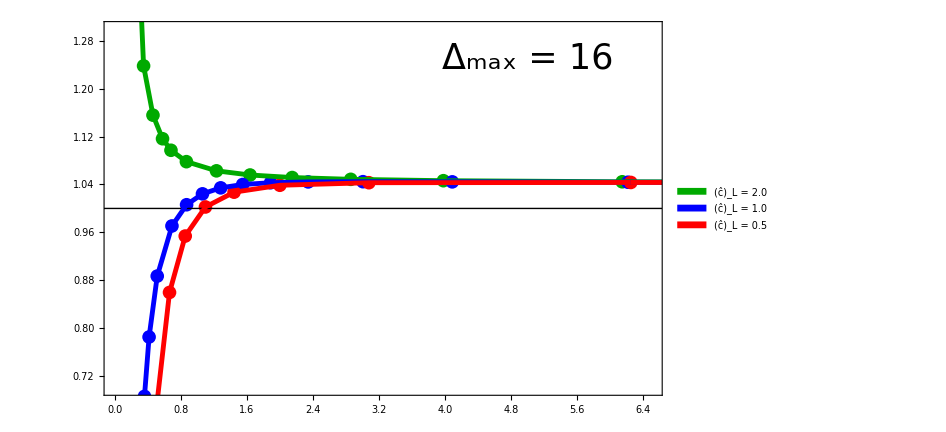

```mathematica
exper=ListPlot[{ratio2D16F2,ratio2D16F1,ratio2D16F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]},{Red,PointSize[0.014]}},FrameLabel->{None,Style[(*"μ_(2 - part.)^2  /  (4 μ_(1 - part.)^2)"*)"",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->35],{5.,1.25}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"(ĉ)_L = 2.0","(ĉ)_L = 1.0","(ĉ)_L = 0.5"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio2D16F2,ratio2D16F1,ratio2D16F05},PlotStyle->{{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]},{Red,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig2=Show[exper,line,fit]
```

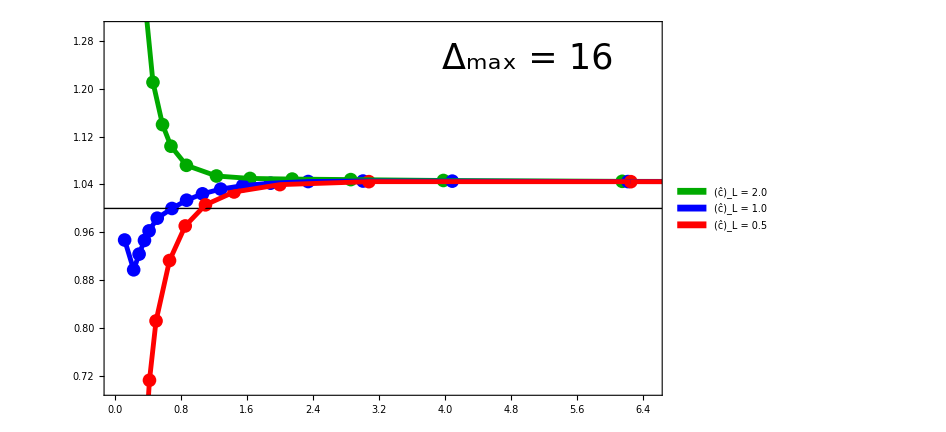

```mathematica
exper=ListPlot[{ratio3D16F2,ratio3D16F1,ratio3D16F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]},{Red,PointSize[0.014]}},FrameLabel->{None,Style[(*"μ_(3 - part.)^2  /  (9 μ_(1 - part.)^2)"*)"",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->35],{5.,1.25}]},PlotLegends->Placed[SwatchLegend[{"(ĉ)_L = 2.0","(ĉ)_L = 1.0","(ĉ)_L = 0.5"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio3D16F2,ratio3D16F1,ratio3D16F05},PlotStyle->{{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]},{Red,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig4=Show[exper,line,fit]
```

Dmax=10:

```mathematica
ratio2D10F1=Select[Thread[{(√Extrap1pD10F1[[All,2]])/((Extrap1pD10F1[[All,1]]/(4π))+10^-10),Extrap2pD10F1[[All,2]]/(4*Extrap1pD10F1[[All,2]])}],#[[1]]∈Reals&];
ratio2D10F2=Select[Thread[{(√Extrap1pD10F2[[All,2]])/((Extrap1pD10F2[[All,1]]/(4π))+10^-10),Extrap2pD10F2[[All,2]]/(4*Extrap1pD10F2[[All,2]])}],#[[1]]∈Reals&];
ratio2D10F05=Select[Thread[{(√Extrap1pD10F05[[All,2]])/((Extrap1pD10F05[[All,1]]/(4π))+10^-10),Extrap2pD10F05[[All,2]]/(4*Extrap1pD10F05[[All,2]])}],#[[1]]∈Reals&];

ratio3D10F1=Select[Thread[{(√Extrap1pD10F1[[All,2]])/((Extrap1pD10F1[[All,1]]/(4π))+10^-10),Extrap3pD10F1[[All,2]]/(9*Extrap1pD10F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D10F2=Select[Thread[{(√Extrap1pD10F2[[All,2]])/((Extrap1pD10F2[[All,1]]/(4π))+10^-10),Extrap3pD10F2[[All,2]]/(9*Extrap1pD10F2[[All,2]])}],#[[1]]∈Reals&];
ratio3D10F05=Select[Thread[{(√Extrap1pD10F05[[All,2]])/((Extrap1pD10F05[[All,1]]/(4π))+10^-10),Extrap3pD10F05[[All,2]]/(9*Extrap1pD10F05[[All,2]])}],#[[1]]∈Reals&];
```

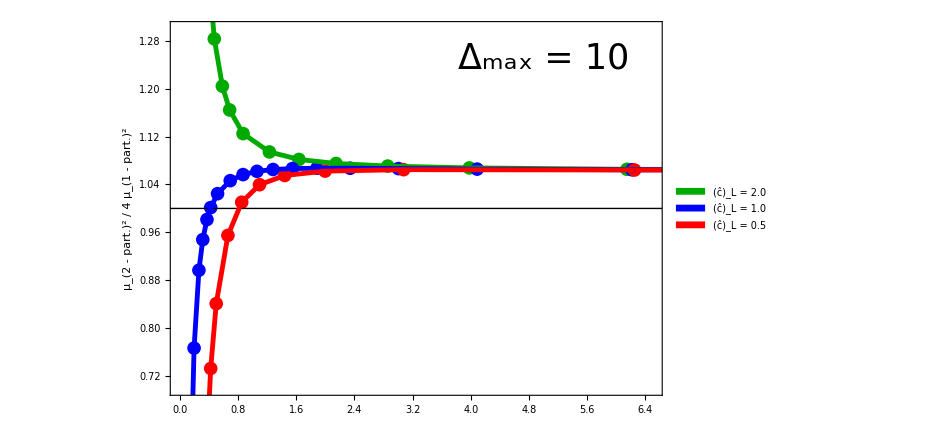

```mathematica
exper=ListPlot[{ratio2D10F2,ratio2D10F1,ratio2D10F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]},{Red,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2 - part.)^2  /  4 μ_(1 - part.)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}},Epilog->{Inset[Style["Δ_max = 10",FontFamily->"Times",FontSize->35],{5.,1.25}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"(ĉ)_L = 2.0","(ĉ)_L = 1.0","(ĉ)_L = 0.5"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio2D10F2,ratio2D10F1,ratio2D10F05},PlotStyle->{{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]},{Red,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

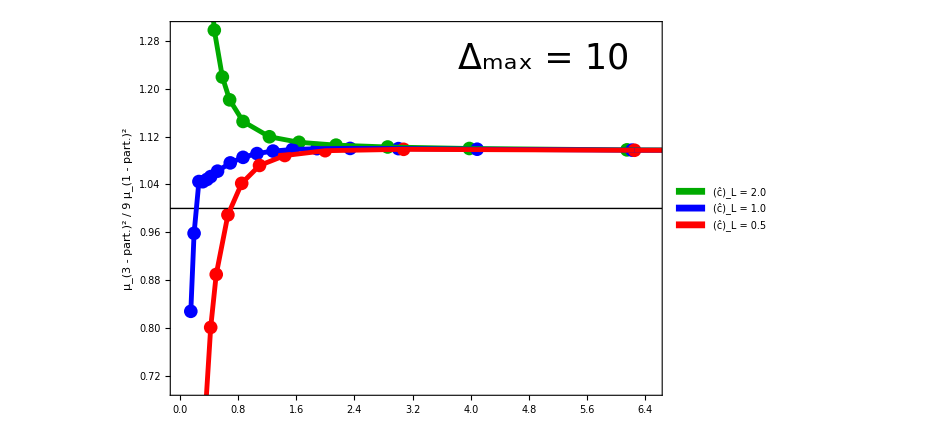

```mathematica
exper=ListPlot[{ratio3D10F2,ratio3D10F1,ratio3D10F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]},{Red,PointSize[0.014]}},FrameLabel->{None,Style["μ_(3 - part.)^2  /  9 μ_(1 - part.)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 10",FontFamily->"Times",FontSize->35],{5.,1.25}]},PlotLegends->Placed[SwatchLegend[{"(ĉ)_L = 2.0","(ĉ)_L = 1.0","(ĉ)_L = 0.5"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio3D10F2,ratio3D10F1,ratio3D10F05},PlotStyle->{{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]},{Red,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

Grid:

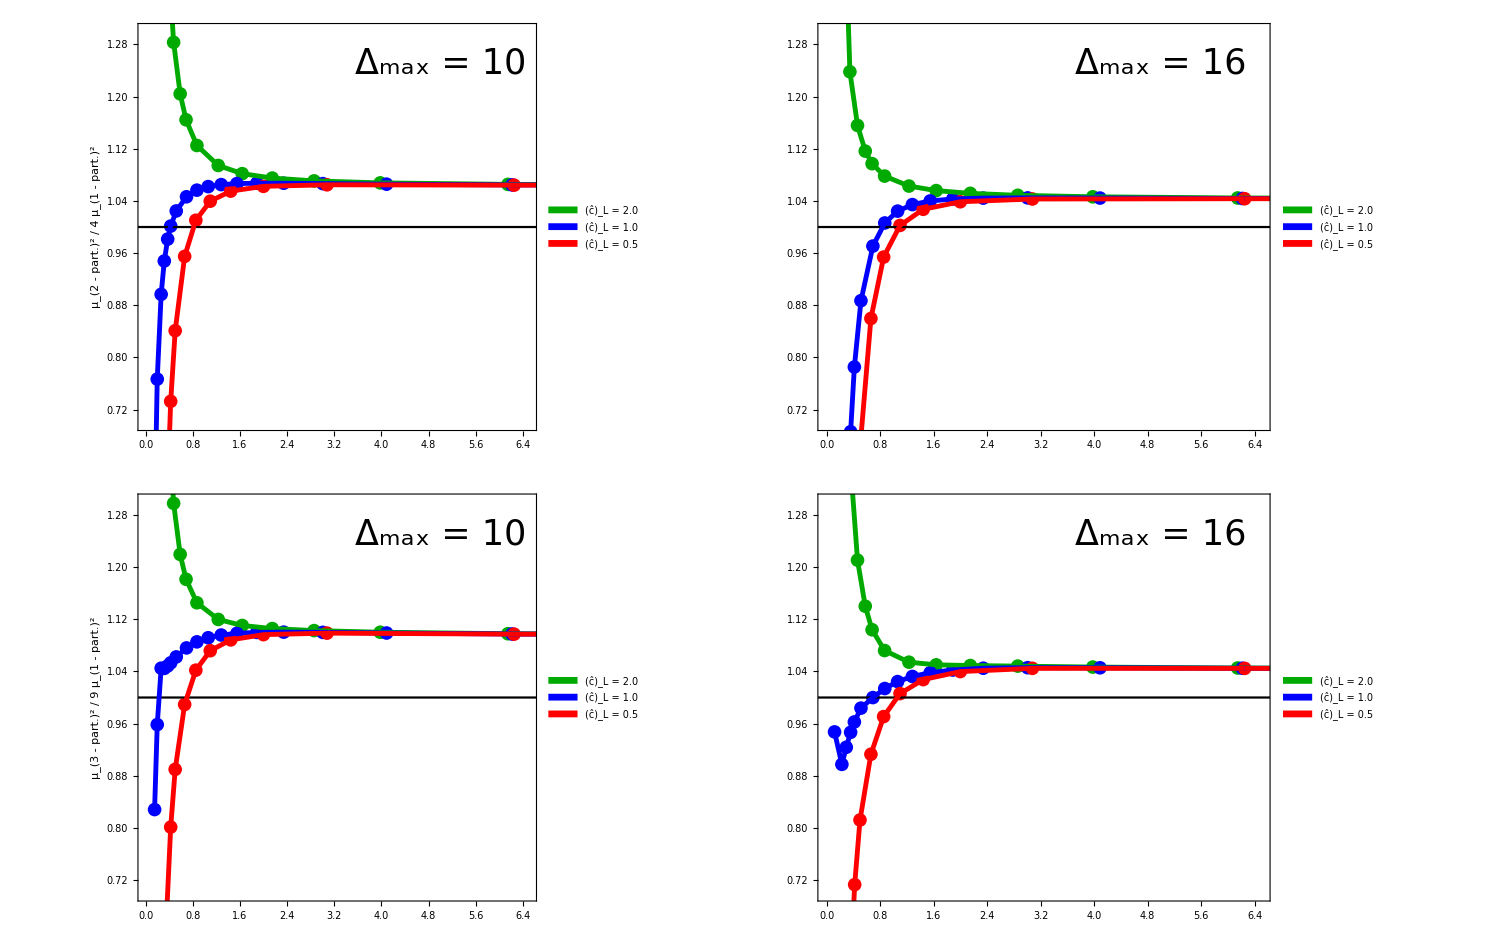
-Graphics-Eigenvalue Ratios: Varying (ĉ)_Lm_gap / (g/(4  π))

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2},{fig3,fig4}},ImageSize->1500,Spacings->{-30,0}],{Style["Eigenvalue Ratios: Varying (ĉ)_L",FontFamily->"Times",FontSize->45],Style["m_gap / (g/(4  π))",FontFamily->"Times",FontSize->40]},{Top,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{-.5,0}]
```

#### Dmax=8

```mathematica
ratio2D8F1=Select[Thread[{(√(Select[OddSpectrumD8F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD8F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD8F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];
ratio2D8F2=Select[Thread[{(√(Select[OddSpectrumD8F2,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F2,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD8F2,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD8F2,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];
ratio2D8F05=Select[Thread[{(√(Select[OddSpectrumD8F05,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F05,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD8F05,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD8F05,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];

ratio3D8F1=Select[Thread[{(√(Select[OddSpectrumD8F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD8F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD8F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];
ratio3D8F2=Select[Thread[{(√(Select[OddSpectrumD8F2,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F2,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD8F2,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD8F2,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];
ratio3D8F05=Select[Thread[{(√(Select[OddSpectrumD8F05,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD8F05,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD8F05,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD8F05,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&];
```

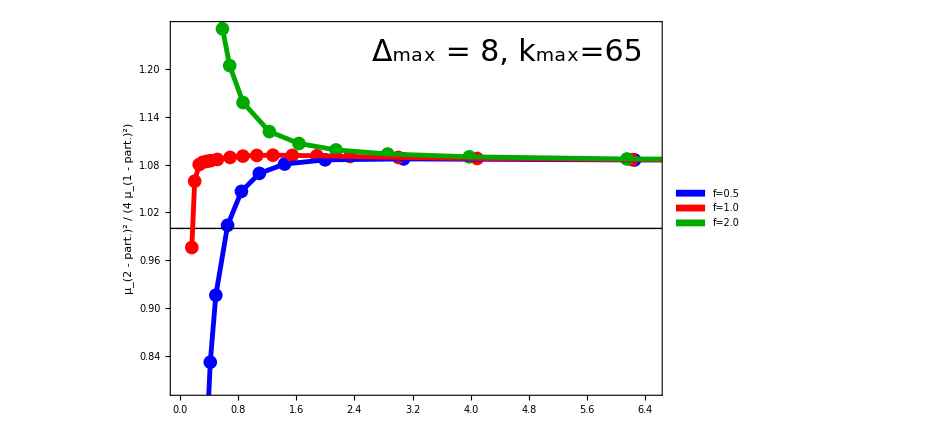

```mathematica
exper=ListPlot[{ratio2D8F05,ratio2D8F1,ratio2D8F2},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["μ_(2 - part.)^2  /  (4 μ_(1 - part.)^2)",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.8,1.25}},Epilog->{Inset[Style["Δ_max = 8, k_max=65",FontFamily->"Times",FontSize->30],{4.5,1.22}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"f=0.5","f=1.0","f=2.0"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio2D8F05,ratio2D8F1,ratio2D8F2},PlotStyle->{{Blue,Thickness[.005]},{Red,Thickness[.005]},{Darker[Green],Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1d8=Show[exper,line,fit]
```

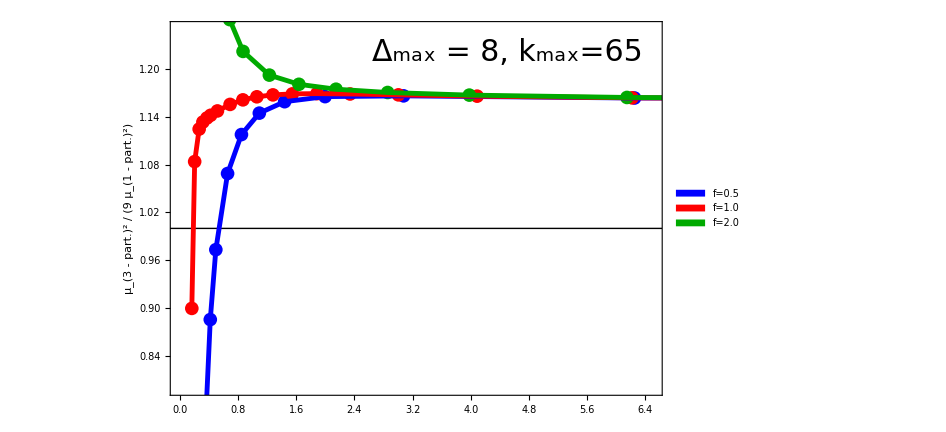

```mathematica
exper=ListPlot[{ratio3D8F05,ratio3D8F1,ratio3D8F2},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["μ_(3 - part.)^2  /  (9 μ_(1 - part.)^2)",FontFamily->"Times",FontSize->35,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.8,1.25}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 8, k_max=65",FontFamily->"Times",FontSize->30],{4.5,1.22}]},PlotLegends->Placed[SwatchLegend[{"f=0.5","f=1.0","f=2.0"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio3D8F05,ratio3D8F1,ratio3D8F2},PlotStyle->{{Blue,Thickness[.005]},{Red,Thickness[.005]},{Darker[Green],Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3d8=Show[exper,line,fit]
```

## Eigenvalue Ratios: vary Δ_max & Λ_IR

### Generate data

```mathematica
Δmax=14;
kmax=60;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 1.16277

```mathematica
f=1.;
```

```mathematica
(* Scan over couplings *)
glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N;
(* glist={0,2,4,6,8,10,12,14,16,17,18,18.25,18.5,18.75,19,19.1,19.18}//N; *)
(* glist={0,1,2,3,4,5,6,7,8,8.5,8.75,9,9.2,9.4,9.5}//N; *)
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
vals=eigenvals[full];
{g,kmax,vals[[1;;nvals]]}//Flatten,{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 20.2966

```mathematica
newdata
```

{{0.,60,4.18397,4.46522},{1.,60,4.16447,4.44454},{2.,60,4.10068,4.37951},{3.,60,3.99267,4.27023},{4.,60,3.84034,4.11674},{5.,60,3.64336,3.9191},{6.,60,3.40119,3.67736},{7.,60,3.11297,3.39158},{8.,60,2.77746,3.06173},{9.,60,2.39286,2.68266},{10.,60,1.95652,2.20163},{11.,60,1.46431,1.65679},{12.,60,0.908508,1.04445},{12.5,60,0.601362,0.707111},{12.75,60,0.438148,0.527862},{13.,60,0.266177,0.338701},{13.2,60,0.11935,0.177091},{13.4,60,-0.0428237,0.000581846},{13.5,60,-0.136482,-0.0986194}}

```mathematica
Get["SpectrumD14IR05F1"];
```

```mathematica
EvenSpectrumD14F1
```

{{0.,61,4.18397,4.46522},{0.,62,4.18397,4.46522},{0.,63,4.18397,4.46522},{0.,64,4.18397,4.46522},{0.,65,4.18397,4.46522},{1.,61,4.16447,4.44454},{1.,62,4.16447,4.44454},{1.,63,4.16447,4.44454},{1.,64,4.16447,4.44454},{1.,65,4.16447,4.44454},{2.,61,4.10068,4.37951},{2.,62,4.10068,4.37951},{2.,63,4.10068,4.37951},{2.,64,4.10068,4.37951},{2.,65,4.10068,4.37951},{3.,61,3.99267,4.27023},{3.,62,3.99267,4.27023},{3.,63,3.99267,4.27023},{3.,64,3.99267,4.27023},{3.,65,3.99267,4.27023},{4.,61,3.84034,4.11674},{4.,62,3.84034,4.11674},{4.,63,3.84034,4.11674},{4.,64,3.84034,4.11674},{4.,65,3.84034,4.11674},{5.,61,3.64336,3.9191},{5.,62,3.64336,3.9191},{5.,63,3.64336,3.9191},{5.,64,3.64336,3.9191},{5.,65,3.64336,3.9191},{6.,61,3.40118,3.67736},{6.,62,3.40118,3.67736},{6.,63,3.40118,3.67736},{6.,64,3.40117,3.67737},{6.,65,3.40117,3.67737},{7.,61,3.11296,3.39158},{7.,62,3.11295,3.39159},{7.,63,3.11294,3.39159},{7.,64,3.11293,3.39159},{7.,65,3.11293,3.3916},{8.,61,2.77744,3.06174},{8.,62,2.77742,3.06175},{8.,63,2.77741,3.06176},{8.,64,2.77739,3.06177},{8.,65,2.77738,3.06177},{9.,61,2.39283,2.68266},{9.,62,2.39279,2.68266},{9.,63,2.39276,2.68266},{9.,64,2.39273,2.68266},{9.,65,2.39271,2.68266},{10.,61,1.95646,2.20159},{10.,62,1.9564,2.20156},{10.,63,1.95635,2.20153},{10.,64,1.9563,2.2015},{10.,65,1.95626,2.20147},{11.,61,1.46421,1.65673},{11.,62,1.46411,1.65667},{11.,63,1.46403,1.65662},{11.,64,1.46396,1.65657},{11.,65,1.46389,1.65653},{12.,61,0.908352,1.04434},{12.,62,0.908213,1.04425},{12.,63,0.908087,1.04416},{12.,64,0.907974,1.04409},{12.,65,0.907873,1.04402},{12.5,61,0.601173,0.706978},{12.5,62,0.601003,0.706857},{12.5,63,0.60085,0.706749},{12.5,64,0.600712,0.706652},{12.5,65,0.600588,0.706564},{12.75,61,0.437939,0.527709},{12.75,62,0.437751,0.527572},{12.75,63,0.437583,0.527448},{12.75,64,0.437431,0.527337},{12.75,65,0.437295,0.527238},{13.,61,0.265948,0.338525},{13.,62,0.265741,0.338367},{13.,63,0.265556,0.338225},{13.,64,0.265389,0.338098},{13.,65,0.265239,0.337983},{13.2,61,0.119103,0.176895},{13.2,62,0.118881,0.176718},{13.2,63,0.118681,0.176559},{13.2,64,0.118501,0.176417},{13.2,65,0.11834,0.176289},{13.4,61,-0.0430868,0.000366406},{13.4,62,-0.0433233,0.000172695},{13.4,63,-0.0435358,-1.39929×10^-6},{13.4,64,-0.0437266,-0.0001578},{13.4,65,-0.0438978,-0.000298251},{13.5,61,-0.136747,-0.0988388},{13.5,62,-0.136986,-0.0990361},{13.5,63,-0.1372,-0.0992135},{13.5,64,-0.137393,-0.0993727},{13.5,65,-0.137566,-0.0995158}}

```mathematica
EvenSpectrumD14F1=Join[EvenSpectrumD14F1,newdata]//Sort
```

{{0.,60,4.18397,4.46522},{0.,61,4.18397,4.46522},{0.,62,4.18397,4.46522},{0.,63,4.18397,4.46522},{0.,64,4.18397,4.46522},{0.,65,4.18397,4.46522},{1.,60,4.16447,4.44454},{1.,61,4.16447,4.44454},{1.,62,4.16447,4.44454},{1.,63,4.16447,4.44454},{1.,64,4.16447,4.44454},{1.,65,4.16447,4.44454},{2.,60,4.10068,4.37951},{2.,61,4.10068,4.37951},{2.,62,4.10068,4.37951},{2.,63,4.10068,4.37951},{2.,64,4.10068,4.37951},{2.,65,4.10068,4.37951},{3.,60,3.99267,4.27023},{3.,61,3.99267,4.27023},{3.,62,3.99267,4.27023},{3.,63,3.99267,4.27023},{3.,64,3.99267,4.27023},{3.,65,3.99267,4.27023},{4.,60,3.84034,4.11674},{4.,61,3.84034,4.11674},{4.,62,3.84034,4.11674},{4.,63,3.84034,4.11674},{4.,64,3.84034,4.11674},{4.,65,3.84034,4.11674},{5.,60,3.64336,3.9191},{5.,61,3.64336,3.9191},{5.,62,3.64336,3.9191},{5.,63,3.64336,3.9191},{5.,64,3.64336,3.9191},{5.,65,3.64336,3.9191},{6.,60,3.40119,3.67736},{6.,61,3.40118,3.67736},{6.,62,3.40118,3.67736},{6.,63,3.40118,3.67736},{6.,64,3.40117,3.67737},{6.,65,3.40117,3.67737},{7.,60,3.11297,3.39158},{7.,61,3.11296,3.39158},{7.,62,3.11295,3.39159},{7.,63,3.11294,3.39159},{7.,64,3.11293,3.39159},{7.,65,3.11293,3.3916},{8.,60,2.77746,3.06173},{8.,61,2.77744,3.06174},{8.,62,2.77742,3.06175},{8.,63,2.77741,3.06176},{8.,64,2.77739,3.06177},{8.,65,2.77738,3.06177},{9.,60,2.39286,2.68266},{9.,61,2.39283,2.68266},{9.,62,2.39279,2.68266},{9.,63,2.39276,2.68266},{9.,64,2.39273,2.68266},{9.,65,2.39271,2.68266},{10.,60,1.95652,2.20163},{10.,61,1.95646,2.20159},{10.,62,1.9564,2.20156},{10.,63,1.95635,2.20153},{10.,64,1.9563,2.2015},{10.,65,1.95626,2.20147},{11.,60,1.46431,1.65679},{11.,61,1.46421,1.65673},{11.,62,1.46411,1.65667},{11.,63,1.46403,1.65662},{11.,64,1.46396,1.65657},{11.,65,1.46389,1.65653},{12.,60,0.908508,1.04445},{12.,61,0.908352,1.04434},{12.,62,0.908213,1.04425},{12.,63,0.908087,1.04416},{12.,64,0.907974,1.04409},{12.,65,0.907873,1.04402},{12.5,60,0.601362,0.707111},{12.5,61,0.601173,0.706978},{12.5,62,0.601003,0.706857},{12.5,63,0.60085,0.706749},{12.5,64,0.600712,0.706652},{12.5,65,0.600588,0.706564},{12.75,60,0.438148,0.527862},{12.75,61,0.437939,0.527709},{12.75,62,0.437751,0.527572},{12.75,63,0.437583,0.527448},{12.75,64,0.437431,0.527337},{12.75,65,0.437295,0.527238},{13.,60,0.266177,0.338701},{13.,61,0.265948,0.338525},{13.,62,0.265741,0.338367},{13.,63,0.265556,0.338225},{13.,64,0.265389,0.338098},{13.,65,0.265239,0.337983},{13.2,60,0.11935,0.177091},{13.2,61,0.119103,0.176895},{13.2,62,0.118881,0.176718},{13.2,63,0.118681,0.176559},{13.2,64,0.118501,0.176417},{13.2,65,0.11834,0.176289},{13.4,60,-0.0428237,0.000581846},{13.4,61,-0.0430868,0.000366406},{13.4,62,-0.0433233,0.000172695},{13.4,63,-0.0435358,-1.39929×10^-6},{13.4,64,-0.0437266,-0.0001578},{13.4,65,-0.0438978,-0.000298251},{13.5,60,-0.136482,-0.0986194},{13.5,61,-0.136747,-0.0988388},{13.5,62,-0.136986,-0.0990361},{13.5,63,-0.1372,-0.0992135},{13.5,64,-0.137393,-0.0993727},{13.5,65,-0.137566,-0.0995158}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD14IR05F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD14F1,EvenSpectrumD14F1}];
```

### Extrapolate k_max

```mathematica
ΛIR=0.25;
ratioWidth=8/10;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR025F1"];
```

```mathematica
spectrum=OddSpectrumD16IR025F1;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,12.5,12.75,13.,13.2,13.4,13.5}

```mathematica
iN=1;
Extrap1pD16IR025F1=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,1.},{1.,0.994594},{2.,0.978564},{3.,0.952131},{4.,0.915441},{5.,0.868575},{6.,0.811543},{7.,0.744282},{8.,0.666627},{9.,0.57827},{10.,0.478659},{11.,0.366765},{12.,0.240317},{12.5,0.169911},{12.75,0.132094},{13.,0.0916539},{13.2,0.0560568},{13.4,0.0031134},{13.5,-0.162871}}

```mathematica
iN=2;
Extrap3pD16IR025F1=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,9.28863},{1.,9.24364},{2.,9.09707},{3.,8.84913},{4.,8.49989},{5.,8.04941},{6.,7.4976},{7.,6.84431},{8.,6.08918},{9.,5.22879},{10.,4.26474},{11.,3.1987},{12.,2.00668},{12.5,1.35459},{12.75,1.01016},{13.,0.649512},{13.2,0.345138},{13.4,0.0276979},{13.5,-0.0752729}}

```mathematica
spectrum=EvenSpectrumD16IR025F1;
glist=spectrum[[All,1]]//DeleteDuplicates
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,12.5,12.75,13.,13.2,13.4,13.5}

```mathematica
iN=1;
Extrap2pD16IR025F1=Table[
temp1=Select[spectrum,#[[1]]==glist[[iG]]&];
temp2=Thread[{1/(ΛIR*√((1-ratioWidth^#)/(ratioWidth^(#-1)(1-ratioWidth)))&/@temp1[[All,2]]),temp1[[All,2+iN]]}];
lim=FindFit[temp2,a*x+b,{a,b},x][[2,2]];
{glist[[iG]],lim},{iG,Length[glist]}]
```

{{0.,4.07544},{1.,4.05451},{2.,3.98944},{3.,3.88008},{4.,3.72593},{5.,3.52607},{6.,3.27904},{7.,2.98295},{8.,2.63566},{9.,2.23484},{10.,1.7776},{11.,1.25948},{12.,0.671677},{12.5,0.345167},{12.75,0.170886},{13.,-0.0137243},{13.2,-0.172784},{13.4,-0.352072},{13.5,-0.460261}}

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR025F1"];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="SpectrumD16IR025F1";
DeleteFile[filename];
Save[filename,{OddSpectrumD16IR025F1,EvenSpectrumD16IR025F1,Extrap1pD16IR025F1,Extrap3pD16IR025F1,Extrap2pD16IR025F1}];
```

### Plot

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD16IR075F1"];
Get["SpectrumD16IR025F1"];
Get["SpectrumD14IR05F1"];
Get["SpectrumD12IR05F1"];
```

```mathematica
ratio2D16F1=Select[Thread[{(√Drop[Extrap1pD16F1[[All,2]],-1])/((Drop[Extrap1pD16F1[[All,1]],-1]/(4π))+10^-10),Extrap2pD16F1[[All,2]]/(4*Drop[Extrap1pD16F1[[All,2]],-1])}],#[[1]]∈Reals&];
ratio2D16IR025F1=Select[Thread[{(√Extrap1pD16IR025F1[[All,2]])/((Extrap1pD16IR025F1[[All,1]]/(4π))+10^-10),Extrap2pD16IR025F1[[All,2]]/(4*Extrap1pD16IR025F1[[All,2]])}],#[[1]]∈Reals&];
ratio2D16IR075F1=Select[Thread[{(√Extrap1pD16IR075F1[[All,2]])/((Extrap1pD16IR075F1[[All,1]]/(4π))+10^-10),Extrap2pD16IR075F1[[All,2]]/(4*Extrap1pD16IR075F1[[All,2]])}],#[[1]]∈Reals&];
ratio2D14F1=Select[Thread[{(√Extrap1pD14F1[[All,2]])/((Extrap1pD14F1[[All,1]]/(4π))+10^-10),Extrap2pD14F1[[All,2]]/(4*Extrap1pD14F1[[All,2]])}],#[[1]]∈Reals&];
ratio2D12F1=Select[Thread[{(√Extrap1pD12F1[[All,2]])/((Extrap1pD12F1[[All,1]]/(4π))+10^-10),Extrap2pD12F1[[All,2]]/(4*Extrap1pD12F1[[All,2]])}],#[[1]]∈Reals&];


ratio3D16F1=Select[Thread[{(√Extrap1pD16F1[[All,2]])/((Extrap1pD16F1[[All,1]]/(4π))+10^-10),Extrap3pD16F1[[All,2]]/(9*Extrap1pD16F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D16IR025F1=Select[Thread[{(√Extrap1pD16IR025F1[[All,2]])/((Extrap1pD16IR025F1[[All,1]]/(4π))+10^-10),Extrap3pD16IR025F1[[All,2]]/(9*Extrap1pD16IR025F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D16IR075F1=Select[Thread[{(√Extrap1pD16IR075F1[[All,2]])/((Extrap1pD16IR075F1[[All,1]]/(4π))+10^-10),Extrap3pD16IR075F1[[All,2]]/(9*Extrap1pD16IR075F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D14F1=Select[Thread[{(√Extrap1pD14F1[[All,2]])/((Extrap1pD14F1[[All,1]]/(4π))+10^-10),Extrap3pD14F1[[All,2]]/(9*Extrap1pD14F1[[All,2]])}],#[[1]]∈Reals&];
ratio3D12F1=Select[Thread[{(√Extrap1pD12F1[[All,2]])/((Extrap1pD12F1[[All,1]]/(4π))+10^-10),Extrap3pD12F1[[All,2]]/(9*Extrap1pD12F1[[All,2]])}],#[[1]]∈Reals&];
```

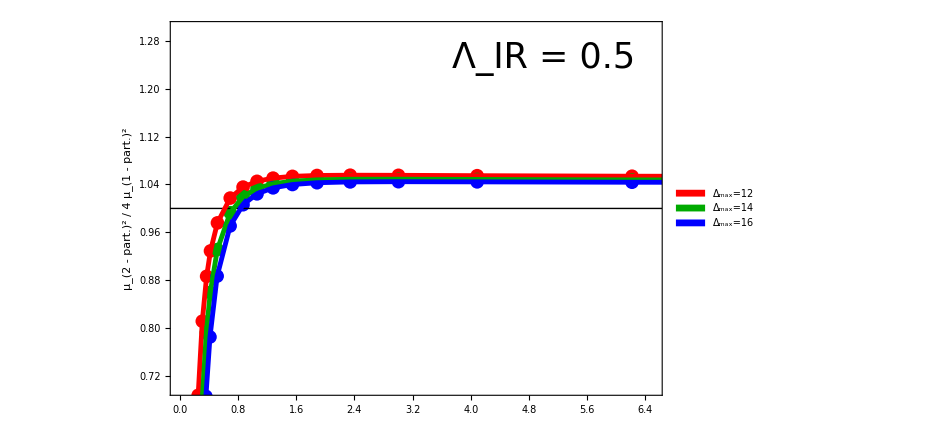

```mathematica
exper=ListPlot[{ratio2D12F1,ratio2D14F1,ratio2D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2 - part.)^2  /  4 μ_(1 - part.)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}},Epilog->{Inset[Style["Λ_IR = 0.5",FontFamily->"Times",FontSize->35],{5.,1.25}]},(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*)PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D12F1,0],Drop[ratio2D14F1,0],Drop[ratio2D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

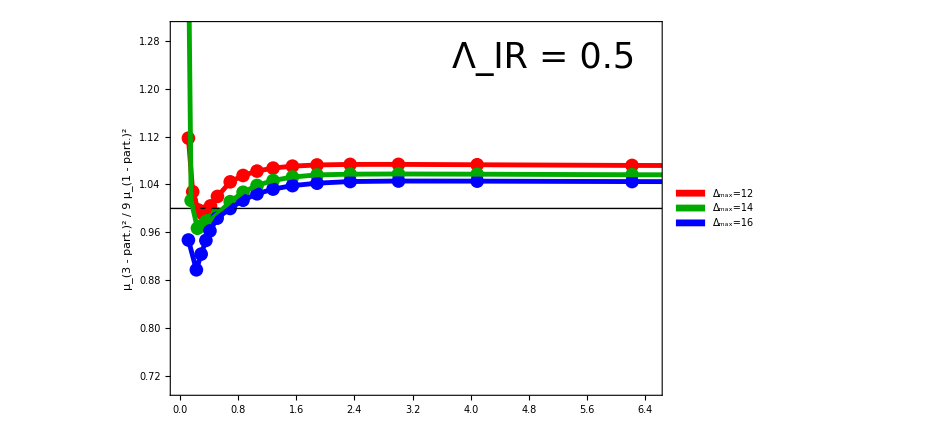

```mathematica
exper=ListPlot[{ratio3D12F1,Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(3 - part.)^2  /  9 μ_(1 - part.)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Λ_IR = 0.5",FontFamily->"Times",FontSize->35],{5.,1.25}]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D12F1,0],Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig2=Show[exper,line,fit]
```

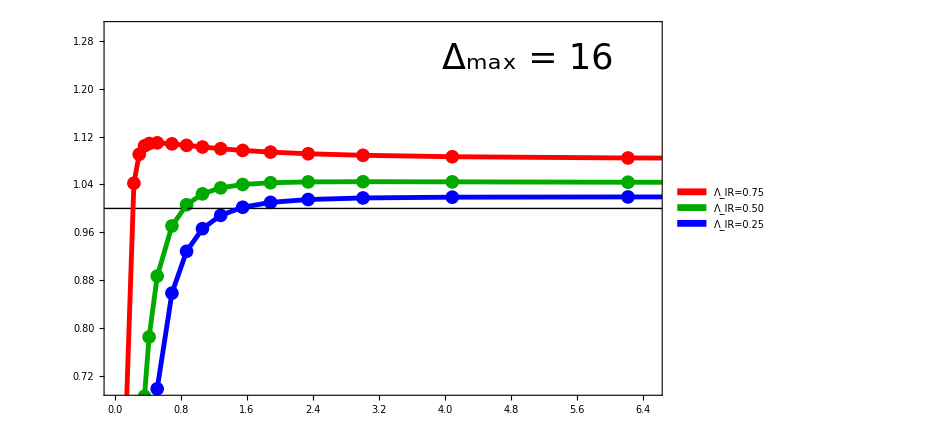

```mathematica
exper=ListPlot[{ratio2D16IR075F1,ratio2D16F1,ratio2D16IR025F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->35],{5.,1.25}]},(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*)PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,0.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio2D16IR075F1,ratio2D16F1,ratio2D16IR025F1},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

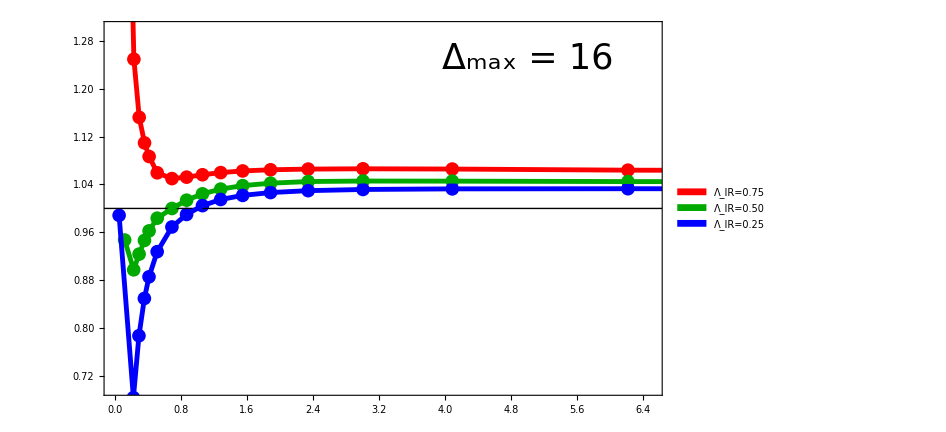

```mathematica
exper=ListPlot[{ratio3D16IR075F1,ratio3D16F1,ratio3D16IR025F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.7,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->35],{5.,1.25}]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",35},LegendLayout->{"Row",5}],{0.76,.22}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{ratio3D16IR075F1,ratio3D16F1,ratio3D16IR025F1},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig4=Show[exper,line,fit]
```

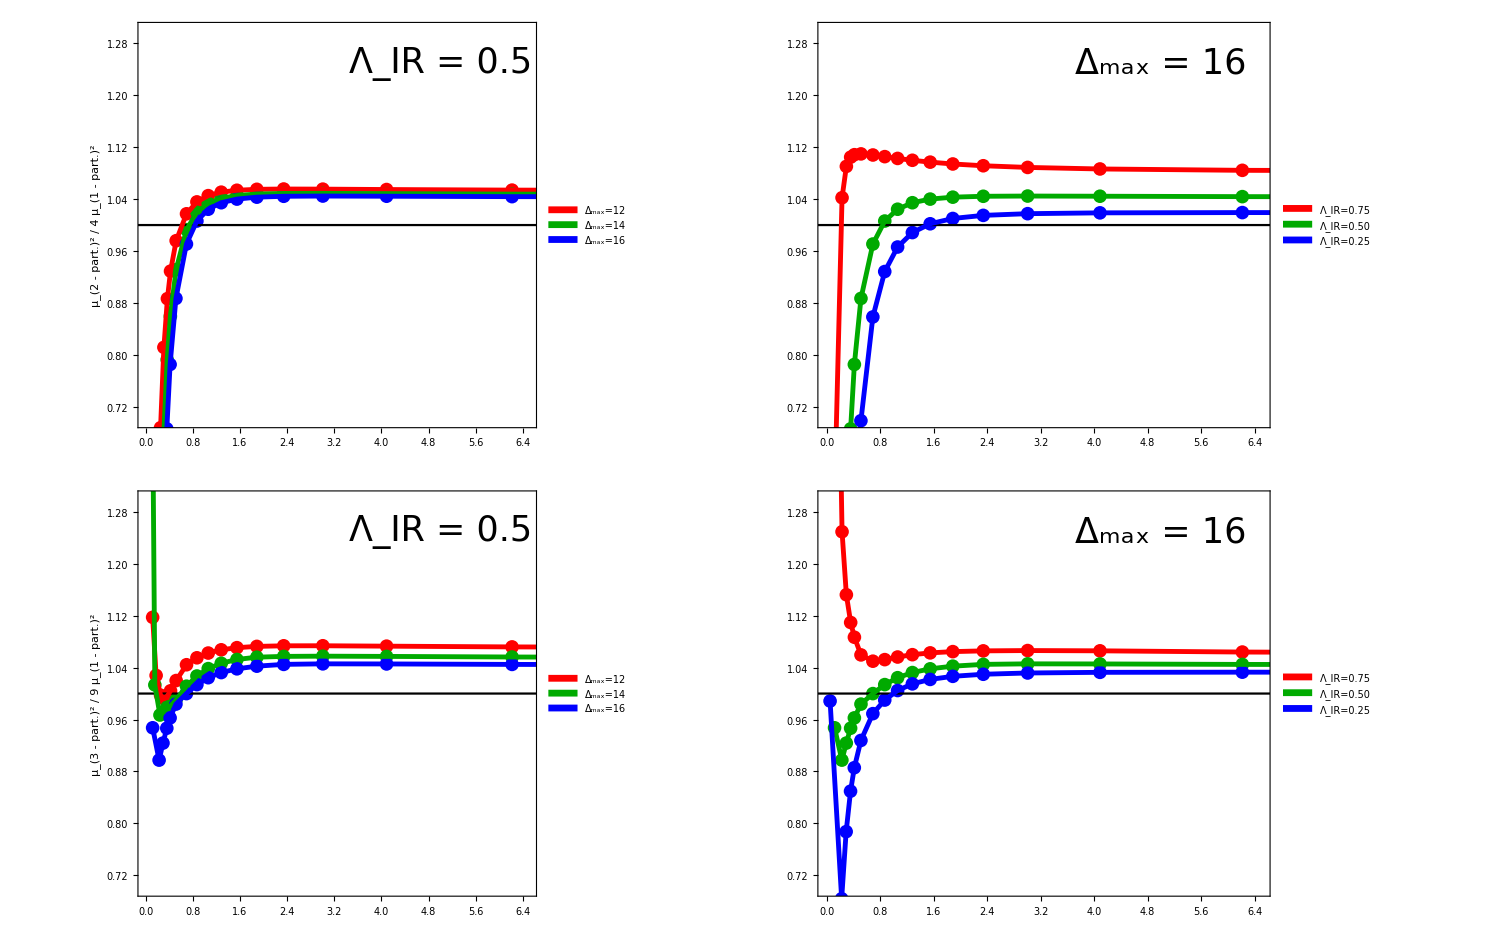
-Graphics-Eigenvalue Ratios: Varying Δ_max and Λ_IRm_gap / (g/(4  π))

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig3},{fig2,fig4}},ImageSize->1500,Spacings->{-30,0}],{Style["Eigenvalue Ratios: Varying Δ_max and Λ_IR",FontFamily->"Times",FontSize->45],Style["m_gap / (g/(4  π))",FontFamily->"Times",FontSize->40]},{Top,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{-.5,0}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./SpectrumRatiosVaryDeltaAndLambdaIR.pdf",grid];
```

## Plot Spectral Densities: vary Λ_IR

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesIR05F1Gap125"];
Get["EvenSpectralDensitiesIR075F1Gap125"];
Get["EvenSpectralDensitiesIR025F1Gap125"];
Get["StressTensorD16F1LambdaBar105VaryIR"];
```

```mathematica
temp=ListLinePlot[{ϕ2SpecD16IR075,ϕ2SpecD16,ϕ2SpecD16IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2,  ḡ=0.85",FontFamily->"Times"],{2.1,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-2)^(n-1)
FreePlot=Plot[FreeProfile[2,μsq],{μsq,2,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot1=Show[temp]
```

-Graphics-

```mathematica
temp=ListLinePlot[{ϕ4SpecD16IR075,ϕ4SpecD16,ϕ4SpecD16IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4,  ḡ=0.85",FontFamily->"Times"],{2.1,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2=Show[temp]
```

-Graphics-

```mathematica
ϕ4SpecD16IR075Rescaled=Thread[{ϕ4SpecD16IR075[[All,1]],ϕ4SpecD16IR075[[All,2]]*.77}];
ϕ4SpecD16IR025Rescaled=Thread[{ϕ4SpecD16IR025[[All,1]],ϕ4SpecD16IR025[[All,2]]*1.4}];
```

```mathematica
temp=ListLinePlot[{ϕ4SpecD16IR075Rescaled,ϕ4SpecD16,ϕ4SpecD16IR025Rescaled},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.4}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4 * const,  ḡ=0.85",FontFamily->"Times"],{3.1,1.25},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot3=Show[temp]
```

-Graphics-

```mathematica
plot4=ListLinePlot[{TIR075,TIR05,TIR025,O4IR075,O4IR05,O4IR025},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.01]},{Darker[Green],Thickness[.01]},{Blue,Thickness[.01]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.25}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.75","Λ_IR=0.50","Λ_IR=0.25","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{.15,.55}],Epilog->{Inset[Style["(T^μ)_μ,  ḡ=1.05",FontFamily->"Times"],{1.15,.22},{0,0},FormatType->TraditionalForm,BaseStyle->45],Inset[Style["0.75",FontFamily->"Times"],{4.26,.22},{0,0},FormatType->TraditionalForm,BaseStyle->20],Inset[Style["0.50",FontFamily->"Times"],{4.26,.18},{0,0},FormatType->TraditionalForm,BaseStyle->20],Inset[Style["0.25",FontFamily->"Times"],{4.26,.135},{0,0},FormatType->TraditionalForm,BaseStyle->20]}]
```

-Graphics-

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->1500,Spacings->{0,0}],{Style["Spectral Densities: Varying Λ_IR",FontFamily->"Times",FontSize->45],Style["μ / m",FontFamily->"Times",FontSize->40],Style["Integrated Spectral Density",FontFamily->"Times",FontSize->40]},{Top,Bottom,Left},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{0,0}]
```

-Graphics-Spectral Densities: Varying Λ_IRμ / mIntegrated Spectral Density

## Even Spectral Densities @ (μ_(1,even))/(g/4π)=2, Vary c_L

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD16IR05VaryF"];
```

```mathematica
couplingMapF1=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
couplingMapF2=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F2,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F2,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F2,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
couplingMapF05=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F05,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F05,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F05,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
```

```mathematica
{{2.,couplingMapF2[2*1.]},{1.,couplingMapF1[2*1.]},{.05,couplingMapF05[2*1.]}}
{{2.,couplingMapF2[2*1.]/(4π)},{1.,couplingMapF1[2*1.]/(4π)},{.05,couplingMapF05[2*1.]/(4π)}}
```

{{2.,7.72643},{1.,9.3597},{0.05,10.6921}}

{{2.,0.61485},{1.,0.744821},{0.05,0.850853}}

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 13.6322

```mathematica
f=0.5;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=10.692132906812526;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ6IntegratedSpec=Thread[{√vals,Λ^5*Accumulate[(vecs.ϕ6Overlaps)^2]}];


t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 22.917

```mathematica
ϕ2SpecD16F05=ϕ2IntegratedSpec;
ϕ4SpecD16F05=ϕ4IntegratedSpec;
ϕ6SpecD16F05=ϕ6IntegratedSpec;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="EvenSpectralDensitiesVaryF";
DeleteFile[filename];
Save[filename,{ϕ2SpecD16F1,ϕ4SpecD16F1,ϕ6SpecD16F1,ϕ2SpecD16F2,ϕ4SpecD16F2,ϕ6SpecD16F2,ϕ2SpecD16F05,ϕ4SpecD16F05,ϕ6SpecD16F05}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EvenSpectralDensitiesVaryF"];
```

```mathematica
(* ϕ2SpecD16F1New=Thread[{ϕ2SpecD16F1[[All,1]]/(9.359697951404138/(4π)),ϕ2SpecD16F1[[All,2]]}];
ϕ4SpecD16F1New=Thread[{ϕ4SpecD16F1[[All,1]]/(9.359697951404138/(4π)),ϕ4SpecD16F1[[All,2]]}];

ϕ2SpecD16F2New=Thread[{ϕ2SpecD16F2[[All,1]]/(7.726431729710043/(4π)),ϕ2SpecD16F2[[All,2]]}];
ϕ4SpecD16F2New=Thread[{ϕ4SpecD16F2[[All,1]]/(7.726431729710043/(4π)),ϕ4SpecD16F2[[All,2]]}];

ϕ2SpecD16F05New=Thread[{ϕ2SpecD16F05[[All,1]]/(10.692132906812526/(4π)),ϕ2SpecD16F05[[All,2]]}];
ϕ4SpecD16F05New=Thread[{ϕ4SpecD16F05[[All,1]]/(10.692132906812526/(4π)),ϕ4SpecD16F05[[All,2]]}]; *)
```

```mathematica
ϕ2SpecD16F1New=Thread[{ϕ2SpecD16F1[[All,1]]/(ϕ2SpecD16F1[[1,1]]/2),ϕ2SpecD16F1[[All,2]]}];
ϕ4SpecD16F1New=Thread[{ϕ4SpecD16F1[[All,1]]/(ϕ4SpecD16F1[[1,1]]/2),ϕ4SpecD16F1[[All,2]]}];

ϕ2SpecD16F2New=Thread[{ϕ2SpecD16F2[[All,1]]/(ϕ2SpecD16F2[[1,1]]/2),ϕ2SpecD16F2[[All,2]]}];
ϕ4SpecD16F2New=Thread[{ϕ4SpecD16F2[[All,1]]/(ϕ4SpecD16F2[[1,1]]/2),ϕ4SpecD16F2[[All,2]]}];

ϕ2SpecD16F05New=Thread[{ϕ2SpecD16F05[[All,1]]/(ϕ2SpecD16F05[[1,1]]/2),ϕ2SpecD16F05[[All,2]]}];
ϕ4SpecD16F05New=Thread[{ϕ4SpecD16F05[[All,1]]/(ϕ4SpecD16F05[[1,1]]/2),ϕ4SpecD16F05[[All,2]]}];
```

```mathematica
ϕ2SpecD16F1[[1;;10]]
```

{{1.48928,0.0104866},{1.55762,0.0216983},{1.59342,0.0237673},{1.65288,0.02625},{1.69576,0.0262696},{1.70636,0.0404712},{1.75415,0.0433371},{1.79024,0.0459988},{1.8217,0.0492149},{1.87466,0.0519558}}

```mathematica
ϕ2SpecD16F1New[[1;;10]]
```

{{2.,0.0104866},{2.09177,0.0216983},{2.13985,0.0237673},{2.21969,0.02625},{2.27728,0.0262696},{2.29151,0.0404712},{2.3557,0.0433371},{2.40416,0.0459988},{2.44641,0.0492149},{2.51753,0.0519558}}

```mathematica
ϕ2SpecD16F2NewRescaled=Thread[{ϕ2SpecD16F2New[[All,1]],ϕ2SpecD16F2New[[All,2]]*1.25}];
ϕ2SpecD16F05NewRescaled=Thread[{ϕ2SpecD16F05New[[All,1]],ϕ2SpecD16F05New[[All,2]]*.9}];
```

```mathematica
temp=ListLinePlot[{ϕ2SpecD16F2NewRescaled,ϕ2SpecD16F1New,ϕ2SpecD16F05NewRescaled},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^2 * const",FontFamily->"Times"],{2.1,.85},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"(ĉ)_L=2.0","(ĉ)_L=1.0","(ĉ)_L=0.5"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.5}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-2)^(n-1)
FreePlot=Plot[FreeProfile[2,μsq],{μsq,2,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot1=Show[temp]
```

-Graphics-

```mathematica
2*.85
```

1.7

```mathematica
ϕ4SpecD16F2NewRescaled=Thread[{ϕ4SpecD16F2New[[All,1]],ϕ4SpecD16F2New[[All,2]]*1.65}];
ϕ4SpecD16F05NewRescaled=Thread[{ϕ4SpecD16F05New[[All,1]],ϕ4SpecD16F05New[[All,2]]*.72}];
```

```mathematica
temp=ListLinePlot[{ϕ4SpecD16F2NewRescaled,ϕ4SpecD16F1New,ϕ4SpecD16F05NewRescaled},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->0,PlotRange->{{0,10},{0,1.}},LabelStyle->Black,Epilog->{Inset[Style["ϕ^4 * const",FontFamily->"Times"],{2.1,.85},{0,0},FormatType->TraditionalForm,BaseStyle->45]},PlotLegends->Placed[SwatchLegend[{"(ĉ)_L=2.0","(ĉ)_L=1.0","(ĉ)_L=0.5"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.5}]];
FreeProfile[n_,μ_]:=n/(4π)^(n-1)(μ-4)^(n-1)
FreePlot=Plot[FreeProfile[4,μsq],{μsq,4,100},PlotStyle->{Black,Dashed,Thickness[.004]}];
plot2=Show[temp]
```

-Graphics-

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2}},ImageSize->1500,Spacings->{0,0}],{Style["Spectral Densities: Varying (ĉ)_L",FontFamily->"Times",FontSize->45],Style["ϕ^n Integrated Spectral Density",FontFamily->"Times",FontSize->35],Style["μ / m_gap",FontFamily->"Times",FontSize->35]},{Top,Left,Bottom},RotateLabel->True]
```

-Graphics-Spectral Densities: Varying (ĉ)_Lϕ^n Integrated Spectral Densityμ / m_gap

## Stress Tensor @ (μ_(1,even))/(g/4π)= 0.15, Vary c_L

### Get Couplings

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD16IR05F1"];
Get["SpectrumD16IR05VaryF"];
```

```mathematica
couplingMapF1=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
couplingMapF2=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F2,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F2,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F2,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
couplingMapF05=Interpolation[Select[Thread[{(√(Select[EvenSpectrumD16F05,#[[2]]==65&][[All,3]]))/(((Select[EvenSpectrumD16F05,#[[2]]==65&][[All,1]])/(4π))+10^-10),Select[EvenSpectrumD16F05,#[[2]]==65&][[All,1]]}],#[[1]]∈Reals&]];
```

```mathematica
{{2.,couplingMapF2[.15]},{1.,couplingMapF1[.15]},{.05,couplingMapF05[.15]}}
{{2.,couplingMapF2[.15]/(4π)},{1.,couplingMapF1[.15]/(4π)},{.05,couplingMapF05[.15]/(4π)}}
```

{{2.,9.49398},{1.,13.1994},{0.05,18.027}}

{{2.,0.755507},{1.,1.05037},{0.05,1.43454}}

### Odd Sector

```mathematica
Δmax=16;
kmax=65;
sector="odd";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 5.7058

```mathematica
f=0.5;
```

```mathematica
(* Subscript[Λ, IR]=0.5 & 0.75: *)
(* glist={13.4}//N;  *)
(* Subscript[Λ, IR]=0.25 *)
glist={18.027012979411758}//N;

nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
{vals,vecs}=eigensys[full];
{g,vals[[1]],vecs[[1]]},{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 11.5075

```mathematica
Expϕ2F05=Table[2newdata[[iG,3]].mass.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
Expϕ4F05=Table[glist[[iG]]*Λ*newdata[[iG,3]].int.newdata[[iG,3]],{iG,Length[glist]}];
```

```mathematica
iGc=1;
glist[[iGc]]
```

18.027

```mathematica
δTF05=Solve[(1-(1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+x)*glist[[iGc]]^2)Expϕ2F05[[iGc]]+Expϕ4F05[[iGc]]==0,x][[1,1,2]]
```

-0.00554911

```mathematica
rF05=1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]+δTF05
```

-0.0000874272

```mathematica
SetDirectory[NotebookDirectory[]];
Get["StressTensorD16F1LambdaBar105VaryIR"];
```

```mathematica
δTF2
δTF1
δTF05
```

0.00237196

-0.00299393

-0.00554911

```mathematica
rF2
rF1
rF05
```

0.00783365

0.00246776

-0.0000874272

### Even Sector

```mathematica
Δmax=16;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=0.5*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 15.1847

```mathematica
f=0.5;
```

```mathematica
totsize=Sum[numStates[n,Δmax],{n,If[sector=="odd",3,2],Floor[Δmax/(3/2)],2}]
ϕ2Overlaps=PadRight[ϕnOverlaps[2,Δmax,kmax],totsize*kmax];
ϕ4Overlaps=PadRight[ϕnOverlaps[4,Δmax,kmax],totsize*kmax,0.,numStates[2,Δmax]*kmax];
ϕ6Overlaps=PadRight[ϕnOverlaps[6,Δmax,kmax],totsize*kmax,0.,(numStates[2,Δmax]+numStates[4,Δmax])*kmax];

(*
ϕOverlaps=PadRight[{1},1+totsize*kmax];
ϕ3Overlaps=PadRight[ϕnOverlaps[3,Δmax,kmax],1+totsize*kmax,0.,1];
ϕ5Overlaps=PadRight[ϕnOverlaps[5,Δmax,kmax],1+totsize*kmax,0.,1+numStates[3,Δmax]*kmax];
*)
```

303

```mathematica
t1=AbsoluteTime[];

g=18.027012979411758;
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
{vals,vecs}=eigensys[full];
ϕ2IntegratedSpec=Thread[{√vals,Λ*Accumulate[(vecs.ϕ2Overlaps)^2]}];
ϕ4IntegratedSpec=Thread[{√vals,Λ^3*Accumulate[(vecs.ϕ4Overlaps)^2]}];
ϕ2ϕ4IntegratedSpec=Thread[{√vals,Λ^2*Accumulate[(vecs.ϕ2Overlaps)(vecs.ϕ4Overlaps)]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 21.781

```mathematica
ϕ2IntegratedSpecF05=ϕ2IntegratedSpec;
ϕ4IntegratedSpecF05=ϕ4IntegratedSpec;
ϕ2ϕ4IntegratedSpecF05=ϕ2ϕ4IntegratedSpec;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["StressTensorD16IR05VaryF"];
```

```mathematica
r=rF2;
g=9.493977915361612;

TF2=Thread[{ϕ2IntegratedSpecF2[[All,1]]/(ϕ2IntegratedSpecF2[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF2[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecF2[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecF2[[All,2]]}];

O2F2=Thread[{ϕ2IntegratedSpecF2[[All,1]]/(ϕ2IntegratedSpecF2[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF2[[All,2]]}];

O4F2=Thread[{ϕ2IntegratedSpecF2[[All,1]]/(ϕ2IntegratedSpecF2[[1,1]]/2),(g/(4!))^2*ϕ4IntegratedSpecF2[[All,2]]}];
```

```mathematica
ϕ2IntegratedSpecF2[[1,1]]/(g/(4π))
```

0.122498

```mathematica
r=rF1;
g=13.199388982081437;

TF1=Thread[{ϕ2IntegratedSpecF1[[All,1]]/(ϕ2IntegratedSpecF1[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF1[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecF1[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecF1[[All,2]]}];

O2F1=Thread[{ϕ2IntegratedSpecF1[[All,1]]/(ϕ2IntegratedSpecF1[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF1[[All,2]]}];

O4F1=Thread[{ϕ2IntegratedSpecF1[[All,1]]/(ϕ2IntegratedSpecF1[[1,1]]/2),(g/(4!))^2*ϕ4IntegratedSpecF1[[All,2]]}];
```

```mathematica
r=rF05;
g=18.027012979411758;

TF05=Thread[{ϕ2IntegratedSpecF05[[All,1]]/(ϕ2IntegratedSpecF05[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF05[[All,2]]+2(1-r*g^2)*g/(4!)*ϕ2ϕ4IntegratedSpecF05[[All,2]]+(g/(4!))^2*ϕ4IntegratedSpecF05[[All,2]]}];

O2F05=Thread[{ϕ2IntegratedSpecF05[[All,1]]/(ϕ2IntegratedSpecF05[[1,1]]/2),(1-r*g^2)^2 ϕ2IntegratedSpecF05[[All,2]]}];

O4F05=Thread[{ϕ2IntegratedSpecF05[[All,1]]/(ϕ2IntegratedSpecF05[[1,1]]/2),(g/(4!))^2*ϕ4IntegratedSpecF05[[All,2]]}];
```

```mathematica
plot3=ListLinePlot[{TF2,O2F2,O4F2},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]},{Red,Thickness[.002]},{Orange,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,80},{0,.05}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{None,"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{.25,.6}],Epilog->{Inset[Style["(T^μ)_μ,  (ĉ)_L=2.0",FontFamily->"Times"],{19,.043},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

-Graphics-

```mathematica
5/(.15/2)
```

66.6667

```mathematica
5/(.75)
```

6.66667

```mathematica
(0.7555067574175443)
```

0.113326

```mathematica
plot4=ListLinePlot[{TF05,O2F05,O4F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]},{Red,Thickness[.002]},{Orange,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,80},{0,1.2}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{None,"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.25,.6}],Epilog->{Inset[Style["(T^μ)_μ,  (ĉ)_L=0.5",FontFamily->"Times"],{19,1.03},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

-Graphics-

```mathematica
plot3old=ListLinePlot[{TF2,O2F2,O4F2},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]},{Red,Thickness[.002]},{Orange,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.05}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{None,"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{.25,.6}],Epilog->{Inset[Style["(T^μ)_μ,  (ĉ)_L=2.0",FontFamily->"Times"],{1.25,.043},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

-Graphics-

```mathematica
plot4old=ListLinePlot[{TF05,O2F05,O4F05},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]},{Red,Thickness[.002]},{Orange,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,1}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{None,"(m^2-(c_L+δ_T)g^2) ϕ^2","g/(4!)ϕ^4"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.25,.6}],Epilog->{Inset[Style["(T^μ)_μ,  (ĉ)_L=0.5",FontFamily->"Times"],{1.25,.85},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

-Graphics-

```mathematica
grid=Labeled[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->1500,Spacings->{0,0}],{Style["Spectral Densities: Varying (ĉ)_L",FontFamily->"Times",FontSize->45],Style["μ / m_gap",FontFamily->"Times",FontSize->40],Style["Integrated Spectral Density",FontFamily->"Times",FontSize->40]},{Top,Bottom,Left},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{0,0}]
```

-Graphics-Spectral Densities: Varying (ĉ)_Lμ / m_gapIntegrated Spectral Density

```mathematica
temp=ListLinePlot[{TF1,O4F1,O2F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->25,ImageSize->700,PlotStyle->{{Red,Thickness[.01]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Blue,Thickness[.002]},{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,5},{0,.25}},LabelStyle->Black,PlotLegends->Placed[SwatchLegend[{"(ĉ)_L=1.0","O4","O2"},LabelStyle->{FontFamily->"Times",30},LegendLayout->{"Row",5}],{0.15,.6}],Epilog->{Inset[Style["(T^μ)_μ",FontFamily->"Times"],{.65,.22},{0,0},FormatType->TraditionalForm,BaseStyle->45]}]
```

-Graphics-

```mathematica
TF05[[1;;10]]
```

{{0.153559,0.00075427},{0.304522,0.00168857},{0.433849,0.00237589},{0.583867,0.00246604},{0.694172,0.00250599},{0.706478,0.00250942},{0.734171,0.00252134},{0.771381,0.0026124},{0.784519,0.00262384},{0.792665,0.00264862}}

```mathematica
TF1[[1;;10]]
```

{{0.149875,0.000195867},{0.291064,0.000523461},{0.4148,0.000806274},{0.552766,0.000869817},{0.722307,0.000872116},{0.743243,0.000909545},{0.753583,0.000924151},{0.781052,0.000941809},{0.83089,0.000946579},{0.91322,0.00101664}}

```mathematica
TF2[[1;;10]]
```

{{0.122498,0.000035486},{0.268133,0.000153855},{0.390652,0.00028903},{0.507268,0.000349825},{0.649441,0.00035909},{0.862308,0.000390603},{0.866855,0.000391923},{0.868963,0.000406519},{0.874197,0.00041637},{0.877362,0.000416606}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="StressTensorD16IR05VaryF";
DeleteFile[filename];
Save[filename,{δTF2,rF2,ϕ2IntegratedSpecF2,ϕ4IntegratedSpecF2,ϕ2ϕ4IntegratedSpecF2,TF2,O2F2,O4F2,δTF1,rF1,ϕ2IntegratedSpecF1,ϕ4IntegratedSpecF1,ϕ2ϕ4IntegratedSpecF1,TF1,O2F1,O4F1,δTF05,rF05,ϕ2IntegratedSpecF05,ϕ4IntegratedSpecF05,ϕ2ϕ4IntegratedSpecF05,TF05,O2F05,O4F05}];
```

```mathematica
rIR05
rIR075
```

0.00251944

0.00224646

## Scratch

```mathematica
Δmax=12;
kmax=65;
sector="even";

m=1.;
ΛIR=0.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ΛMAX=ΛIR*√((1-ratioWidth^KMAX)/(ratioWidth^(KMAX-1)(1-ratioWidth)));

t1=AbsoluteTime[];

kinetic=kineticMatrix[Δmax,kmax,sector];
mass=massMatrix[Δmax,kmax,sector];
int=intMatrix[Δmax,kmax,sector];
nonlocalCT=nonlocalMatrix[Δmax,kmax,Λ,sector];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.129279

```mathematica
f=0.;
```

```mathematica
(* Scan over couplings *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,13.2,13.4,13.5}//N; *)
(* glist={12.5,12.75,13.2,13.4,13.5,13.6}//N; *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5,12.75,13,14,15,15.5,15.75,16.,16.1,16.2}//N; *)
(* glist={0,1,2,3,4,5,6,7,8,9,10,11,12,12.5, 12.75,13,13.5,13.7,13.9,14.,14.1,14.2,14.4,14.5}//N; *)
glist={0,2,4,6,8,10,12,14,16,17,18,18.25,18.5,18.75,19,19.1,19.18}//N;
nvals=2;

t1=AbsoluteTime[];

Monitor[
newdata=Table[
g=glist[[iG]];
full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass;
(* full=Λ^2*kinetic+m^2*mass+g*Λ*int +g^2* nonlocalCT[[1,1]]*mass-f*1/(96 π^2)Log[(ΛMAX/m+1)^2/(8(ΛMAX/m-1))]*g^2*mass; *)
vals=eigenvals[full];
{g,kmax,vals[[1;;nvals]]}//Flatten,{iG,Length[glist]}];
,{iG}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 3.55439

```mathematica
newdata
```

{{0.,65,4.24936,4.53061},{2.,65,4.21192,4.48986},{4.,65,4.08487,4.35917},{6.,65,3.86866,4.13893},{8.,65,3.56264,3.82943},{10.,65,3.16496,3.431},{12.,65,2.67209,2.94425},{14.,65,2.07791,2.36995},{16.,65,1.37205,1.70781},{17.,65,0.971509,1.2809},{18.,65,0.532457,0.745348},{18.25,65,0.415237,0.602861},{18.5,65,0.294153,0.455306},{18.75,65,0.168104,0.300005},{19.,65,0.0335617,0.12913},{19.1,65,-0.0275021,0.050885},{19.18,65,-0.099953,-0.0223974}}

```mathematica
data1p=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]]}]
data2p=Thread[{(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]]}]
data3p=Thread[{(Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]])/(4π),Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]]}]
```

{{0.,1.},{0.0795775,0.994593},{0.159155,0.978558},{0.238732,0.952112},{0.31831,0.915397},{0.397887,0.86849},{0.477465,0.8114},{0.557042,0.744058},{0.63662,0.666298},{0.716197,0.577808},{0.795775,0.478037},{0.875352,0.365954},{0.95493,0.239324},{0.994718,0.168844},{1.01461,0.131039},{1.03451,0.0907137},{1.05042,0.0555218},{1.06634,0.013914},{1.0743,-0.0490944},{1.08225,-0.789479}}

{{0.,4.16919},{0.0795775,4.14942},{0.159155,4.08555},{0.238732,3.9776},{0.31831,3.82538},{0.397887,3.62839},{0.477465,3.38586},{0.557042,3.09662},{0.63662,2.759},{0.716197,2.37066},{0.795775,1.92827},{0.875352,1.42674},{0.95493,0.856235},{0.994718,0.537781},{1.01461,0.366821},{1.03451,0.184204},{1.05042,0.0242649},{1.06634,-0.16249},{1.0743,-0.281378}}

{{0.,9.38238},{0.0795775,9.34319},{0.159155,9.20226},{0.238732,8.95985},{0.31831,8.61607},{0.397887,8.16866},{0.477465,7.61241},{0.557042,6.95448},{0.63662,6.19484},{0.716197,5.33341},{0.795775,4.37005},{0.875352,3.30442},{0.95493,2.13315},{0.994718,1.47848},{1.01461,1.13297},{1.03451,0.771333},{1.05042,0.465979},{1.06634,0.137604},{1.0743,-0.0145982},{1.08225,-0.759793}}

```mathematica
zero=Plot[0,{x,-5,20},PlotStyle->{Black,Thickness[0.005]}];
exper=ListPlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.12},{-.5,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[16]<>",  k_max = 65",FontFamily->"Times",FontSize->20],{.9,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}],PlotLabel->Style["Spectrum vs. λ̄",FontFamily->"Times",FontSize->20,FontColor->Black]];
fit=ListLinePlot[{Drop[data3p,-1],Drop[data2p,-2],Drop[data1p,-2]},PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

-Graphics-

```mathematica
Λ
```

1411.16

```mathematica
1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))]
```

0.00546169

```mathematica
Select[OddSpectrumD16F1,#[[2]]==65&]
```

{{0.,65,1.,9.38238},{1.,65,0.994593,9.34319},{2.,65,0.978558,9.20226},{3.,65,0.952112,8.95985},{4.,65,0.915397,8.61607},{5.,65,0.86849,8.16866},{6.,65,0.8114,7.61241},{7.,65,0.744058,6.95448},{8.,65,0.666298,6.19484},{9.,65,0.577808,5.33341},{10.,65,0.478037,4.37005},{11.,65,0.365954,3.30442},{12.,65,0.239324,2.13315},{12.5,65,0.168844,1.47848},{12.75,65,0.131039,1.13297},{13.,65,0.0907137,0.771333},{13.2,65,0.0555218,0.465979},{13.4,65,0.013914,0.137604},{13.5,65,-0.0490944,-0.0145982},{13.6,65,-0.789479,-0.759793}}

```mathematica
Drop[Select[OddSpectrumD16F1,#[[2]]==65&],-1][[All,3]]
```

{1.,0.994593,0.978558,0.952112,0.915397,0.86849,0.8114,0.744058,0.666298,0.577808,0.478037,0.365954,0.239324,0.168844,0.131039,0.0907137,0.0555218,0.013914,-0.0490944}

```mathematica
Select[EvenSpectrumD16F1,#[[2]]==65&]
```

{{0.,65,4.16919,4.45044},{1.,65,4.14942,4.42963},{2.,65,4.08555,4.36464},{3.,65,3.9776,4.25557},{4.,65,3.82538,4.10251},{5.,65,3.62839,3.90551},{6.,65,3.38586,3.66449},{7.,65,3.09662,3.37343},{8.,65,2.759,3.00975},{9.,65,2.37066,2.59059},{10.,65,1.92827,2.11496},{11.,65,1.42674,1.57831},{12.,65,0.856235,0.971174},{12.5,65,0.537781,0.633641},{12.75,65,0.366821,0.452779},{13.,65,0.184204,0.260149},{13.2,65,0.0242649,0.0929317},{13.4,65,-0.16249,-0.0983016},{13.5,65,-0.281378,-0.218194}}

```mathematica
ratio2D16F1=Select[Thread[{(√Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])/((Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]],-1]/(4π))+10^-10),(Select[EvenSpectrumD16F1,#[[2]]==65&][[All,3]])/(4*Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])}],#[[1]]∈Reals&]
ratio2D14F1=Select[Thread[{(√(Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD14F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD14F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04299},{6.21546,1.04377},{4.08726,1.04442},{3.00576,1.04473},{2.34219,1.04445},{1.88658,1.04322},{1.54851,1.04045},{1.2822,1.0352},{1.06135,1.02571},{0.868841,1.00843},{0.691084,0.974674},{0.512297,0.89443},{0.413088,0.796268},{0.35678,0.699831},{0.291141,0.507654},{0.22432,0.109258},{0.110619,-2.91956}}

{{1.×10^10,1.04599},{12.5323,1.04678},{6.21544,1.04764},{4.08722,1.0484},{3.0057,1.04886},{2.34212,1.04882},{1.88653,1.048},{1.5485,1.04595},{1.28227,1.04198},{1.06159,1.03478},{0.869401,1.02175},{0.692282,0.996591},{0.515011,0.938402},{0.417593,0.870182},{0.362955,0.806135},{0.300388,0.686665},{0.239065,0.469152},{0.149938,-0.429311},{0.0418979,-16.9753}}

{{1.×10^10,1.05192},{12.5323,1.05283},{6.2154,1.05381},{4.08714,1.05471},{3.00558,1.05537},{2.34195,1.05561},{1.88631,1.05525},{1.54826,1.05397},{1.28203,1.05131},{1.06142,1.0464},{0.869401,1.03751},{0.692714,1.02053},{0.516608,0.982071},{0.420633,0.938396},{0.367342,0.89872},{0.307185,0.827996},{0.249848,0.709646},{0.173115,0.337021},{0.111689,-0.650216}}

```mathematica
exper=ListPlot[{ratio2D12F1,ratio2D14F1,ratio2D16F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(1, even)^2  /  4 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{.9,1.15}},Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,0.21}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D12F1,0],Drop[ratio2D14F1,0],Drop[ratio2D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

-Graphics-

```mathematica
OddSpectrumD16F1NOCT
```

{{0.,65,1.,9.38238},{1.,65,0.994595,9.38764},{2.,65,0.97859,9.38009},{3.,65,0.952264,9.36008},{4.,65,0.915862,9.32785},{5.,65,0.869597,9.28357},{6.,65,0.813659,9.22734},{7.,65,0.748217,9.15921},{8.,65,0.673422,9.0792},{9.,65,0.589413,8.98731},{10.,65,0.496315,8.8835},{11.,65,0.394242,8.7677},{12.,65,0.283297,8.6398},{13.,65,0.163576,8.49968},{13.2,65,0.138587,8.47018},{13.4,65,0.113251,8.44017},{13.5,65,0.100453,8.42499}}

```mathematica
ratio2D16F1NOCT=Select[Thread[{(√(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0423},{12.5324,1.04399},{6.21556,1.0478},{4.08759,1.05367},{3.00653,1.06164},{2.34368,1.07191},{1.88921,1.08483},{1.55284,1.10099},{1.28903,1.12142},{1.07196,1.14796},{0.885296,1.18412},{0.717296,1.23761},{0.557378,1.32932},{0.47636,1.40869},{0.434474,1.46613},{0.390955,1.54456},{0.354403,1.63223},{0.315592,1.75856},{0.295024,1.84565}}

```mathematica
exper=ListPlot[{ratio2D16F1,ratio2D16F1NOCT},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Orange,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.15}},Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->28],{5.7,1.13}],Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"State-Dep. CT","State-Indep. CT"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.77,0.15}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D16F1,0],Drop[ratio2D16F1NOCT,0]},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
fig2=Show[exper,line,fit]
```

-Graphics-

```mathematica
ratio3D16F1=Select[Thread[{(√Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])/((Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,1]],-1]/(4π))+10^-10),Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,4]],-1]/(9*Drop[Select[OddSpectrumD16F1,#[[2]]==65&][[All,3]],-1])}],#[[1]]∈Reals&]
ratio3D14F1=Select[Thread[{(√(Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD14F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD14F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD14F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.04249},{12.5324,1.04378},{6.21546,1.04488},{4.08726,1.04561},{3.00576,1.04582},{2.34219,1.04506},{1.88658,1.04242},{1.54851,1.03852},{1.2822,1.03304},{1.06135,1.0256},{0.868841,1.01574},{0.691084,1.00329},{0.512297,0.990357},{0.413088,0.972941},{0.35678,0.960666},{0.291141,0.944771},{0.22432,0.932524},{0.110619,1.09885}}

{{1.×10^10,1.05347},{12.5323,1.05498},{6.21544,1.05629},{4.08722,1.05722},{3.0057,1.05763},{2.34212,1.05737},{1.88653,1.05626},{1.5485,1.05291},{1.28227,1.04733},{1.06159,1.03959},{0.869401,1.02899},{0.692282,1.01468},{0.515011,0.996923},{0.417593,0.990649},{0.362955,0.992934},{0.300388,0.992229},{0.239065,1.00003},{0.149938,1.10256},{0.0418979,4.43038}}

{{1.×10^10,1.0685},{12.5323,1.07027},{6.2154,1.07182},{4.08714,1.073},{3.00558,1.07365},{2.34195,1.07365},{1.88631,1.07284},{1.54826,1.07105},{1.28203,1.06803},{1.06142,1.06345},{0.869401,1.05685},{0.692714,1.04746},{0.516608,1.02598},{0.420633,1.01348},{0.367342,1.0088},{0.307185,1.00993},{0.249848,1.02518},{0.173115,1.08825},{0.111689,1.27519}}

```mathematica
exper=ListPlot[{ratio3D12F1,Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2, odd)^2  /  9 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.35}]},PlotLegends->Placed[SwatchLegend[{"Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,.75}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D12F1,0],Drop[ratio3D14F1,0],Drop[ratio3D16F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

-Graphics-

```mathematica
ratio3D16F1NOCT=Select[Thread[{(√(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD16F1NOCT,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.04249},{12.5324,1.04874},{6.21556,1.06503},{4.08759,1.09214},{3.00653,1.13164},{2.34368,1.18619},{1.88921,1.26006},{1.55284,1.36015},{1.28903,1.49802},{1.07196,1.69421},{0.885296,1.98877},{0.717296,2.47104},{0.557378,3.38859},{0.47636,4.24163},{0.434474,4.88065},{0.390955,5.77351},{0.354403,6.7909},{0.315592,8.28071},{0.295024,9.3189}}

```mathematica
exper=ListPlot[{Drop[ratio3D16F1,0],ratio3D16F1NOCT},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Blue,PointSize[0.014]},{Orange,PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["Δ_max = 16",FontFamily->"Times",FontSize->28],{5.7,1.26}],Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.2}]},PlotLegends->Placed[SwatchLegend[{"State-Dep. CT","State-Indep. CT","Δ_max=16"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.77,0.11}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D16F1,0],ratio3D16F1NOCT},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Blue}},InterpolationOrder->1,PlotRange->All];
fig4=Show[exper,line,fit]
```

-Graphics-

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2},{fig3,fig4}},ImageSize->1500,Spacings->{-30,0}],{Style["Spectrum: Eigenvalue Ratios",FontFamily->"Times",FontSize->45],Style["m_gap / (λ̄ m)",FontFamily->"Times",FontSize->40]},{Top,Bottom},Spacings->{0,0}]
```

-Graphics-Spectrum: Eigenvalue Ratiosm_gap / (λ̄ m)

Vary  ΛIR:

```mathematica
SetDirectory[NotebookDirectory[]];
Get["SpectrumD12IR05F1"];
Get["SpectrumD12IR025F1"];
Get["SpectrumD12IR01F1"];
```

```mathematica
ratio3D12IR05F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12IR025F1=Select[Thread[{(√(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio3D12IR01F1=Select[Thread[{(√(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,4]])/(9*Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.0685},{12.5323,1.07027},{6.2154,1.07182},{4.08714,1.073},{3.00558,1.07365},{2.34195,1.07365},{1.88631,1.07284},{1.54826,1.07105},{1.28203,1.06803},{1.06142,1.06345},{0.869401,1.05685},{0.692714,1.04746},{0.516608,1.02598},{0.420633,1.01348},{0.367342,1.0088},{0.307185,1.00993},{0.249848,1.02518},{0.173115,1.08825},{0.111689,1.27519}}

{{1.×10^10,1.05809},{12.5369,1.0589},{6.22465,1.05937},{4.1012,1.05928},{3.02469,1.05846},{2.36648,1.05667},{1.91676,1.05367},{1.58534,1.04914},{1.32679,1.04262},{1.11541,1.03344},{0.935131,1.02049},{0.774648,1.00179},{0.624376,0.973138},{0.549724,0.952111},{0.511708,0.938793},{0.472766,0.922736},{0.292344,0.785227},{0.243798,0.70715},{0.180382,0.528377},{0.12533,0.288242}}

{{1.×10^10,1.05517},{12.543,1.05543},{6.23678,1.05535},{4.11959,1.0547},{3.04958,1.05327},{2.39823,1.05086},{1.95589,1.04719},{1.63255,1.04197},{1.38303,1.03481},{1.18206,1.02514},{1.01419,1.01219},{0.869247,0.994705},{0.739895,0.97059},{0.679172,0.954938},{0.649486,0.945905},{0.620125,0.935895},{0.503791,0.881821},{0.381623,0.781895},{0.311865,0.683231},{0.271659,0.597143},{0.223827,0.440859},{0.200164,0.331358},{0.162599,0.172528}}

```mathematica
exper=ListPlot[{ratio3D12IR05F1,ratio3D12IR025F1,ratio3D12IR01F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(2, odd)^2  /  9 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->600,PlotRange->{{0,6.5},{.9,1.3}}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},*),Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.35}]},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.5","Λ_IR=0.25","Λ_IR=0.1"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,.75}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio3D12IR05F1,0],Drop[ratio3D12IR025F1,0],Drop[ratio3D12IR01F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig3=Show[exper,line,fit]
```

-Graphics-

```mathematica
ratio2D12IR05F1=Select[Thread[{(√(Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12IR01F1=Select[Thread[{(√(Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12IR01F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12IR01F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
ratio2D12IR025F1=Select[Thread[{(√(Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]]))/(((Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,1]])/(4π))+10^-10),(Select[EvenSpectrumD12IR025F1,#[[2]]==65&][[All,3]])/(4*Select[OddSpectrumD12IR025F1,#[[2]]==65&][[All,3]])}],#[[1]]∈Reals&]
```

{{1.×10^10,1.05192},{12.5323,1.05283},{6.2154,1.05381},{4.08714,1.05471},{3.00558,1.05537},{2.34195,1.05561},{1.88631,1.05525},{1.54826,1.05397},{1.28203,1.05131},{1.06142,1.0464},{0.869401,1.03751},{0.692714,1.02053},{0.516608,0.982071},{0.420633,0.938396},{0.367342,0.89872},{0.307185,0.827996},{0.249848,0.709646},{0.173115,0.337021},{0.111689,-0.650216}}

{{1.×10^10,1.02192},{12.543,1.02203},{6.23678,1.02187},{4.11959,1.02122},{3.04958,1.01979},{2.39823,1.01723},{1.95589,1.01304},{1.63255,1.00656},{1.38303,0.99695},{1.18206,0.983023},{1.01419,0.962974},{0.869247,0.933814},{0.739895,0.890138},{0.679172,0.859806},{0.649486,0.84162},{0.620125,0.820895},{0.503791,0.698938},{0.381623,0.432024},{0.311865,0.124078},{0.271659,-0.166324},{0.223827,-0.723135},{0.200164,-1.14339},{0.162599,-2.09917}}

{{1.×10^10,1.02848},{12.5369,1.02886},{6.22465,1.02904},{4.1012,1.02879},{3.02469,1.02788},{2.36648,1.02602},{1.91676,1.0228},{1.58534,1.01761},{1.32679,1.00947},{1.11541,0.996762},{0.935131,0.976661},{0.774648,0.94358},{0.624376,0.884277},{0.549724,0.834401},{0.511708,0.800109},{0.472766,0.756061},{0.389835,0.615043},{0.353438,0.520333},{0.31386,0.378788},{0.292344,0.277382},{0.269198,0.140954},{0.243798,-0.0539608},{0.180382,-0.926816},{0.12533,-2.80472}}

```mathematica
exper=ListPlot[{ratio2D12IR05F1,ratio2D12IR025F1,ratio2D12IR01F1},Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],PlotStyle->{{Red,PointSize[0.014]},{Darker[Green],PointSize[0.014]},{Blue,PointSize[0.014]}},FrameLabel->{None,Style["μ_(1, even)^2  /  4 μ_(1, odd)^2",FontFamily->"Times",FontSize->40,FontColor->Black],None,None},FrameTicksStyle->Directive[Black,26],LabelStyle->Black,ImageSize->700,PlotRange->{{0,6.5},{0,1.15}},Epilog->{Inset[Style["k_max = 65",FontFamily->"Times",FontSize->20],{5.8,1.095}]}(*,Epilog->{Inset[Style["Δ_max = "<>ToString[16],FontFamily->"Times",FontSize->20],{1.05,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2",(*"μ_(1, even)^2",*)"μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]*),PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.5","Λ_IR=0.25","Λ_IR=0.1"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Row",5}],{0.85,0.21}]];
line=Plot[1,{x,-10,20},PlotStyle->{Black,Thick}];
fit=ListLinePlot[{Drop[ratio2D12IR05F1,0],Drop[ratio2D12IR025F1,0],Drop[ratio2D12IR01F1,0]},PlotStyle->{{Red,Thickness[.005]},{Darker[Green],Thickness[.005]},{Blue,Thickness[.005]}},InterpolationOrder->1,PlotRange->All];
fig1=Show[exper,line,fit]
```

-Graphics-